```mathematica
Qvalues[pair_]:=
Module[{},
output = {};
transpoints = {};
(*Get an ordering of the Q-values based on the strategy-pair*)
assumptions = Flatten[{
               If[pair[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[pair[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[pair[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[pair[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[pair[[5]]==0, Q2000>Q2001, Q2000<Q2001],
               If[pair[[6]]==0, Q2010>Q2011, Q2010<Q2011],
               If[pair[[7]]==0, Q2100>Q2101, Q2100<Q2101],
               If[pair[[8]]==0, Q2110>Q2111, Q2110<Q2111],
               restrictions}];

(*Solve the Bellman equations*)
Assuming[assumptions,
{q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q3=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q4=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q5=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q6=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])]
}];
sol=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
sol[[1]][[All,2]]
];
```

```mathematica
getstuff[graph_]:=
Module[{g=graph},
(*All 256 strategy pairs*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];

bestresps = {};
Do[bestresps = AppendTo[bestresps,toBin[g[[i]][[2]],4]],{i,1,Length[g]}];

(*Find the best responses to the pairs*)
counterstrats = {};
Do[
p1 =FromDigits[inputlist[[i]][[1;;4]],2] + 1 ;
p2 = FromDigits[inputlist[[i]][[5;;8]],2] + 1 ;
AppendTo[counterstrats,Join[bestresps[[p2]],bestresps[[p1]]]];
,{i,1,256}];

differences= ConstantArray[{},256];
Do[Do[If[counterstrats[[i]][[j]] != inputlist[[i]][[j]] ,AppendTo[differences[[i]],j]],{j,1,8}],{i,1,256}];
{counterstrats,differences}
];

inputlist = Table[Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]],{i,0,255}];
counterstratsg = ConstantArray[0,Length[Graphs]];
differencesg = ConstantArray[0,Length[Graphs]];
Do[things = getstuff[edgeslist[[i]]];differencesg[[i]]=things[[2]];
counterstratsg[[i]] = things[[1]],{i,1,Length[Graphs]}]
```

```mathematica
aresp[pos_,input_,counterstrat_]:=FromDigits[Table[If[MemberQ[pos,j],Boole[input[[j]] == 0],input[[j]]],{j,1,Length[counterstrat]}],2]

transitionmatrixfunc[graph_,row_,in_,co_,pos_]:=
Module[{g=edgeslist[[graph]],input=in,counterstrat=co,positions=pos},

If[positions=={},Return[{{row-1->row-1,todraw[[graph]]}}]];

qvt1 = Qvalues[counterstrat];
qvt2 = Qvalues[counterstrat[[{5,6,7,8,1,2,3,4}]]];

qvs1 = Qvalues[input];
qvs2 = Qvalues[input[[{5,6,7,8,1,2,3,4}]]];

pos1 = Select[positions,#<=4&];
pos2 = Select[positions,#>4&] -4;

diff1 = Table[FullSimplify[If[input[[pos1[[i]]]] ==1,(qvs1[[2*pos1[[i]]]]-qvs1[[2*pos1[[i]]-1]])-(qvt1[[2*pos1[[i]]]]-qvt1[[2*pos1[[i]]-1]]),(qvt1[[2*pos1[[i]]]]-qvt1[[2*pos1[[i]]-1]])-(qvs1[[2*pos1[[i]]]]-qvs1[[2*pos1[[i]]-1]])]],{i,1,Length[pos1]}];
diff2 = Table[FullSimplify[If[input[[pos2[[i]]+4]] ==1,(qvs2[[2*(pos2[[i]])]]-qvs2[[2*pos2[[i]]-1]])-(qvt2[[2*pos2[[i]]]]-qvt2[[2*pos2[[i]]-1]]),(qvt2[[2*pos2[[i]]]]-qvt1[[2*pos2[[i]]-1]])-(qvs1[[2*pos2[[i]]]]-qvs2[[2*pos2[[i]]-1]])]],{i,1,Length[pos2]}];
diff = Join[diff1,diff2];


regions= Table[Table[FullSimplify[diff[[i]]<=diff[[j]]],{j,1,Length[diff]}],{i,1,Length[diff]}];
regions = Table[FullSimplify[And @@ regions[[i]]],{i,1,Length[regions]}];

output = Table[{positions[[i]],regions[[i]]},{i,1,Length[positions]}];
output = GatherBy[output,Last];

output = Table[{Table[output[[i]][[j]][[1]],{j,1,Length[output[[i]]]}],output[[i]][[1]][[2]]},{i,1,Length[output]}];
output = DeleteCases[output,{_,False}];
output= Table[{row-1->aresp[output[[i]][[1]],input,counterstrat],And @@ Flatten[{output[[i]][[2]],todraw[[graph]]}]},{i,1,Length[output]}];
output
];
(*transitionmatrixfunc[k,j,inputlist[[j]],counterstratsg[[k]][[j]],differences[[j]]]*)
result = ParallelTable[transitionmatrixfunc[k,j,inputlist[[j]],counterstratsg[[k]][[j]],differences[[j]]],{k,1,12},{j,1,256}];

(*Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/lists/smallalist Stag Hunt.mx",result]*)
```

/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/lists/smallalist Stag Hunt.mx

```mathematica
import =Import["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/lists/smallalist Stag Hunt.mx"];
bystart = Table[Flatten[Table[import[[j]][[i]],{j,1,12}],1],{i,1,256}];
gather[i_]:=
Module[{},
gathered = GatherBy[bystart[[i]],First];
Table[{gathered[[j]][[1]][[1]],FullSimplify[gathered[[j]][[All,2]]&& (And @@ drestrictions) /.{List -> Or}]},{j,1,Length[gathered]}]
];
Do[
ordered = ParallelTable[gather[i],{i,k*16+1,16*(k+1)}];
(*Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/lists/smallalistordered Stag Hunt" <> ToString[k] <>".mx",ordered];*)
ordered = {};
,{k,14,15}]
```

$Aborted

```mathematica
ordered = Flatten[Table[Import["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/lists/smallalistordered Stag Hunt"<>ToString[k]<>".mx"],{k,0,15}],1];
ordered = Table[DeleteCases[ordered[[i]],{_,False}],{i,1,Length[ordered]}];
(*Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/lists/smallalistordered Stag Hunt.mx",ordered]*)
```

```mathematica
Grid[Table[{i-1,toBin[i-1,8],Length[ordered[[i]]],ordered[[i]]},{i,1,Length[ordered]}],Frame->All]
Product[Length[ordered[[i]]],{i,1,256}]
```

0 | {0,0,0,0,0,0,0,0} | 1 | {{0→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
1 | {0,0,0,0,0,0,0,1} | 1 | {{1→16,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
2 | {0,0,0,0,0,0,1,0} | 2 | {{2→66,d<1&&d>0&&p>0&&p<t&&t<1&&((1+p+t/(-1+d)≥0&&((1+d p<t+d t&&(d<p||p+d p<d))||(1+d p>t+d t&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))))||(d+d p+t≤1+p&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&1+d p>t+d t&&d t>p))))},{2→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+p+t/(-1+d)≤0&&((1+d p<t+d t&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(d+d p+t≥1+p&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&1+d p>t+d t&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d))))}}
3 | {0,0,0,0,0,0,1,1} | 1 | {{3→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p≠d+t&&(1+d p≠t+d t||1+d p>d+t)&&(d<p||p+d p<d)&&(d<p||1+d p>d+t||p+t>1||t+d t>1))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p))))}}
4 | {0,0,0,0,0,1,0,0} | 3 | {{4→212,1+p+d p≤t+d t&&1>t>p>0&&d<1},{4→36,d<1&&d>0&&p>0&&p<t&&t<1&&((1+p+d p≥t+d t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<t+d t&&d t<p&&d>p)||(d<p&&(1+d p<t+d t||1+d p>d+t))))||(1+d p>t+d t&&1+d p<d+t&&(d<p||(d>p&&d t<p))))},{4→32,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&1+p+d p≥t+d t&&p+d p<d&&(p+t>1||t+d t>1))))||(p+d p<d&&1+p+d p≥t+d t&&(1+d p>d+t||1+d p<t+d t)))}}
5 | {0,0,0,0,0,1,0,1} | 1 | {{5→53,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
6 | {0,0,0,0,0,1,1,0} | 4 | {{6→150,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+p+d (-1+p-t)-t)/(-1+d)≥0&&((d<p&&(1+d p>d+t||(1+d p<t+d t&&(d (2 p-t))/(-1+d)≥0)))||(p+d p<d&&((1+d p<t+d t&&(d (2 p-t))/(-1+d^2)≥0)||(1+d p>t+d t&&1+d p<d+t&&2 p≤t&&(p+t>1||t+d t>1))))))||(1+p+d p≤d+t+d t&&((1+d p<d+t&&((1+p+d p≤d+t&&t+d t<1)||(d>p&&2 p≤t&&1+d p>t+d t&&d t<p)))||(d>p&&((p+d p>d&&1+d p>d+t)||(2 p≤t&&1+d p<t+d t&&d t<p)))||(p+d p>d&&2 p≤t&&1+d p≠t+d t&&d t>p))))},{6→102,(((1+p+d (-1+p-t)-t)/(-1+d)≤0&&((p+d p<d&&((1+d p<d+t&&t+d t<1+d p&&2 d p+t+d^2 (1-p+t)≤1+p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&(1+p-2 d p+d^2 (-1+p-t)-t)/(-1+d^2)≤0)))||(1+p+t/(-1+d)≥0&&d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d+t+d t≤1+p+d p&&((d<p+d p&&p<d t&&2 d p+t+d^2 (1-p+t)≤1+p&&1+d p≠t+d t)||(p<d&&d t<p&&d+d p+t≤1+p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1},{6→0,((t≤2 p&&((1+d p≠t+d t&&d<p+d p&&p<d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p&&1+p≤d+d p+t)||1+d p<t+d t))))||(d<p&&1+p+t/(-1+d)≤0&&((1+d p<d+t&&t+d t<1+d p)||(1+d p<t+d t&&(d (2 p-t))/(-1+d)≤0)))||(1+d p<d+t&&t+d t<1&&d+t≤1+p+d p)||(p+d p<d&&((1+d p<t+d t&&(d (2 p-t))/(-1+d^2)≤0)||d+t<1+d p))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(d (2 p-t))/(-1+d^2)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{6→96,p>0&&t>p&&d>0&&d<1&&d+t<1+d p&&(1+p+d (-1+p-t)-t)/(-1+d)≤0&&(d<p||(d>p&&d<p+d p))}}
7 | {0,0,0,0,0,1,1,1} | 3 | {{7→135,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&(1-d+p-t)/(-1+d)≥0&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(1+p+d p≤d+t&&((1+d p<d+t&&t+d t<1)||(d+t≥1+p&&((p+d p>d&&((1+d p≠t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(1+d p<t+d t&&((d>p&&d t<p)||p+d p<d))))))||(p+d p<d&&1+d p<d+t&&1+d p>t+d t&&(-1+d) (1+d (-1+p)+p-t)≥0&&(-1+d) (-1+d-p+t)≤0&&(p+t>1||t+d t>1)))},{7→112,1>t>p&&d<p&&d>0&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))},{7→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+p+d p≥d+t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||p+d p<d||(p+d p>d&&d t>p)))||(p+d p>d&&1+d p>t+d t&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(p+d p<d&&1+d p<d+t&&1+d p>t+d t&&(-1+d) (1+d (-1+p)+p-t)≤0&&(p+t>1||t+d t>1)))}}
8 | {0,0,0,0,1,0,0,0} | 1 | {{8→128,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
9 | {0,0,0,0,1,0,0,1} | 1 | {{9→144,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
10 | {0,0,0,0,1,0,1,0} | 2 | {{10→202,1+p+d p≥t+d t&&d<1&&p<t&&1+d p<t+d t&&t<1&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p))},{10→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&1+p+d p≤t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p<d+t&&((1+d p>t+d t&&(d<p||(d>p&&d t<p)))||t+d t<1))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d))||(1+d p>t+d t&&1+d p<d+t&&p+d p<d&&(p+t>1||t+d t>1)))}}
11 | {0,0,0,0,1,0,1,1} | 1 | {{11→0,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(d<p&&1+d p<d+t&&t+d t<1+d p)||(d<p&&d+t<1+d p))&&1>t>p>0&&0<d<1}}
12 | {0,0,0,0,1,1,0,0} | 1 | {{12→172,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)||d<p))||(1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(1+d p>d+t&&(d<p||p+d p<d))||(1+d p>t+d t&&1+d p<d+t&&p+d p<d&&(p+t>1||t+d t>1)))}}
13 | {0,0,0,0,1,1,0,1} | 1 | {{13→189,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(d<p&&1+d p<d+t&&t+d t<1+d p)||(d<p&&d+t<1+d p))&&1>t>p>0&&0<d<1}}
14 | {0,0,0,0,1,1,1,0} | 3 | {{14→238,d<1&&p<t&&t<1&&1+p+d p≥t+d t&&1+d p<t+d t&&(d<p||(p+d p>d&&d t>p)||p+d p<d||(d>p&&d t<p))},{14→0,d<1&&p>0&&p<t&&t<1&&1+p+d p≤t+d t},{14→224,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p≠d+t&&(1+d p≥d+t||1+d p>t+d t)&&(1+d p≥d+t||p+t>1||t+d t>1)&&p+d p<d)||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p>d+t))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p))))}}
15 | {0,0,0,0,1,1,1,1} | 1 | {{15→240,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
16 | {0,0,0,1,0,0,0,0} | 1 | {{16→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||d<p||(d t<p&&d>p)))||t+d t<1))||(d<p&&(1+d p<t+d t||1+d p>d+t))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
17 | {0,0,0,1,0,0,0,1} | 1 | {{17→17,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
18 | {0,0,0,1,0,0,1,0} | 2 | {{18→2,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+p+(d p)/(-1+d)+d t≥d p+t&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(1+d p>d+t&&d ((d p)/(-1+d)+t)≥d^2 t)))||(1+d p>d+t&&((p+d p<d&&d ((d p)/(-1+d)+t)≥d^2 t)||(d>p&&p+d p>d&&(-1+d)^2 t≥d p)))||(1+p+d (-1+(-3+d) p-(-2+d) t)≥t&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>t+d t&&p+d p>d&&d t>p))))},{18→16,d<1&&d>0&&p>0&&p<t&&t<1&&((1+(-1+d)^2 p≤d+t&&1+p+d (-1+(-3+d) p-(-2+d) t)≤t&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&1+d p>t+d t&&d t>p)))||(1+d p>d+t&&((d ((d p)/(-1+d)+t)≤d^2 t&&(d<p||p+d p<d))||(d>p&&p+d p>d&&(-1+d)^2 t≤d p)))||(d<p&&1+p+t/(-1+d)≤d p&&1+d p<t+d t&&1+p+(d p)/(-1+d)+d t≤d p+t))}}
19 | {0,0,0,1,0,0,1,1} | 1 | {{19→17,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
20 | {0,0,0,1,0,1,0,0} | 3 | {{20→212,d<1&&p>0&&p<t&&t<1&&t+d (d p+t)≥1+p+d^2 t},{20→52,t+d (d p+t)≤1+p+d^2 t&&((p+d p>d&&((1+d p≠t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t))||(d<p&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(p+d p<d&&1+d p<t+d t&&d (t+d (d p+t))≥d (1+p+d^2 t)))&&1>t>p>0&&0<d<1},{20→16,((p+d p<d&&(1+p-d^2 p+(-1+(-1+d) d) t)/(-1+d)≤0&&(d (-1+t+(-1+d) (p+d p-d t)))/(-1+d)≥0&&(1+d p>d+t||1+d p<t+d t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))||(1+d p<d+t&&t+d t<1&&t+d (d p+t)≤1+p+d^2 t))&&1>t>p>0&&0<d<1}}
21 | {0,0,0,1,0,1,0,1} | 1 | {{21→53,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&(d<p||(d>p&&d t<p)||p+d p<d||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||d<p))||(1+d p<d+t&&t+d t<1)||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p)))||(d>p&&1+d p<d+t&&1+d p>t+d t&&d t<p)||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1)))))}}
22 | {0,0,0,1,0,1,1,0} | 5 | {{22→150,d<1&&p>0&&t<1&&t>0&&1+p+d^2 t≤d+t+d t&&((1+d p>d+t&&(d<p||(d>p&&p+d p>d)||(p+d p<d&&1+p+d p≤t+d t)))||(3 d p≤1+d&&2 p≤t&&((p+d p>d&&1+d p≠t+d t&&d t>p)||(p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p<t+d t)))))},{22→118,d<1&&d>0&&p>0&&p<t&&t<1&&(((-1-p+t+d (1+t-d t))/(-1+d)≥0&&1+p+(d p)/(-1+d)≥(1+d) t&&1+p≥(1/(1-d)+d) t&&d<p&&(1+d p<t+d t||(1+d p>t+d t&&1+d p<d+t)))||(p+d p<d&&(1-d+p+(-1+(-1+d) d) t)/(-1+d)≤0&&(2+d-d^2+p-2 d p+(-1-2 d+d^3) t)/(-1+d^2)≤0&&(1+p-d (d+3 p)-t+d^3 t)/(-1+d^2)≤0&&(1+d p<t+d t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))||(1+p+d^2 t≥d+t+d t&&((1+d p<t+d t&&((d>p&&1+p+d^2 t≥d+2 d p+t&&1+p+d^2 t≥t+d (1+p+t)&&d t<p)||(p+d p>d&&d t>p&&1+p+d^3 t≥d^2+3 d p+t&&2+d+p+d^3 t≥d^2+t+2 d (p+t))))||(p+d p>d&&1+d p>t+d t&&d t>p&&1+p+d^3 t≥d^2+3 d p+t&&2+d+p+d^3 t≥d^2+t+2 d (p+t)))))},{22→16,d<1&&d>0&&p>0&&p<t&&t<1&&((2 p≥t&&1+p+d^3 t≤d^2+3 d p+t&&((p+d p>d&&1+d p≠t+d t&&d t>p)||(p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p<t+d t))))||(1+d p<d+t&&t+d t<1)||(p+d p<d&&1+d p>d+t&&1+p+d p≥t+d t))},{22→23,p>0&&d<1&&p<t&&t<1&&d≠p&&(d<p||d t<p)&&(1+d p<d+t||1+d p<t+d t)&&1+d p≠t+d t&&1+p+d^2 t≤t+d (1+p+t)},{22→112,p>0&&t>p&&d>0&&d+t<1+d p&&(1-d+p+(-1+(-1+d) d) t)/(-1+d)≤0&&(d<p||(d>p&&d<p+d p))}}
23 | {0,0,0,1,0,1,1,1} | 3 | {{23→151,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&(((1+p-(1+d) t)/(-1+d)≥0&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t)))||(1+d p<t+d t&&1+p+d^2 t≤d+d p+t)))||(1+p+d p≤t+d t&&t+d t≥1+p&&((1+d p>t+d t&&((p+d p>d&&d t>p)||(d>p&&1+d p<d+t&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)||p+d p<d)))))},{23→113,1>t>p&&d<p&&d>0&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))},{23→17,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&d+d^2 p+t≤1+p+d^2 t&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+p+d p≥t+d t&&((1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
24 | {0,0,0,1,1,0,0,0} | 1 | {{24→8,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
25 | {0,0,0,1,1,0,0,1} | 1 | {{25→145,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
26 | {0,0,0,1,1,0,1,0} | 2 | {{26→10,((d<p&&(((-1+d) (1+p-t+d (-p+3 t+d (-1+2 (-1+d) p-3 d t)))≤0&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))||(1+d p<t+d t&&1+p+(1/(-1+d)+3 d) t≥2 d p)))||(t+d (p-3 t+d (1-2 (-1+d) p+3 d t))≤1+p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1))))||(1+p+(1/(-1+d)+3 d) t≥2 d p&&1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||((d+t<1+d p||t+d t<1+d p)&&1+d p≠d+t&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p&&(1+p-t+d (-p+3 t+d (-1+2 (-1+d) p-3 d t)))/(-1+d^2)≤0))&&1>t>p>0&&0<d<1},{26→27,(((-1-p+t+d (p-3 t+d (1-2 (-1+d) p+3 d t)))/(-1+d^2)≤0&&((1+d p≠d+t&&(d+t<1+d p||t+d t<1+d p)&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))))||(1+p+(1/(-1+d)+3 d) t≤2 d p&&1+d p<t+d t&&(d<p||(p+d p>d&&d t>p)||p+d p<d||(d>p&&d t<p)))||(1+p+2 d^3 p+3 d t≤d (d+p+2 d p)+t+3 d^3 t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p&&1+p≤t+d (p+d^3 (p-t)+d (1-p+t))&&1+p+d^3 p+d t≤t+d (p+d (1+p+d t)))))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p&&1+p≤t+d (p+d^3 (p-t)+d (1-p+t))&&1+p+d^3 p+d t≤t+d (p+d (1+p+d t)))||t+d t<1)))))&&1>t>p>0&&0<d<1}}
27 | {0,0,0,1,1,0,1,1} | 1 | {{27→17,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||1+d p<t+d t))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))&&1>t>p>0&&0<d<1}}
28 | {0,0,0,1,1,1,0,0} | 1 | {{28→12,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))||(p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))}}
29 | {0,0,0,1,1,1,0,1} | 1 | {{29→189,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||1+d p<t+d t))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))&&1>t>p>0&&0<d<1}}
30 | {0,0,0,1,1,1,1,0} | 2 | {{30→14,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p||(d>p&&d t<p)))))||(1+d p<d+t&&t+d t<1)||(1+d p<t+d t&&1+p+(1/(-1+d)+d) t≥d p&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(d<p&&1+d p>d+t))},{30→31,p>0&&d<1&&1+d p<t+d t&&t<1&&(-1+d) (-1+(-1+d) p-d t)≤t&&(d<p||(d<p+d p&&p<d t)||(p<d&&d t<p)||p+d p<d)}}
31 | {0,0,0,1,1,1,1,1} | 1 | {{31→241,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
32 | {0,0,1,0,0,0,0,0} | 1 | {{32→0,((d<p&&1+d p<t+d t)||(d>p+d p&&d+t<1+d p)||(d+t<1+d p&&(d<p||(d<p+d p&&p<d)))||(d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(d<p&&1+d p<d+t&&t+d t<1+d p)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d))&&1>t>p>0&&0<d<1}}
33 | {0,0,1,0,0,0,0,1} | 3 | {{33→1,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+p+(d p)/(-1+d)+d t≤d p+t&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(1+d p>d+t&&d ((d p)/(-1+d)+t)≤d^2 t)))||(1+p+d (-1+(-3+d) p-(-2+d) t)≤t&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)||p+d p<d))||(p+d p>d&&1+d p>t+d t&&d t>p)))||(1+d p>d+t&&((p+d p<d&&d ((d p)/(-1+d)+t)≤d^2 t)||(d>p&&p+d p>d&&(-1+d)^2 t≤d p))))},{33→48,d<1&&d>0&&p>0&&p<t&&t<1&&1+p+(d p)/(-1+d)+d t≥d p+t&&((1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(1+d p<d+t&&(d<p||(d>p&&d t<p)||(p+d p<d&&(p+t>1||t+d t≠1))))))||(1+d p<d+t&&t+d t<1))},{33→32,d>0&&p>0&&p<t&&1+d p>d+t&&t<1&&((d ((d p)/(-1+d)+t)≥d^2 t&&(d<p||p+d p<d))||(d>p&&p+d p>d&&(-1+d)^2 t≥d p))}}
34 | {0,0,1,0,0,0,1,0} | 2 | {{34→102,d<1&&d>0&&p>0&&p<t&&t<1&&((1+p+t/(-1+d)≥0&&((1+d p<t+d t&&(d<p||p+d p<d))||(1+d p>t+d t&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))))||(d+d p+t≤1+p&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&1+d p>t+d t&&d t>p))))},{34→0,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p<d&&(1+d p>d+t||(1+p+t/(-1+d)≤0&&(1+d p<t+d t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))))||(1+d p<t+d t&&((d<p&&1+p+t/(-1+d)≤0)||(d+d p+t≥1+p&&((d>p&&d t<p)||(p+d p>d&&d t>p)))))||(1+d p<d+t&&((d+d p+t≥1+p&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(d<p&&1+p+t/(-1+d)≤0&&1+d p>t+d t)))||(p+d p>d&&((d+d p+t≥1+p&&1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d<p&&1+d p>d+t))}}
35 | {0,0,1,0,0,0,1,1} | 1 | {{35→32,((d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t||d+t<1+d p))||(d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(1+d p<t+d t&&p+d p<d)||((d+t<1+d p||t+d t<1+d p)&&1+d p≠d+t&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p)||(d>p&&1+d p>d+t&&p+d p>d))&&1>t>p>0&&0<d<1}}
36 | {0,0,1,0,0,1,0,0} | 1 | {{36→244,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
37 | {0,0,1,0,0,1,0,1} | 3 | {{37→229,1+p+d (-1+d (p-t)+t)≤t&&(1+d p<t+d t||((t+d t<1||t+d t<1+d p)&&(p+t>1||t+d t≠1)))&&1>t>p>0&&0<d<1},{37→53,d<1&&d>0&&p>0&&p<t&&t<1&&1+p+d (-1+d (p-t)+t)≥t&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||(1+d p>d+t&&(d^2 (-1+p+d p+t-d t))/(-1+d^2)≤0)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&p+d p<d&&d p≤(d^2 t)/(1+d))||(1+d p>t+d t&&p+d p>d&&d t>p))},{37→36,t<1&&p>0&&t>p&&d>0&&d<1&&((d<p&&(d^2 (-1+p+d p+t-d t))/(-1+d^2)≥0&&d+t<1+d p&&(1+p-t+d (-1+t-d (p+t+d (-1+p+d p-d t))))/(-1+d^2)≤0)||(d p≥(d^2 t)/(1+d)&&d+t<1+d p&&d+d^2 t+t/(1+d)≤1+(1+d+d^2) p&&((d>p&&d<p+d p)||d>p+d p)))}}
38 | {0,0,1,0,0,1,1,0} | 3 | {{38→182,((1+d p<t+d t&&((p+d p<d&&(-1+d (2+d (-1+p)-p)-p+t)/(-1+d)≤0&&(d (1-4 p+d (d (-1+p)+p-t)+t))/(-1+d^2)≤0)||(d<p&&d (-1+p)≤(d p)/(-1+d)&&d (-1+p)≤(1-d+p-t)/(-1+d))))||(1+p+d (-2+d+p-d p)≤t&&((d<p+d p&&p<d t&&4 p+d (d+t)≤1+d (1+d) p+t&&1+d p≠(1+d) t)||(p<d&&d t<p&&d+2 p≤1+d p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1&&1+p+d (-2+d+p-d p+t)≤t)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(d (1-4 p+d (d (-1+p)+p-t)+t))/(-1+d^2)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{38→102,((d<p&&1+p+t/(-1+d)≥0&&(1-d+p-t)/(-1+d)≤d (-1+p)&&(1+d p<t+d t||(1+d p<d+t&&t+d t<1+d p)))||(d (2+d (-1+p)-p)+t≤1+p&&((d<p+d p&&p<d t&&2 d p+t+d^2 (1-p+t)≤1+p&&1+d p≠(1+d) t)||(p<d&&d t<p&&d+d p+t≤1+p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1},{38→36,((1+d p<t+d t&&(((d (1-4 p+d (d (-1+p)+p-t)+t))/(-1+d^2)≥0&&p+d p<d&&(-1-p+2 d p+t+d^2 (1-p+t))/(-1+d^2)≤0)||(d<p&&d≤((-2+d) d p)/(-1+d)&&1+p+t/(-1+d)≤0)))||(d+t<1+d p&&d>p+d p&&(1+p-t+d (-1+2 p+d (-1+d-d p)+t))/(-1+d^2)≤0)||(d^2 (-1+p)+t≤1+p+d (-2+p+t)&&((1+d p>d+t&&(d<p||(d>p&&p+d p>d)))||(1+d p<d+t&&t+d t<1)))||(p+d p>d&&d t>p&&1+d (1+d) p+t≤4 p+d (d+t)&&1+p+d^2 (-1+p-t)≤2 d p+t&&1+d p≠(1+d) t)||(d>p&&d+d p+t≥1+p&&d t<p&&1+d p≤d+2 p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t))||(d<p&&d (-1+((-2+d) p)/(-1+d))≥0&&1+d p<d+t&&1+p+t/(-1+d)≤0&&1+d p>t+d t)||(d>p+d p&&d+t>1+d p&&(d (1-4 p+d (d (-1+p)+p-t)+t))/(-1+d^2)≥0&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
39 | {0,0,1,0,0,1,1,1} | 3 | {{39→167,((d<p&&d+p/(-1+d)+t≥1+(d^2 t)/(-1+d)&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(1+p+d (-2+d+p+t-d t)≤t&&((p+d p<d&&1+p+d (-2+d+t-d t)≤t&&(1+d p<t+d t||(1+d p<d+t&&t+d t<1+d p&&(p+t>1||t+d t>1))))||(1+d p<d+t&&t+d t<1)))||(d+t<1+d p&&d>p+d p&&(-1-p+d (2+d (-1+t)))/(-1+d)≤t&&(-((1+d) (1+p+d (-2+d+p)))+t+d (-1+d+d^2) t)/(-1+d^2)≤0)||(1+p+d (-2+d+t-d t)≤t&&1+p+d (-2+d+p+t-d t)≤t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1},{39→116,1>t>p&&d<p&&d>0&&(1+d p<t+d t||(1+d p<d+t&&t+d t<1+d p))},{39→36,((d+t<1+d p&&(d<p||(d<p+d p&&p<d)||(d>p+d p&&((1+d) (1+p+d (-2+d+p))-(1+d (-1+d+d^2)) t)/(-1+d^2)≤0)))||(d<p+d p&&p<d t&&1+d p≠t+d t)||(t+(-1+d) d t≤1+p+d (-2+d+p)&&((p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(1+d p<t+d t&&p+d p<d)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(1+p-t+d (-2+d+p+t-d t))/(-1+d)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
40 | {0,0,1,0,1,0,0,0} | 3 | {{40→160,((t≤(-1-p+d (d+2 p+t))/(-1+d^2)&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(t+d (d+2 p+t-d t)≤1+p&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{40→8,(((-1-p+d (d+2 p+t))/(-1+d^2)≤t&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d<p&&d+t<1+d p)||(1+d p<d+t&&t+d t<1&&1+p+(-1+d) d t≤d (d+2 p)+t)||(d+t<1+d p&&d>p+d p)||(1+p+(-1+d) d t≤d (d+2 p)+t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d<p+d p&&p<d&&d+t<1+d p))&&1>t>p>0&&0<d<1},{40→44,d>0&&p>0&&t>0&&d<1&&p<t&&t<1&&d+t<1+d p&&1+d (p-d (d+p)+d (2+d) t)≤0&&1+d (1+p+2 d p+(2+d) (1+d+d^2) t)≤d^3 (1+d)&&(d<p||(d<p+d p&&p<d)||p+d p<d)}}
41 | {0,0,1,0,1,0,0,1} | 2 | {{41→176,(((1+d^2 (-1+p)+p-3 d p-t)/(-1+d^2)≤0&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d (d+3 p-d p)+t≤1+p&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{41→9,(((-1-p+d (d+3 p-d p)+t)/(-1+d^2)≤0&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d<p&&d+t<1+d p)||(1+d p<d+t&&t+d t<1&&1+d^2 (-1+p)+p≤3 d p+t)||(d+t<1+d p&&d>p+d p)||(1+d^2 (-1+p)+p≤3 d p+t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d<p+d p&&p<d&&d+t<1+d p))&&1>t>p>0&&0<d<1}}
42 | {0,0,1,0,1,0,1,0} | 3 | {{42→238,t>p&&d<1&&t<1&&1+p+d p≥t+d t&&1+p+d p+t/(-1+d)≥d t&&1+d p<t+d t},{42→10,((d<p&&((1+d p<d+t&&t+d t<1+d p&&1+p/(1+d)+t/(-1+d)≤0)||(1+d p<t+d t&&1+p+d p+t/(-1+d)≤d t)||1+d p>d+t))||(d<p+d p&&p<d t&&(1+d p<t+d t||(t+d t<1+d p&&1+p≤t+d (d+p+t)&&1+p≤t+d (d+d^2 (p-t)+3 t)&&(-1-2 d+d^3) t≤(-1+d) (1+d+p+d^2 p))))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p&&1+p≤t+d (d+p+t)&&1+p≤t+d (d+d^2 (p-t)+3 t)&&(-1-2 d+d^3) t≤(-1+d) (1+d+p+d^2 p))||1+d p<t+d t))||(1+d p<d+t&&t+d t<1&&1+p≤t+d (d+p+t))||(p+d p<d&&(1+d p<t+d t||d+t<1+d p))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&1+p/(1+d)+t/(-1+d)≤0&&(p+t>1||t+d t>1))||(d>p&&1+d p>d+t&&p+d p>d))&&1>t>p>0&&0<d<1},{42→32,d>0&&p>0&&p<t&&t<1&&t+d (d+p+t)≤1+p&&((t+d t<1+d p&&((1+d p<d+t&&(d<p||(p<d&&d t<p)||(p+d p<d&&(p+t>1||t+d t>1))))||(d<p+d p&&p<d t)))||(1+d p<d+t&&t+d t<1))}}
43 | {0,0,1,0,1,0,1,1} | 2 | {{43→11,((d<p&&((((-1+d) (1+d+p)+t+2 d t)/(-1+d^2)≤0&&(-1-p+2 d p+t+d^2 (1-p+t))/(-1+d^2)≤0&&(-1-p+t+d (d+2 p-d p+t))/(-1+d^2)≤0&&(1+d p<t+d t||(1+d p<d+t&&t+d t<1+d p)))||d+t<1+d p))||(1+d p>d+t&&((d>p&&p+d p>d)||p+d p<d))||(1+d^2 (-1+p)+p≤t+d (2 p+t)&&t+d (d+p+2 t)≥1+p&&1+p+d^2 (-1+p-t)≤2 d p+t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&d t>p&&1+d p≠t+d t)||(d>p&&1+d p<t+d t&&d t<p)))||(p+d p<d&&((-1+d) (1+d+p)+t+2 d t)/(-1+d^2)≤0&&(1+d^2 (-1+p)+p-2 d p-(1+d) t)/(-1+d^2)≥0&&(1+p-2 d p+d^2 (-1+p-t)-t)/(-1+d^2)≥0&&(1+d p<t+d t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1)))))&&1>t>p>0&&0<d<1},{43→32,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+p-2 d p+d^2 (-1+p-t)-t)/(-1+d^2)≤0&&((1+d p<t+d t&&(d<p||p+d p<d))||(d<p&&1+d p<d+t&&1+d p>t+d t)))||(1+p+d^2 (-1+p-t)≥2 d p+t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&1+d p>t+d t&&d t>p)))||(1+d p>t+d t&&p+d p<d&&1+d p<d+t&&(-1+d) (1+p-2 d p+d^2 (-1+p-t)-t)≤0&&(p+t>1||t+d t>1)))}}
44 | {0,0,1,0,1,1,0,0} | 2 | {{44→172,t<1&&p>0&&t>p&&d>0&&d<1&&((d+t<1+d p&&((p+t+d t≤1+d&&(d<p||(d<p+d p&&p<d)))||(d>p+d p&&(d^2 (-1+p+d (-1+t)+t))/((1+d) (1+d+d^2))≤0)))||(1+d p<t+d t&&(d<p||p+d p<d||(d<p+d p&&p<d t)||(p<d&&d t<p)))||(1+d p<d+t&&((1+d p>t+d t&&((d>p&&d t<p)||d<p||(p+d p<d&&(p+t>1||t+d t>1))))||t+d t<1))||(p+d p>d&&d t>p&&t+d t<1+d p))},{44→36,t>p&&d>0&&d<1&&d+t<1+d p&&1+d≤p+t+d t&&d≠p}}
45 | {0,0,1,0,1,1,0,1} | 2 | {{45→189,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&1+d p≠t+d t&&d t>p)||(1+d p<d+t&&((1+d p>t+d t&&(d<p||(d>p&&d t<p)))||t+d t<1))||(d>p&&1+d p<t+d t&&d t<p)||(1+d p<t+d t&&(d<p||p+d p<d))||(1+d p>t+d t&&p+d p<d&&1+d p<d+t&&(p+t>1||t+d t>1)))},{45→180,d>0&&p>0&&p<t&&1+d p>d+t&&t<1&&(d<p||p+d p<d||(d>p&&p+d p>d))}}
46 | {0,0,1,0,1,1,1,0} | 3 | {{46→238,t<1&&p>0&&t>p&&d>0&&d<1&&((d<p&&((d+t<1+d p&&(1+d)^2 t≤d (1+d p))||(1+d p<t+d t&&t+d t≤1+p+d p)))||(d<p+d p&&((d+t<1+d p&&(1+d)^2 t≤d (1+d p))||(d t>p&&t+d t>1+d p&&t+d t≤1+p+d p)))||(1+d p<t+d t&&t+d t≤1+p+d p&&(p+d p<d||(d>p&&d t<p)))||(d+t<1+d p&&d>p+d p&&(1+d) t≤(t+d (d+d^2 p+t))/(1+d+d^2)))},{46→36,t<1&&p>0&&t>p&&d>0&&d<1&&((d<p&&((d+t<1+d p&&d (1+d p)≤(1+d)^2 t)||(1+d p<t+d t&&1+p+d p≤t+d t)))||(d<p+d p&&((p<d&&d+t<1+d p&&d (1+d p)≤(1+d)^2 t)||(d t>p&&t+d t>1+d p&&1+p+d p≤t+d t)))||(1+d p<t+d t&&1+p+d p≤t+d t&&(p+d p<d||(d>p&&d t<p)))||(d+t<1+d p&&d>p+d p&&(t+d (d+d^2 p+t))/(1+d+d^2)≤(1+d) t))},{46→228,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)||(p+d p<d&&(p+t>1||t+d t>1))))))||(p+d p>d&&1+d p>t+d t&&d t>p))}}
47 | {0,0,1,0,1,1,1,1} | 2 | {{47→244,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||d<p||(d t<p&&d>p)))||t+d t<1))||(1+d p<t+d t&&(d<p||p+d p<d||(p+d p>d&&d t>p)||(d>p&&d t<p)))||(p+d p>d&&1+d p>t+d t&&d t>p))},{47→36,d>0&&p>0&&p<t&&1+d p>d+t&&t<1&&(d<p||(d>p&&p+d p>d)||p+d p<d)}}
48 | {0,0,1,1,0,0,0,0} | 1 | {{48→0,((t+d t<1+d p&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))||(d<p&&(1+d p<t+d t||d+t<1+d p))||(d>p+d p&&d+t<1+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(1+d p<t+d t&&p+d p<d))&&1>t>p>0&&0<d<1}}
49 | {0,0,1,1,0,0,0,1} | 1 | {{49→17,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
50 | {0,0,1,1,0,0,1,0} | 1 | {{50→2,((d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(1+d p>d+t&&(d<p||(d>p&&p+d p>d)))||(p+d p>d&&d t>p&&1+d p≠t+d t)||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(d<p&&1+d p<d+t&&1+d p>t+d t)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d))&&1>t>p>0&&0<d<1}}
51 | {0,0,1,1,0,0,1,1} | 1 | {{51→17,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(1+d p<d+t&&((t+d t<1+d p&&(d<p||(p<d&&d t<p)))||t+d t<1))||(p<d&&1+d p<t+d t&&d t<p)||(d<p&&d+t<1+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t))))&&1>t>p>0&&0<d<1}}
52 | {0,0,1,1,0,1,0,0} | 1 | {{52→244,((d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||1+d p<t+d t))||(1+d p<d+t&&((p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||t+d t<1))||(1+d p<t+d t&&p+d p<d)||(d+t<1+d p&&d>p+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))&&1>t>p>0&&0<d<1}}
53 | {0,0,1,1,0,1,0,1} | 1 | {{53→245,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
54 | {0,0,1,1,0,1,1,0} | 3 | {{54→182,(((-1-p+t+d (1-p+t))/(-1+d^2)≤0&&((p+d p<d&&((1+d p<d+t&&t+d t<1+d p&&3 (1+d)^2 p≤1+d+d^2&&(p+t>1||t+d t>1))||(1+d p<t+d t&&(d (1+d+d^2-3 (1+d)^2 p))/((1+d) (-1+d^3))≤0)))||(d>p+d p&&d+t<1+d p&&1+(d^3-d (1+d) p)/(-1+d^2)≤p/(-1+d)+t)))||(1+p+d p≤d+t+d t&&((d<p+d p&&((p<d&&d+t<1+d p&&1+p+d (2 p-t+d (-1+2 p+2 t+d (-1+p+2 t)))≤t)||(p<d t&&3 (1+d)^2 p≤1+d+d^2&&1+d p≠(1+d) t)))||(p<d&&d t<p&&(1+d)^2 p+t≤1+d^2 t&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1&&1+p+d (2 p+d (-1-d+p+t))≤t))))&&1>t>p>0&&0<d<1},{54→118,d>0&&p>0&&p<t&&t<1&&d+t+d t≤1+p+d p&&((d<p&&((d^2 (2+d) p+t+2 d t≤1+p+d^3 t&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(d+t<1+d p&&(1+d) (1+3 d) t≤d)))||(d<p+d p&&((p<d&&d+t<1+d p&&(1+d) (1+3 d) t≤d)||(p<d t&&t+d (p+2 d (2+d) p+(2+d (2+d)) t)≤1+d+d^2+p&&1+d p≠(1+d) t)))||(p<d&&d t<p&&d^2 (2+d) p+t+2 d t≤1+p+d^3 t&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(p+d p<d&&((1+d p<t+d t&&t+d (p+2 d (2+d) p+(2+d (2+d)) t)≤1+d+d^2+p)||(d+t<1+d p&&1+p+t+d (-1+p+t)≤d^2))))},{54→52,((1+d p<t+d t&&((p<d&&d t<p)||(d<p&&(d (-1+(1+d)^2 p+t-d^2 t))/(-1+d^2)≤0&&(-1+(1+d) (-1+d+d^2) p+t+2 d t-d^3 t)/(-1+d^2)≤0)||(p+d p<d&&(-d (1+d+d^2)+3 d (1+d)^2 p)/((1+d) (-1+d^3))≤0&&(-1-p+t+d (-1+p+2 t+d (-1+2 (2+d) p+(2+d) t)))/((1+d) (-1+d^3))≤0)))||(d+t<1+d p&&((d<p&&d+t+d^2 (1-3 t+d (p+d (-1+p+2 t)))≤1+p+d p)||(d>p+d p&&(d (1+p+t+d (-1-d+p+t)))/(-1+d^2)≤0&&(1+p-t+d (2 p+d (-1-d+p+t)))/(-1+d^2)≤0)||(d<p+d p&&p<d&&d≤(1+d) (1+3 d) t&&t+d (-2 p+t+d (1+d-2 p-d p-2 (1+d) t))≤1+p)))||(1+d p<d+t&&((t+d t<1+d p&&((d<p&&(d (-1+(1+d)^2 p+t-d^2 t))/(-1+d^2)≤0&&(-1+(1+d) (-1+d+d^2) p+t+2 d t-d^3 t)/(-1+d^2)≤0)||(p<d&&d t<p&&1+d^2 t≤(1+d)^2 p+t&&1+p+d^3 t≤d^2 (2+d) p+t+2 d t)))||(t+d t<1&&d^2≤1+p+t+d (-1+p+t)&&d^3+t≤1+p+2 d p+d^2 (-1+p+t))))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(-d (1+d+d^2)+3 d (1+d)^2 p)/((1+d) (-1+d^3))≤0&&(p+t>1||t+d t>1))||(1+d p≠(1+d) t&&d<p+d p&&p<d t&&1+d+d^2≤3 (1+d)^2 p&&1+d+d^2+p≤t+d (p+2 d (2+d) p+(2+d (2+d)) t)))&&1>t>p>0&&0<d<1}}
55 | {0,0,1,1,0,1,1,1} | 3 | {{55→183,d<1&&p>0&&t<1&&d+t≥1+p&&d^2+t≥1+p+d (-1+p+t)&&(t+d t<1||(1+d p>t+d t&&(p+t>1||t+d t>1))||1+d p<t+d t)},{55→119,d<1&&d>0&&p>0&&p<t&&t<1&&((d+t≤1+p&&((d≥p+t&&((1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p)))))||(d^2≥d (p+t)&&1+d p<t+d t&&p+d p<d)))||(p+d p<d&&(d (d-p-t))/(-1+d)≤0&&(1-d+p-t)/(-1+d)≤0&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p>d+t)))},{55→53,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p<d&&(((d (d-p-t))/(-1+d)≥0&&(1+p-t+d (-1-d+p+t))/(-1+d)≤0&&(1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))||(d^2≤d (p+t)&&1+d p<t+d t&&d^2+t≤1+p+d (-1+p+t))))||(1+d p<t+d t&&(d<p||(d≤p+t&&d^2+t≤1+p+d (-1+p+t)&&((d>p&&d t<p)||(p+d p>d&&d t>p)))))||(d≤p+t&&d^2+t≤1+p+d (-1+p+t)&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(d<p&&((1+d p<d+t&&1+d p>t+d t)||1+d p>d+t)))}}
56 | {0,0,1,1,1,0,0,0} | 1 | {{56→8,((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||((d+t<1+d p||t+d t<1+d p)&&1+d p≠d+t&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p)||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p))))&&1>t>p>0&&0<d<1}}
57 | {0,0,1,1,1,0,0,1} | 1 | {{57→25,d>0&&p>0&&d<1&&p<t&&t<1&&((d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t||d+t<1+d p))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&((p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||d+t<1+d p)))}}
58 | {0,0,1,1,1,0,1,0} | 1 | {{58→10,d<1&&d>0&&p>0&&p<t&&t<1&&(((d<p||p+d p<d)&&(d<p||p+t>1||t+d t>1)&&1+d p<d+t&&1+d p>t+d t)||(1+d p>d+t&&p+d p<d)||(1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d<p&&1+d p>d+t)||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p))))}}
59 | {0,0,1,1,1,0,1,1} | 1 | {{59→27,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
60 | {0,0,1,1,1,1,0,0} | 3 | {{60→188,(((d (d (-1+p)+t))/((-1+d) (1+d^2))≥0&&(d^2 (-1+p+t))/(-1+d^4)≥0&&(1+p-d (1+p+2 d (-1+d p))-t+d^3 t)/(-1+d^4)≤0&&((1+d p<t+d t&&(p+d p<d||d<p))||(d<p&&d+t<1+d p)||(d>p+d p&&d+t<1+d p)))||(p+t≤1&&d p+t≤d&&t+d (1+p+d (-2+2 d p-d t))≤1+p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&((t+d t>1&&p+d p<d&&t+d t<1+d p)||t+d t<1)))))&&1>t>p>0&&0<d<1},{60→44,(((d<p||1+d p<t+d t||1+d p>d+t||p+t>1||t+d t>1)&&(d<p||p+d p<d)&&(1+d p≠d+t||1+d p<t+d t)&&(1+d p>d+t||1+d p≠(1+d) t)&&(d (d (-1+p)+t))/((-1+d) (1+d^2))≤0&&(d (d^2 (-1+p)+t))/(-1+d^4)≤0&&(1+p-d (1+2 d (d-p)+p)-t+d (2+d (2+d)) t)/(-1+d^4)≤0)||(d≤d p+t&&d^2≤d^2 p+t&&t+d (1+p-2 t-d (d (-2+t)+2 (p+t)))≤1+p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{60→61,(((d<p||1+d p<t+d t||1+d p>d+t||p+t>1||t+d t>1)&&(d<p||p+d p<d)&&(1+d p≠d+t||1+d p<t+d t)&&(1+d p>d+t||1+d p≠(1+d) t)&&((-1+d) (1+p+2 d^2 p)-(1+d) (-1+d+d^2) t)/(-1+d^4)≤0&&(-1-p+t+d (1+p+d (-2+2 d p-d t)))/(-1+d^4)≤0&&(-1-p+t+d (1+p-2 t-d (d (-2+t)+2 (p+t))))/(-1+d^4)≤0)||(1+p+d^2 (2+d (-2 p+t))≤d+d p+t&&1+p+d (2+d (2+d)) t≤d (1+2 d (d-p)+p)+t&&(1+d) (-1+d+d^2) t≤(-1+d) (1+p+2 d^2 p)&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1}}
61 | {0,0,1,1,1,1,0,1} | 2 | {{61→189,(((d^2 (1+d-p-t))/(-1+d^2)≤0&&((d<p&&(1+d p>d+t||1+d p<t+d t))||(p+d p<d&&(1+d p<t+d t||1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))))||(t+d t<1+d p&&((1+d p<d+t&&((d<p&&d^2+p+t≤1+d (p+t))||(p<d&&d t<p&&p+t≤1+d)))||(d<p+d p&&p<d t&&p+t≤1+d)))||(p+t≤1+d&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p<t+d t)))||(p<d&&1+d p<t+d t&&d t<p)||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{61→53,(((d^2 (1+d-p-t))/(-1+d^2)≥0&&((d<p&&(1+d p>d+t||1+d p<t+d t))||(p+d p<d&&(1+d p<t+d t||1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))))||(t+d t<1+d p&&1+d p<d+t&&d<p&&1+d (p+t)≤d^2+p+t)||(1+d≤p+t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p<t+d t)))||(p<d&&1+d p<t+d t&&d t<p)||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1}}
62 | {0,0,1,1,1,1,1,0} | 3 | {{62→254,((d+t<1+d p&&(d (d (-1+t)+t))/(-1+d^3)≥0&&d>p+d p)||(t+d t≤d&&d (2+d+d^2 t)≥t+2 d (2+d) t&&(1+d) (t+d^2 (d p+t))≤1+p+d (d+d^2+p+d^3 t)&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(1+d p<t+d t&&d p+2 t≤1/2+p+d t&&(-1+d) (1+d)^2 p+t+2 d t≤1+d^3 t&&(-1+d) (1+d)^2 p+t≤1+d (-2+d+d^2) t&&((d>p&&d t<p)||(p+d p>d&&d t>p))))&&1>t>p>0&&0<d<1},{62→46,((d<p&&1+d p<t+d t&&(d (-1+2 (-1+d) p-2 (-2+d) t))/(-1+d)≤0&&(1+p-t+d (-1-p+2 t+d (-1+(-1+d) p-(-3+d) t)))/(-1+d^2)≤0&&(1+p-t+d (-1-p+2 t+d (-1+(-1+d) p-(-2+d) t)))/(-1+d^2)≤0)||(d>p+d p&&d+t<1+d p&&(d (d (-1+t)+t))/(-1+d^3)≤0&&(1+p-t+d (p-d (1+d) (2+d p)+2 t+d (5+d (2+d)) t))/(-1-d+d^3+d^4)≤0)||(t+d t≥d&&(1+d) (2+d^2) t≥d (1+2 d)&&t+d^2 ((1+d) (2+d p)-(5+d (2+d)) t)≤1+p+d p+2 d t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(1+d p<t+d t&&d p+2 t≥1/2+p+d t&&1+p+d^3 (p-t)≥d (1+d) (1+p-2 t)+t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(d<p&&d+d^2 t≤d^2+t&&d+d^2 (1+t+d (-2+d t))≤2 t&&1+p+d^4 (2+d p)+3 d (1+d) t≥d+t+d^2 (2+p+d p+d (3+d+d^2) t)&&((1+d p<d+t&&1+d p>t+d t)||1+d p>d+t))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(d (d (-1+t)+t))/(-1+d^3)≤0&&(d (-d (1+2 d)+(1+d) (2+d^2) t))/(-1-d+d^3+d^4)≤0&&(1+p-t+d (p-d (1+d) (2+d p)+2 t+d (5+d (2+d)) t))/(-1-d+d^3+d^4)≤0&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d&&d+2 (-2+d) d t≤2 (-1+d) d p&&t+d (-t+d (2+d+2 p-d^2 p+(-4+(-1+d) d) t))≤1+p))&&1>t>p>0&&0<d<1},{62→52,((d (2+d+d^2 t)≤t+2 d (2+d) t&&(1+d) (2+d^2) t≤d (1+2 d)&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(d<p&&d+d^2 (1+t+d (-2+d t))≥2 t&&(-1+d) (d (2+d)+(1+d) (-1+(-3+d) d) t)≥0&&((1+d p<d+t&&1+d p>t+d t)||1+d p>d+t)))&&1>t>p>0&&0<d<1}}
63 | {0,0,1,1,1,1,1,1} | 2 | {{63→255,(((d (d-t))/(-1+d)≤0&&((t+d t<1+d p&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))||(d<p&&(1+d p<t+d t||d+t<1+d p))||(d>p+d p&&d+t<1+d p)))||(t≤d&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)))||(1+d p<t+d t&&p+d p<d&&d t≤d^2))&&1>t>p>0&&0<d<1},{63→53,(((d (d-t))/(-1+d)≥0&&((t+d t<1+d p&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))||(d<p&&(1+d p<t+d t||d+t<1+d p))||(d>p+d p&&d+t<1+d p)))||(d≤t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)))||(1+d p<t+d t&&p+d p<d&&d^2≤d t))&&1>t>p>0&&0<d<1}}
64 | {0,1,0,0,0,0,0,0} | 3 | {{64→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+p+t/(-1+d)≥0&&((1+2 p+t/(-1+d)≥t&&((1+d p<d+t&&((1+d p>t+d t&&p+d p<d&&(t+d t≠1||p+t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||1+d p>d+t))))||(d<p&&1+(d t)/(-1+d)≥0&&(-1+d-2 p+d p+2 t)/(-1+d)≥0&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))))||(d+d p+t≤1+p&&d+d p+2 t≤1+2 p&&d+d t≤1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t)))))},{64→68,((d+d p+2 t≥1+2 p&&((1+d p>d+t&&(d<p||(d>p&&p+d p>d)))||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t))||(p+d p>d&&d t>p&&1+d p≠t+d t)||(d<p&&1+d p<t+d t)))||(d<p&&1+d p<d+t&&t+d t<1+d p&&(-1+d-2 p+d p+2 t)/(-1+d)≤0))&&1>t>p>0&&0<d<1},{64→77,d>0&&p>0&&p<t&&t<1&&1+2 p+t/(-1+d)≤t&&((1+d p<d+t&&((1+d p>t+d t&&p+d p<d&&(t+d t≠1||p+t>1))||t+d t<1))||(p+d p<d&&(1+d p>d+t||1+d p<t+d t)))}}
65 | {0,1,0,0,0,0,0,1} | 4 | {{65→1,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p<d&&(((1-2 (-1+d) p-2 t)/(-1+d)≤0&&(1+p-d p-(1+d) t)/(-1+d)≤0&&(1+d+p+d (-1+d-d^2) p-t+(-2+d) d t)/(-1+d)≤0&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1))))||(d p+t≤1/2+p&&1+d p<t+d t&&t+d (p+t)≤1+p&&d^3 p+t+d (p+2 t)≤1+d+p+d^2 (p+t))))||(1+d p<d+t&&d p+t≤1/2+p&&t+d t<1&&t+d (p+t)≤1+p&&d^3 p+t+d (p+2 t)≤1+d+p+d^2 (p+t)))},{65→81,d<1&&d>0&&p>0&&p<t&&t<1&&1+2 p+(1/(-1+d)+d) t≥d^2 p+t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&(1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(d>p&&d t<p))))},{65→69,((1+(2+d^2) p≤d+2 d p+2 t&&(-1+d) (-1+(-2+d^2) p)≤(2+(-2+d) d) t&&((d<p+d p&&((p<d t&&1+d p≠t+d t)||(p<d&&d+t<1+d p)))||(d<p&&(1+d p<t+d t||d+t<1+d p))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d<p&&1+d p<d+t&&t+d t<1+d p&&1+p+(1/(-1+d)+d) t≤(-1+d^2) p+t))&&1>t>p>0&&0<d<1},{65→77,d<1&&d>0&&p>0&&p<t&&t<1&&((d p+t≥1/2+p&&((p+d p<d&&1+d p<t+d t)||(1+d p<d+t&&t+d t<1)))||(p+d p<d&&(1-2 (-1+d) p-2 t)/(-1+d)≥0&&(1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1)))))}}
66 | {0,1,0,0,0,0,1,0} | 1 | {{66→70,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)||1+d p>d+t))||(p+d p>d&&((1+d p≠t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d>p&&d t<p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(p+d p<d&&1+d p<t+d t)||!(1+d p==d+t||(1+d p<d+t&&(1+d p≤t+d t||(p+t≤1&&t+d t≤1)))||p+d p≥d)||(1+d p<d+t&&t+d t<1))}}
67 | {0,1,0,0,0,0,1,1} | 2 | {{67→83,(((-2 p+2 t+d (1+(-1+d) p+d (-2+d^2) t))/(-1+d^2)≥0&&d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||1+d p<t+d t))||(d+d^2 (p-2 t)+2 t+d^4 t≤(2+d) p&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1},{67→71,d<1&&d>0&&p>0&&p<t&&t<1&&((d+d^2 (p-2 t)+2 t+d^4 t≥(2+d) p&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t))))||(d<p&&(-2 p+2 t+d (1+(-1+d) p+d (-2+d^2) t))/(-1+d^2)≤0&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&p+d p<d&&(p+t>1||t+d t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||1+d p>d+t)))}}
68 | {0,1,0,0,0,1,0,0} | 2 | {{68→221,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&((1+d p>t+d t&&(-1+d) (1+d (-1+p)+p-t)≥0&&p+d p<d&&(p+t>1||t+d t>1))||(t+d t<1&&1+p+d p≤d+t)))||(1+p+d p≤d+t&&((1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p))))))},{68→102,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+d (-1+p)+p-t)/(-1+d)≤0&&((d<p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(1+d p>t+d t&&p+d p<d&&1+d p<d+t&&(p+t>1||t+d t>1))))||(1+p+d p≥d+t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)||p+d p<d))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(1+d p>d+t&&(d<p||p+d p<d)))}}
69 | {0,1,0,0,0,1,0,1} | 3 | {{69→205,d<1&&d>0&&p>0&&p<t&&t<1&&(((d<p||1+d p<t+d t||1+d p>d+t||p+t>1||t+d t>1)&&(d<p||p+d p<d)&&(1+d p≠d+t||1+d p<t+d t)&&(1+d p>d+t||1+d p≠t+d t)&&(1+p+d (-d+p)-t)/(-1+d^2)≥0)||(1+d p<d+t&&d^2+t≥1+p+d p&&t+d t<1))},{69→119,d<1&&d>0&&p>0&&p<t&&t<1&&(((d<p||1+d p<t+d t||1+d p>d+t||p+t>1||t+d t>1)&&(d<p||p+d p<d)&&(1+d p≠d+t||1+d p<t+d t)&&(1+d p>d+t||1+d p≠t+d t)&&(1+p+d (-d+p)-t)/(-1+d^2)≤0)||(1+d p<d+t&&d^2+t≤1+p+d p&&t+d t<1))},{69→117,d^2+t≤1+p+d p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))&&1>t>p>0&&0<d<1}}
70 | {0,1,0,0,0,1,1,0} | 4 | {{70→214,d<1&&d>0&&t<1&&1+(1+d)^2 p≤(1+d) (d+t)&&p+d p>d&&1+d p≠(1+d) t&&d t>p},{70→102,(1+d) (d+t)≤1+(1+d)^2 p&&((d<p&&((d+t≤1+p+d p+(d (d+d^2 (-1+p)+t-d t))/(-1+d)&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||d+t<1+d p))||(d>p&&((d t<p&&d (2+d (d (-1+p)+p-t))+t≤1+p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t))||(1+d p>d+t&&p+d p>d)))||(1+d p<t+d t&&(p+d p<d||(p+d p>d&&d t>p)))||(d+t<1+d p&&d>p+d p)||(1+d p>t+d t&&p+d p>d&&d t>p))&&1>t>p>0&&0<d<1},{70→79,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&d (2+d (d (-1+p)+p-t))+t≥1+p&&1+d p<d+t)||((1+p-t+d (-2+d (d-p-d p+t)))/(-1+d)≥0&&1+d p<t+d t)))||(d>p&&d (2+d (d (-1+p)+p-t))+t≥1+p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t)))},{70→223,1+(1+d)^2 p≤(1+d) (d+t)&&(((t+d t<1||t+d t<1+d p)&&(t+d t<1||d>p+d p)&&(p+t>1||t+d t≠1)&&d+t>1+d p)||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p))&&1>t>p>0&&0<d<1}}
71 | {0,1,0,0,0,1,1,1} | 3 | {{71→199,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p<d+t&&1+d p>t+d t&&1+d^3+p+d t≤d (2+d p)+t)||((-1+d+d^2-p-d p+t)/(-1+d^2)≤0&&(1+d p>d+t||1+d p<t+d t))))||(d+d^2+t≥1+p+d p&&((p+d p>d&&((d>p&&1+d p>d+t)||(1+d p≠t+d t&&d t>p)))||(d>p&&d t<p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t))))))},{71→119,(((-1+d+d^2-p-d p+t)/(-1+d^2)≥0&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&(1+p+d (p+d (1+d) (-1+t))-t)/(-1+d^2)≤0&&(1+d p<t+d t||d+t<1+d p))))||(t+d t<1+d p&&((1+d p<d+t&&((d<p&&d (2+d p)+t≤1+d^3+p+d t&&(-1+d) (1+p+d (p+d (1+d) (-1+t))-t)≤0)||(p<d&&d t<p&&t≤2+p+d (-1+p+d (-2+t)+t)&&d+d^2+t≤1+p+d p)))||(d<p+d p&&p<d t&&t≤2+p+d (-1+p+d (-2+t)+t)&&d+d^2+t≤1+p+d p)))||(d+d^2+t≤1+p+d p&&((t≤2+p+d (-1+p+d (-2+t)+t)&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p<t+d t)))||(p<d&&1+d p<t+d t&&d t<p)))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{71→207,((1+d p<d+t&&t+d t<1&&1+p+d p≤d+d^2+t)||((-1+d+d^2-p-d p+t)/(-1+d^2)≤0&&p+d p<d&&(((1+d p≥d+t||(1+d p>t+d t&&(p+t>1||t+d t>1)))&&1+d p≠d+t)||1+d p<t+d t)))&&1>t>p>0&&0<d<1}}
72 | {0,1,0,0,1,0,0,0} | 4 | {{72→200,d>0&&p>0&&p<t&&t<1&&d^2 (d+d^2+p+2 d p)+(1+d) (2+d) t≤1+d+(2+d) p&&((d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||1+d p<t+d t))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))},{72→8,d>p+d p&&(1+2 p-2 d p+d^3 (-1+t)-2 t-2 d^2 t)/(-1+d^3)≤0&&t>p>0&&d<1},{72→76,((1+d+(2+d) p≤d^2 (d+d^2+p+2 d p)+(1+d) (2+d) t&&1+d+(2+d) p≤2 t+3 d t+d^2 (p+4 t+d (1+d-p+3 t))&&((d<p+d p&&((p<d t&&1+d p≠t+d t)||(p<d&&d+t<1+d p)))||(d<p&&d+t<1+d p)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d<p&&((1+d p<d+t&&t+d t<1+d p&&1+2 p+d^3 (d^2+2 p+t+3 d t)≤2 t+d (p+t+d (1+d+2 p+d^2 p+t))&&(-1+d) (-1-2 p+2 t+d (-1-p+3 t+d (d+d^2+p+2 d p+t)))≤0)||(1+d p<t+d t&&(-1-2 p+2 t+d (-1-p+3 t+d (d+d^2+p+2 d p+t)))/(-1-d+d^3+d^4)≤0&&(-1-2 p+2 t+d (-1-p+3 t+d (p+4 t+d (1+d-p+3 t))))/(-1-d+d^3+d^4)≤0))))&&1>t>p>0&&0<d<1},{72→77,d>0&&p>0&&d<1&&p<t&&t<1&&1+2 p+d^3 (-1+t)≤2 (t+d (p+d t))&&((1+d p<d+t&&((p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||d+t<1+d p)))}}
73 | {0,1,0,0,1,0,0,1} | 3 | {{73→217,((1+d p<t+d t&&d<p&&(1+2 p+d (1+d (1+d) (d (-1+p)-2 p-t)-2 t)-2 t)/(-1-d+d^3+d^4)≤0)||(1+d+d^4 p+d t≥d (p+d (2 p+d (1+d+p+t)))&&1+2 p+d (1+d (1+d) (d (-1+p)-2 p-t)-2 t)≥2 t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t))))||(d<p&&(-1+d) (1+2 p+d (1+d (1+d) (d (-1+p)-2 p-t)-2 t)-2 t)≤0&&(-1+d) (1+d (1+d^3 (-1+p)-p-2 d p+t-d^2 (1+p+t)))≤0&&((1+d p<d+t&&1+d p>t+d t)||1+d p>d+t)))&&1>t>p>0&&0<d<1},{73→9,p>0&&d<1&&p<t&&t<1&&d>0&&2 d p+(2+d+3 d^2) t≤1+d+d^2+2 p&&((1+d p<d+t&&t+d t<1)||(p+d p<d&&(1+d p<t+d t||1+d p>d+t)))},{73→77,((1+2 p+d (1+d (1+d) (d (-1+p)-2 p-t)-2 t)≤2 t&&1+2 p+d (1-3 t+d (d (1+d) (-1+p)-p-4 t-3 d t))≤2 t&&((d<p+d p&&((p<d t&&1+d p≠t+d t)||(p<d&&d+t<1+d p)))||(d<p&&d+t<1+d p)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d<p&&((1+d p<d+t&&t+d t<1+d p&&(-1+d)^2 (1+2 p+d (2 (1+p)+d (2+d-d p)))+(-2+d^2+d^4) t≤0&&1+2 p+d^3 (d^2+2 p+t+3 d t)≤2 t+d (2 p+t+d (1+d+p+d^3 p+t)))||(1+d p<t+d t&&(-1-2 p+2 t+d (-1-d (1+d) (d (-1+p)-2 p-t)+2 t))/(-1-d+d^3+d^4)≤0&&(-1-2 p+2 t+d (-1+3 t+d (-d (1+d) (-1+p)+p+4 t+3 d t)))/(-1-d+d^3+d^4)≤0)))||(1+d p<d+t&&t+d t<1&&1+d+d^2+2 p≤2 d p+(2+d+3 d^2) t)||((-1-2 p+2 t+d (-1+2 p+t+d (-1+3 t)))/(-1+d^3)≤0&&p+d p<d&&(((1+d p≥d+t||(1+d p>t+d t&&(p+t>1||t+d t>1)))&&1+d p≠d+t)||1+d p<t+d t)))&&1>t>p>0&&0<d<1}}
74 | {0,1,0,0,1,0,1,0} | 2 | {{74→202,((2 t+d (1+d (1+2 d) p+2 t)≤d^3+2 p+d p+d^3 (2+d (2+d)) t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p)))||(d<p&&((1+d p<d+t&&t+d t<1+d p&&(-1+d)^2 (d (1+d)-(2+d (3+2 d)) p)+(2+d^2 (1+d) (-2+d^3)) t≤0)||(d+t<1+d p&&(2 (p-t)+d (-1+p-2 t+d (d-p-2 d p+d (2+d (2+d)) t)))/(-1-d+d^3+d^4)≤0))))&&1>t>p>0&&0<d<1},{74→78,((1+d p<t+d t&&(p+d p<d||d<p))||(d<p&&d+t<1+d p&&(-2 p+d (1+d) (1-p+d (-1+2 p))-(-2-2 d+d^3 (2+d (2+d))) t)/(-1-d+d^3+d^4)≤0)||(d+t<1+d p&&d>p+d p)||(d<p+d p&&((d^3+2 p+d p+d^3 (2+d (2+d)) t≤2 t+d (1+d (1+2 d) p+2 t)&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p&&d^3+2 p+d p+d^3 (2+d (2+d)) t≤2 t+d (1+d (1+2 d) p+2 t))||(p<d&&1+d p<t+d t&&d t<p)||(1+d p<d+t&&t+d t<1)||(d<p&&1+d p<d+t&&t+d t<1+d p&&(-2 p+d (1+d) (1-p+d (-1+2 p))-(-2-2 d+d^3 (2+d (2+d))) t)/(-1-d+d^3+d^4)≤0)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
75 | {0,1,0,0,1,0,1,1} | 1 | {{75→79,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
76 | {0,1,0,0,1,1,0,0} | 3 | {{76→238,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&1+p+d p≥t+(d t)/(1+d)&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||((1+d) (1+p+d p)≥t+2 d t&&((p+d p>d&&((d>p&&1+d p>d+t)||(1+d p≠t+d t&&d t>p)))||(d>p&&d t<p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t))))))},{76→77,d<1&&d>0&&p>0&&p<t&&t<1&&((1+p+d p≤t+(d t)/(1+d)&&1+p+d p+t/(-1+d)≤(d t)/(1+d)&&((1+d p<t+d t&&(d<p||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d<p&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t)))||(d>p&&1+d p<d+t&&1+d p>t+d t&&d t<p)))||(1+p+d p≤(t+2 d t)/(1+d)&&1+2 p+(2 (1+d-d^2) t)/(-1+d^2)≤0&&((1+d p<d+t&&((1+d p>t+d t&&p+d p<d&&(t+d t≠1||p+t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||1+d p>d+t)))))},{76→78,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(((1+d) (1+p+d p)≥t+2 d t&&t+d t<1)||(1+d p>t+d t&&1+p+d p≥(t+2 d t)/(1+d)&&p+d p<d&&(p+t>1||t+d t>1))))||(p+d p<d&&1+p+d p≥(t+2 d t)/(1+d)&&(1+d p>d+t||1+d p<t+d t)))}}
77 | {0,1,0,0,1,1,0,1} | 3 | {{77→255,((1+d p<d+t&&t+d t<1+d p&&(d<p||(p<d&&d t<p)))||(p<d&&1+d p<t+d t&&d t<p)||(d<p&&d+t<1+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(d<p&&1+d p<t+d t))&&1>t>p>0&&0<d<1},{77→13,d>0&&p>0&&d<1&&p<t&&t+d (-1+d (-1+p)+3 t)≤p&&(1+d p<d+t||(p+d p<d&&d+t<1+d p))},{77→79,((1+d p<d+t&&t+d t<1&&p+d (1+d-d p-3 t)≤t)||((-p+t+d (-1+d (-1+p)+3 t))/(-1+d^2)≤0&&p+d p<d&&(((1+d p≥d+t||(1+d p>t+d t&&(p+t>1||t+d t>1)))&&1+d p≠d+t)||1+d p<t+d t)))&&1>t>p>0&&0<d<1}}
78 | {0,1,0,0,1,1,1,0} | 2 | {{78→238,((d<p&&(((1-d^4+p-d (-1+d^2+d^4) p-t+d (-1+d+d^2+d^3+d^4) t)/(-1+d^3)≤0&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))||(1+d p<t+d t&&(1+p-t-d (1+2 d (1+d) p+t-d t))/(-1+d^3)≤0)))||(d^3 (d+p+d^2 p)+t+d t≤1+(1+d) (p+d^2 (1+d^2) t)&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p))))&&1>t>p>0&&0<d<1},{78→79,((1+d p<t+d t&&((d<p&&(-1-p+t+d (1+2 d (1+d) p+t-d t))/(-1+d^3)≤0)||(1+p≤t+d (1+2 d (1+d) p+t-d t)&&((d<p+d p&&p<d t)||(p<d&&d t<p)))||p+d p<d))||(d<p+d p&&1+(1+d) (p+d^2 (1+d^2) t)≤d^3 (d+p+d^2 p)+t+d t&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1)||((d+t<1+d p||t+d t<1+d p)&&1+d p≠d+t&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p))&&1>t>p>0&&0<d<1}}
79 | {0,1,0,0,1,1,1,1} | 1 | {{79→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
80 | {0,1,0,1,0,0,0,0} | 3 | {{80→0,d<1&&d>0&&p>0&&p<t&&t<1&&1+2 p+t/(-1+d)≥t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&d>p&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))},{80→84,d<p&&1+2 p+t/(-1+d)≤t&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))&&1>t>p&&d>0},{80→92,d>0&&p>0&&p<t&&t<1&&1+2 p+t/(-1+d)≤t&&((1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(p+d p>d&&1+d p≠t+d t&&d t>p)||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&((d>p&&d t<p)||(p+d p<d&&(p+t>1||t+d t>1)))))))}}
81 | {0,1,0,1,0,0,0,1} | 3 | {{81→17,(((1-2 (-1+d) p-2 t)/(-1+d)≤0&&((p+d p<d&&((d+t<1+d p&&(-1+d) (-1+(-1+d) p+t+d t)≥0)||(1+d p<d+t&&t+d t<1+d p&&t+d (p+t)≤1+p&&(p+t>1||t+d t>1))))||(d<p&&(1+p-2 d p-t)/(-1+d)≤0&&(1-d (p+t))/(-1+d)≤0&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||1+d p<t+d t))))||(2 ((-1+d) p+t)≤1&&t+d (p+t)≤1+p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{81→85,d<p&&(-1+2 (-1+d) p+2 t)/(-1+d)≤0&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))&&1>t>p&&d>0},{81→93,d<1&&d>0&&p>0&&p<t&&t<1&&((d p+t≥1/2+p&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))))||((1-2 (-1+d) p-2 t)/(-1+d)≥0&&p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p>d+t)))}}
82 | {0,1,0,1,0,0,1,0} | 2 | {{82→66,d+t<1+d p&&(-2 t+d (-1+d+t))/(-1+d^2)≤(2+d) p&&1>t>p>0&&d>0},{82→86,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)))||(1+d p>d+t&&((((-1+d) (-d+(1+d) (2+d) p)-(-2+d) t)/(-1+d^2)≤0&&(d<p||p+d p<d))||(d>p&&p+d p>d)))||(p+d p>d&&1+d p≠t+d t&&d t>p)||(1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p))))))}}
83 | {0,1,0,1,0,0,1,1} | 1 | {{83→87,((d<p+d p&&((p<d t&&1+d p≠t+d t)||(p<d&&d+t<1+d p)))||(d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t||d+t<1+d p))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&((1+d p>t+d t&&p+d p<d&&(p+t>1||t+d t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||1+d p>d+t)))&&1>t>p>0&&0<d<1}}
84 | {0,1,0,1,0,1,0,0} | 4 | {{84→220,d>0&&p>0&&d<1&&t<1&&1+p+d (p+d (-1+t)-t)≤t&&((t+d t<1+d p&&(p+t>1||t+d t>1))||t+d t<1||1+d p<t+d t)},{84→118,((d<p&&p/(-1+d)+t≤1+(d t)/(-1+d^2)&&p/(-1+d)+t≤1+(2 d t)/(-1+d^2)&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t||d+t<1+d p))||(1+d p<d+t&&t+d t<1&&t+d (d+t)≤1+p+d p+d^2 t)||((-1-p+t+d (d-p+t-d t))/(-1+d^2)≥0&&p+d p<d&&(((1+d p≥d+t||(1+d p>t+d t&&(p+t>1||t+d t>1)))&&1+d p≠d+t)||1+d p<t+d t)))&&1>t>p>0&&0<d<1},{84→85,d>0&&p<t&&t<1&&d<p&&p/(-1+d)+t≥1+(2 d t)/(-1+d^2)},{84→86,t+d (d+t)≤1+p+d p+d^2 t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))&&1>t>p>0&&0<d<1}}
85 | {0,1,0,1,0,1,0,1} | 1 | {{85→119,((t+d t<1+d p&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))||(d<p&&1+d p<t+d t)||(d>p+d p&&d+t<1+d p)||(d+t<1+d p&&(d<p||(d<p+d p&&p<d)))||(d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(1+d p<t+d t&&p+d p<d))&&1>t>p>0&&0<d<1}}
86 | {0,1,0,1,0,1,1,0} | 4 | {{86→118,(((1+d (1+d) (-1+p)+p-t+(-1+d) d t)/(-1+d^3)≤0&&((p+d p<d&&((1+d p<d+t&&t+d t<1+d p&&(p+t>1||t+d t>1))||1+d p<t+d t))||(d>p+d p&&d+t<1+d p)||((-1+d-p+d^3 p+t+2 d t)/(-1+d^3)≥0&&(-1-p+t+d (1+d+d^2 p+t-d t))/(-1+d^3)≥0&&d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||((1+d) (d+t)≤1+(1+d+d^2) p+d^2 t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(1+d p<d+t&&t+d t<1)))||(d<p&&d+t<1+d p&&(-1+d) (1+p-t+d (1+2 p-2 t+d (-1+(2+d) p+d t)))≤0))&&1>t>p>0&&0<d<1},{86→94,p<d&&p+d (d (-1+p)+p)≤t&&((d t<p&&(1+d p<t+d t||(1+d p<d+t&&t+d t<1+d p)))||(d<p+d p&&d+t<1+d p))&&1>t>p>0&&d<1},{86→87,d>0&&p>0&&d<1&&p<t&&t<1&&((((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t)&&((t+d t≥d&&d+d^3 p+t+2 d t≥1+p&&d<p)||(d>p&&p+d (d (-1+p)+p)≥t&&1+p+d (p+t+d (-1+p+d (-1+t)+t))≥t&&d t<p)))||(p+d (d (-1+p)+p)≥t&&1+p+d (2 p+d (-1+2 p+t+d (-2+p+t)))≥t&&d>p&&1+d p>d+t&&p+d p>d))},{86→222,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d (d (-1+p)+p)≤t&&1+d (1+d) (-1+p)+p+(-1+d) d t≤t&&((p+d p>d&&1+d p≠t+d t&&d t>p)||(1+d p<d+t&&t+d t<1)))||(p+d p<d&&(d^2+t)/(-1+d^3)≤p/(-1+d)&&(1+d (1+d) (-1+p)+p-t+(-1+d) d t)/(-1+d^3)≥0&&(1+d p>d+t||1+d p<t+d t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1)))))}}
87 | {0,1,0,1,0,1,1,1} | 2 | {{87→119,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+p+d (-1+d (-1+t))-t)/(-1+d)≤0&&((p+d p<d&&(1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))||(d<p&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))))||(1+p+d^2 (-1+t)≥d+t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p))))))},{87→223,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p<d&&(((1+p+d (-1+d (-1+t))-t)/(-1+d)≥0&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1))))||(1+d p<t+d t&&1+p+d^2 (-1+t)≤d+t)))||(1+p+d^2 (-1+t)≤d+t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p≠t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d>p&&1+d p<t+d t&&d t<p))))}}
88 | {0,1,0,1,1,0,0,0} | 2 | {{88→8,(((1+2 p-2 d p+d^3 (-1+t)-2 t-2 d^2 t)/(-1+d^3)≤0&&(1+p-d (d^2+p)-t+(-3+d) d^2 t)/(-1+d^3)≤0&&((1+d p<t+d t&&((d<p&&(1-d (-1+d^2+d^3+p+2 d p)+(-1+d)^2 d (1+d) t)/(-1-d+d^3+d^4)≤0)||p+d p<d))||(1+d p<d+t&&p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||(d+t<1+d p&&d>p+d p)))||(d<p&&(-1+d) (1+p-d (d^2+p)-t+(-3+d) d^2 t)≤0&&(-1+d) (1+2 p-2 d p+d^3 (-1+t)-2 t-2 d^2 t)≤0&&d (p+d (1+d+p+(2+d^3) t))≤1+d^5+2 d^3 p+d t+2 d^4 t&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(2 (t+d (p+d t))≤1+2 p+d^3 (-1+t)&&t+d (d^2+p-(-3+d) d t)≤1+p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1},{88→92,(((-1-2 p+2 t+d (d^2+2 p-(-2+d) d t))/(-1+d^3)≤0&&((p+d p<d&&((1+d p<d+t&&t+d t<1+d p&&(p+t>1||t+d t>1))||1+d p<t+d t))||(d>p+d p&&d+t<1+d p)||(d<p&&1+(1/(1+d)+1/(1+d+d^2)) p+t/(-1+d)≤t&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(1+2 p+d^3 (-1+t)≤2 (t+d (p+d t))&&((d+t<1+d p&&((d<p&&1+d+2 p+(-2+d) (1+d) (1+d+d^2) t≤d^2 (1+d) (d+p))||(d<p+d p&&p<d)))||(d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1}}
89 | {0,1,0,1,1,0,0,1} | 3 | {{89→217,d>0&&d<p&&p<t&&t<1&&(1+d) (2 d^2 p+(2+d+d^2) t)≤1+d (2+d (2+d))+2 p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||1+d p<t+d t)},{89→25,((t+d (-1+p-d (1+p-3 t)+t)≤1+p&&t+d (p+t+4 d t)≤1+d+d^2+p&&2 d p+(2+d+3 d^2) t≤1+d+d^2+2 p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)))||((1+d+d^2+2 p-2 d p-(2+d+3 d^2) t)/(-1+d^3)≤0&&(1+d+d^2+p-d p-(1+d+4 d^2) t)/(-1+d^3)≤0&&(1+p+d^2 (1+p-3 t)-t-d (-1+p+t))/(-1+d^3)≤0&&((1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p))))&&1>t>p>0&&0<d<1},{89→93,(((-1-2 p+2 t+d (-1+2 p+t+d (-1+3 t)))/(-1+d^3)≤0&&((1+d p<t+d t&&((d<p&&(-1-2 p+2 t+d (-2+3 t+2 d (-1+p+t)+d^2 (-1+2 p+t)))/(-1-d+d^3+d^4)≤0)||p+d p<d))||(1+d p<d+t&&p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||(d+t<1+d p&&d>p+d p)))||(d<p&&((1+d p<d+t&&t+d t<1+d p&&(-1+d) (-1-2 p+2 t+d (-2+3 t+2 d (-1+p+t)+d^2 (-1+2 p+t)))≤0&&(-1+d) (-1-2 p+2 t+d (-1+2 p+t+d (-1+3 t)))≤0)||(d+t<1+d p&&1+d+d^2+2 p≤2 d p+(2+d+3 d^2) t&&1+d (2+d (2+d))+2 p≤(1+d) (2 d^2 p+(2+d+d^2) t))))||(1+d p<d+t&&t+d t<1&&1+d+d^2+2 p≤2 d p+(2+d+3 d^2) t)||(1+d+d^2+2 p≤2 d p+(2+d+3 d^2) t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1}}
90 | {0,1,0,1,1,0,1,0} | 2 | {{90→74,(-((-1+d) (2 p+d (-1+2 d+p)))+(-2+(-2+d) (-1+d) d) t)/(-1+d^4)≤0&&1>t>p>0&&0<d<1},{90→94,((d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t||d+t<1+d p))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&((d+t<1+d p&&(-2 p+2 t+d (1+p-2 t+d (-3+p-d (-2+t)+3 t)))/(-1+d^4)≤0)||(d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))))&&1>t>p>0&&0<d<1}}
91 | {0,1,0,1,1,0,1,1} | 1 | {{91→95,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||d<p||(d t<p&&d>p)))||t+d t<1))||(d<p&&(1+d p<t+d t||1+d p>d+t))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
92 | {0,1,0,1,1,1,0,0} | 3 | {{92→174,1>t>p&&d<p&&d>0&&t≤1+p+(2 d t)/(-1+d^2)&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))},{92→93,d>0&&p<t&&t<1&&1+p+(2 d t)/(-1+d^2)≤t&&d<p&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t))},{92→94,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
93 | {0,1,0,1,1,1,0,1} | 2 | {{93→255,1>t>p&&d<p&&d>0&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))},{93→95,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
94 | {0,1,0,1,1,1,1,0} | 2 | {{94→78,((d<p&&((d+t+d^2 (p+t+d (1+p-3 t+d (-1-d p+t)))≤1+p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))||(1+d p<t+d t&&t≤1+p+(d (2+d) t)/(-1+d^3))))||((-1+d^3) (1+p+d p)+(1+d+2 d^2-d^3) t≤0&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1))))||((d+t<1+d p||t+d t<1+d p)&&1+d p≠d+t&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p&&(-1-(1+d) p+t)/(1+d)≤(d (1+2 d) t)/((-1+d^2) (1+d+d^2))))&&1>t>p>0&&0<d<1},{94→95,((1+d p<t+d t&&1+p+(d (2+d) t)/(-1+d^3)≤t&&(p+d p<d||(d<p&&(-1+d-p+d^3 p+t+2 d t)/(-1+d^3)≤0)))||(d<p&&d+t<1+d p&&(1+(1+d+d^2) p-t-d t+(d (1+2 d) t)/(-1+d^2))/(1+d+d^2)≤0&&p+(-1+t+d (t+d (d+2 t-d t)))/(-1-d+d^3+d^4)≤0)||(d+t<1+d p&&d>p+d p&&p+(-1+t+d (t+d (d+2 t-d t)))/(-1-d+d^3+d^4)≤0)||(d<p+d p&&(((-1+d (-1+(-2+d) d)) t≤(-1+d^3) (1+p+d p)&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t&&1+p+(-2+d) d (1+d) t≤d^3 (1+p)+t)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p&&(-1+d (-1+(-2+d) d)) t≤(-1+d^3) (1+p+d p))||(p<d&&1+d p<t+d t&&d t<p)||(1+d p<d+t&&t+d t<1&&(-1+d (-1+(-2+d) d)) t≤(-1+d^3) (1+p+d p))||(d<p&&1+d p<d+t&&t+d t<1+d p&&(1+(1+d+d^2) p-t-d t+(d (1+2 d) t)/(-1+d^2))/(1+d+d^2)≤0&&p+(-1+t+d (t+d (d+2 t-d t)))/(-1-d+d^3+d^4)≤0)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&p+(-1+t+d (t+d (d+2 t-d t)))/(-1-d+d^3+d^4)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
95 | {0,1,0,1,1,1,1,1} | 1 | {{95→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
96 | {0,1,1,0,0,0,0,0} | 2 | {{96→0,((d<p&&1+d p<t+d t)||(1+d p<t+d t&&d t<p&&p<d)||(t≤p+3 d p+(-1+d) d t&&d<p+d p&&p<d t&&1+d p<t+d t)||(1+d p<t+d t&&p+d p<d&&(1+d) (p+3 d p+(-1+(-1+d) d) t)≥0)||(d<p&&1+d p<d+t&&t+d t<1+d p)||(d<p&&d+t<1+d p)||(1+d p<d+t&&d t<p&&p<d&&t+d t<1+d p)||(d<p+d p&&d+t<1+d p&&p<d)||(t≤p+3 d p+(-1+d) d t&&t+d t<1+d p&&d<p+d p&&p<d t)||((p+3 d p+(-1+(-1+d) d) t)/(-1+d^2)≤0&&t+d t<1+d p&&d>p+d p&&d+t>1+d p&&(p+t>1||t+d t>1))||(d+2 t≤1+2 p+d t&&t+d t<1&&1+d p<d+t)||((1+2 p+d (-1+t)-2 t)/(-1+d)≤0&&d+t<1+d p&&d>p+d p))&&1>t>p>0&&0<d<1},{96→105,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&((1+d p>t+d t&&(p+3 d p+(-1+(-1+d) d) t)/(-1+d^2)≥0&&p+d p<d&&(p+t>1||t+d t>1))||(t+d t<1&&1+2 p+d t≤d+2 t)))||(p+3 d p+d^2 t≤t+d t&&((1+d p<t+d t&&(p+d p<d||(p+d p>d&&d t>p)))||(1+d p>t+d t&&p+d p>d&&d t>p)))||(p+d p<d&&1+d p>d+t&&1+2 p+d t≤d+2 t))}}
97 | {0,1,1,0,0,0,0,1} | 3 | {{97→1,((d<p&&((1+d p<d+t&&t+d t<1+d p&&1+p≤d+2 d p+(-1+d)^2 t)||(1+d p<t+d t&&1+p+(d p)/(-1+d)+d t≤t)||(d+t<1+d p&&(d (-1+2 d) t)/(-1+d)≤0)))||(d<p+d p&&((p<d&&d+t<1+d p&&t≤2 d t)||(p<d t&&t≤p+3 d p+(-1+d) d t&&1+d p≠(1+d) t)))||(p<d&&d t<p&&1+p≤d+2 d p+(-1+d)^2 t&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1/2+p≥t&&1+d p<d+t&&t+d t<1)||((p+3 d p+(-1+(-1+d) d) t)/(-1+d^2)≤0&&((1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))))||(d+t<1+d p&&d>p+d p&&(1+2 p-2 t)/(-1+d)≤0))&&1>t>p>0&&0<d<1},{97→113,((d<p&&((t≤1+p+(d p)/(-1+d)+d t&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(d+t<1+d p&&3 d t≤t+2 d^2 t)))||(p<d&&((d t<p&&d+2 d p+(-1+d)^2 t≤1+p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(d<p+d p&&d+t<1+d p&&2 d t≤t))))&&1>t>p>0&&0<d<1},{97→105,t<1&&p>0&&t>p&&d>0&&d<1&&((p+3 d p+d^2 t≤t+d t&&((d<p+d p&&p<d t&&(1+d p<t+d t||(t+d t<1+d p&&p+d (-1+2 p+t+d (-1+t-d t))≤t)))||(1+d p<t+d t&&p+d p<d&&p+d (-1+2 p+t+d (-1+t-d t))≤t)))||(d+(-1+d)^2 t≥p&&1/2+p≤t&&((1+d p<d+t&&t+d t<1)||(1+d p>d+t&&p+d p<d)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(-((1+3 d) p)+t-(-1+d) d t)/(-1+d^2)≤0&&(d+d^2-p-2 d p+(-1+d)^2 (1+d) t)/(-1+d^2)≤0&&(p+t>1||t+d t>1)))}}
98 | {0,1,1,0,0,0,1,0} | 3 | {{98→66,((d<p&&((1+d p<d+t&&t+d t<1+d p&&1+p≤d+d p+t)||(1+d p<t+d t&&1+p+t/(-1+d)≤0)||(d+t<1+d p&&d+d^2 (-1+p)+t≤p+2 d t)))||(d<p+d p&&((p<d&&d+t<1+d p&&d+d^2 (-1+p)+t≤p+2 d t)||(p<d t&&1+p+d (-2 p+d (-1+p-t)+t)≤t&&((1+d p<t+d t&&t≤p+3 d p+(-1+d) d t)||t+d t<1+d p))))||(p<d&&d t<p&&1+p≤d+d p+t&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||((p+3 d p+(-1+(-1+d) d) t)/(-1+d^2)≤0&&(-1-p+t+d (d+2 p-d p+(-1+d) t))/(-1+d^2)≤0&&((1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))))||(d+t<1+d p&&d>p+d p&&(p-t+d (-1+d-d p+2 t))/(-1+d^2)≤0))&&1>t>p>0&&0<d<1},{98→107,d<1&&d>0&&p>0&&p<t&&t<1&&((1+(2+d+d^2) p≤d^2+2 t&&p+3 d p+d^2 t≤t+d t&&((p+d p>d&&1+d p≠t+d t&&d t>p)||(p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p<t+d t))))||(1+d p<d+t&&1+p+d p≤d+t&&1+2 p+d t≤d+2 t&&t+d t<1))},{98→102,((d<p&&((1+p+t/(-1+d)≥0&&(1+d p<t+d t||(1+d p<d+t&&t+d t<1+d p)))||(d+t<1+d p&&p+d p+(t-2 d t)/(-1+d)≤d)))||(d+t≤1+p+d p&&((p<d&&d t<p&&d+d p+t≤1+p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)))||(p+d p<d&&(((1+d) (d+d^2 (-1+p)-p+t-2 d t)≥0&&d+t<1+d p)||(1+d p<t+d t&&(1+2 p+d (d (-1+p)+p)-2 t)/(-1+d^2)≤0&&(1+p-t+d (-2 p+d (-1+p-t)+t))/(-1+d^2)≤0)))||(d<p+d p&&((p<d t&&d^2+2 t≤1+(2+d+d^2) p&&t+d (d+2 p-d p+(-1+d) t)≤1+p&&1+d p≠(1+d) t)||(p<d&&d+t<1+d p&&p+d (-1+d-d p+2 t)≤t)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(1+2 p+d (d (-1+p)+p)-2 t)/(-1+d^2)≤0&&(1+p-t+d (-2 p+d (-1+p-t)+t))/(-1+d^2)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
99 | {0,1,1,0,0,0,1,1} | 4 | {{99→67,((1+d p<t+d t&&((p+d p<d&&((1+d) (p+2 d p+(-1+d) t))/(-1+d^3)≤0&&(-1-p+t+d (-1+p+d (-1+2 (2+d) p+t+d t)))/((1+d) (-1+d^3))≤0)||(d<p&&p+(d p)/(-1+d)+(1-t)/(1+d)≤0&&(-1+(1+d) (-1+d+d^2) p+(1+d-d^3) t)/(-1+d^2)≤0)))||(d+t<1+d p&&d>p+d p&&2 (p/(-1+d)+t)≤1&&(p-t+d (p+d (-1+2 t)))/(-1+d^2)≤0)||(1+d p<d+t&&((t+d t<1+d p&&((d<p&&p+(d p)/(-1+d)+(1-t)/(1+d)≤0&&(-1+(1+d) (-1+d+d^2) p+(1+d-d^3) t)/(-1+d^2)≤0)||(p<d&&d t<p&&1+p+d t≤d (1+p+2 d p)+t&&1+p+d^3 t≤t+d (d (2+d) p+t))))||(t+d t<1&&d+2 t≤1+2 p+2 d t&&t+d (d-p-2 d t)≤p)))||(d+t<1+d p&&t+d (1-2 p+t-d (-2+(2+d) p+(3+2 d) t))≤p&&(d<p||(d<p+d p&&p<d)))||(d<p+d p&&p<d t&&1+d+p≤t+d (p+d (-1+2 (2+d) p+t+d t))&&t≤p+2 d p+d t&&1+d p≠(1+d) t)||(p<d&&1+d p<t+d t&&d t<p&&1+p+d t≤d (1+p+2 d p)+t)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&((1+d) (p+2 d p+(-1+d) t))/(-1+d^3)≤0&&(-1-p+t+d (-1+p+d (-1+2 (2+d) p+t+d t)))/((1+d) (-1+d^3))≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{99→115,d>0&&p>0&&t<1&&d≠p&&1+d p≠(1+d) t&&(d<p||d t<p)&&(1+d p<d+t||1+d p<t+d t)&&d (1+p+2 d p)+t≤1+p+d t&&1+p+(-2+d^2) t≤d^2 p},{99→107,d>0&&p>0&&t<1&&1+d+d^2+(1+d) (2+d) p≤(2+d) t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p+d p<d&&((1+d p<d+t&&t+d t<1+d p&&(p+t>1||t+d t>1))||1+d p<t+d t)))},{99→103,d>0&&p>0&&d<1&&p<t&&t<1&&((d<p&&((d^2 p+2 t≤1+p+d^2 t&&t+d (d (2+d) p+t)≤1+p+d^3 t&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(d+t<1+d p&&p+d (-1+2 p-t+d (-2+(2+d) p+(3+2 d) t))≤t)))||(d<p+d p&&((p<d&&d+t<1+d p&&p+d (-1+2 p-t+d (-2+(2+d) p+(3+2 d) t))≤t)||(p<d t&&(2+d) t≤1+d+d^2+(1+d) (2+d) p&&t+d (-1+p+d (-1+2 (2+d) p+t+d t))≤1+p&&1+d p≠(1+d) t)))||(p<d&&d t<p&&d^2 p+2 t≤1+p+d^2 t&&t+d (d (2+d) p+t)≤1+p+d^3 t&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&((p+d p<d&&t+d t<1+d p&&(2+d) t≤1+d+d^2+(1+d) (2+d) p&&t+d (-1+p+d (-1+2 (2+d) p+t+d t))≤1+p&&(p+t>1||t+d t>1))||(t+d t<1&&p+d (p+d (-1+2 t))≤t)))||(p+d p<d&&((1+d p<t+d t&&(2+d) t≤1+d+d^2+(1+d) (2+d) p&&t+d (-1+p+d (-1+2 (2+d) p+t+d t))≤1+p)||(d+t<1+d p&&p+d (p+d (-1+2 t))≤t))))}}
100 | {0,1,1,0,0,1,0,0} | 4 | {{100→244,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&d (3+2 d (-1+p)-t)+t≥1+p&&1+d p<d+t)||((1+p-t+d (-3-2 d (-1+p)+t))/(-1+d)≥0&&1+d p<t+d t)))||(d>p&&d (3+2 d (-1+p)-t)+t≥1+p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t)))},{100→109,d<1&&d>0&&t<1&&p+d p>d&&1+(2+d (3+2 d)) p≤2 t+d (1+2 d+t)&&1+d p≠(1+d) t&&d t>p},{100→102,((t≤1+2 d (-1+p)+p&&((((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)&&((d<p&&d+t≤1+(d (1+d (-1+p)))/(-1+d)+p+d p)||(p<d&&d t<p&&d (3+2 d (-1+p)-t)+t≤1+p)))||(d+t<1+d p&&d>p+d p)||(t+d t<1&&d+t>1+d p)))||(1+d p<t+d t&&p+d p<d&&d+d^2 p+t≤1/2+p+d (d+t))||(d<p&&d+t<1+d p&&(1+d (-3-2 d (-1+p)+p+t))/(-1+d)≤0)||(p<d&&d<p+d p&&d+t<1+d p&&2 d^2 (-1+p)≤1+d (-3+p+t))||(t+d t<1+d p&&((d>p+d p&&d+t>1+d p&&(1+2 p-2 t+2 d (-1+d-d p+t))/(-1+d)≤0&&(p+t>1||t+d t>1))||(d<p+d p&&p<d t&&2 (d+d^2+d^3 p+t)≤2 (1+d^3+p)+d (2+d) t&&2 t+d (1-2 d (-1+p)-3 p+t)≤1+2 p)))||(p<d t&&1+d p<t+d t&&2 (d+d^2+d^3 p+t)≤2 (1+d^3+p)+d (2+d) t&&2 t+d (1-2 d (-1+p)-3 p+t)≤1+2 p))&&1>t>p>0&&0<d<1},{100→253,((1+2 d (-1+p)+p≤t&&((d>p+d p&&d+t<1+d p)||(d+t>1+d p&&t+d t<1)))||((-1-2 p+2 d (1+d (-1+p)-t)+2 t)/(-1+d)≤0&&((1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))))&&1>t>p>0&&0<d<1}}
101 | {0,1,1,0,0,1,0,1} | 3 | {{101→117,((d<p&&(1+d p<t+d t||(1+d p<d+t&&t+d t<1+d p)))||(t+(-1+d) d t≤1+d (1+d) (-1+p)+p&&((1+d p<d+t&&(t+d t<1||(p<d&&d t<p&&t+d t<1+d p)))||(p<d&&1+d p<t+d t&&d t<p)))||(d+t<1+d p&&((d>p+d p&&(1+p-t+d (-1+p+d (-1+p-t)+t))/(-1+d^3)≤0)||(d<p+d p&&p<d)))||(d<p+d p&&p<d t&&p+d^2 (2+d (1-p+t))≤t&&1+d p≠(1+d) t)||((-p+d^2 (-2+d (-1+p-t))+t)/(-1+d^3)≤0&&(1+p-t+d (-1+p+d (-1+p-t)+t))/(-1+d^3)≤0&&((1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))))&&1>t>p>0&&0<d<1},{101→103,((d<p&&d+t<1+d p)||(d<p+d p&&p<d t&&d^2 (-2+d (-1+p-t))+t≤p&&d+d^3 p+2 t+d^2 t≤1+2 p+d (p+t+d (1+d+p+d t))&&1+d p≠(1+d) t)||((p-t+d^2 (2+d (1-p+t)))/(-1+d^3)≤0&&(1+2 p-2 t+d (-1+p+t+d (1+d+p-d p+(-1+d) t)))/(-1+d^3)≤0&&((1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))))&&1>t>p>0&&0<d<1},{101→237,(((-1-d (1+d) (-1+p)-p+t+(-1+d) d t)/(-1+d^3)≤0&&((d>p+d p&&d+t<1+d p)||(1+d p<t+d t&&(-1-2 p+2 t+d (1-p-t+d (-1-p+d (-1+p-t)+t)))/(-1+d^3)≤0)))||(1+p+d (-1+p+d (-1+p-t)+t)≤t&&((1+d p<d+t&&t+d t<1)||(t+d t>1&&t+d t<1+d p&&1+2 p+d (-1+p+t+d (1+d+p-d p+(-1+d) t))≤2 t))))&&1>t>p>0&&0<d<1}}
102 | {0,1,1,0,0,1,1,0} | 1 | {{102→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
103 | {0,1,1,0,0,1,1,1} | 3 | {{103→231,((d<p&&((1+d p<d+t&&t+d t<1+d p&&(-1+d) (-1-p+t+d^2 t-d (-2+p+t))≤0)||(d+t<1+d p&&1+p+d (-2+p+t-d t)≤t)))||(p<d&&1+p+d (-2+p+t-d t)≤t&&((d<p+d p&&d+t<1+d p)||(d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1},{103→119,(((1+p-t+d (-2+p+t-d t))/(-1+d^2)≤0&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&(((1+p-t+d (-2+p+2 t))/(-1+d^2)≤0&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(d+t<1+d p&&(1+p-t+d (-2+p+t))/(-1+d^2)≤0)))))||(t+d^2 t≤1+p+d (-2+p+t)&&((d<p+d p&&((p<d&&d+t<1+d p&&t+d (3-p+(-2+d) t)≤2+p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&d^2+t≤2+p+d (-2+p+2 t)&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{103→239,d<1&&d>0&&p>0&&p<t&&t<1&&((t+d^2 t≥1+p+d (-2+p+t)&&((p+d p>d&&1+d p≠t+d t&&d t>p)||(1+d p<d+t&&t+d t<1)))||(p+d p<d&&(1+p-t+d (-2+p+t-d t))/(-1+d^2)≥0&&(1+d p>d+t||1+d p<t+d t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1)))))}}
104 | {0,1,1,0,1,0,0,0} | 3 | {{104→232,((d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t||(d+t<1+d p&&d t≤2 d^2 t)))||(d<p+d p&&((p<d&&d+t<1+d p&&t≤2 d t)||(p<d t&&t+d (-2 p+t+d (-1+p-2 t+d (1+p+d p+(-2+d) (1+d) t)))≤p&&1+d p≠(1+d) t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p&&t≤1+p+d (1+d p+(-2+d^2) t))||1+d p<t+d t))||(((1+d) (-1+d+d^3) t)/(-1+d^3)≤p+(d (d+2 p-t+d (1+d) (p+d t)))/(1+d+d^2)&&((1+d p<t+d t&&p+d p<d&&(d (1+d+p+d^2 p+(-2+d^3) t))/(1+d+d^2)≥0)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))))&&1>t>p>0&&0<d<1},{104→8,((1/2+p≥t&&1+d p<d+t&&t+d t<1)||(d+t<1+d p&&2 d t≤t&&(d<p||(d<p+d p&&p<d)))||(p+d p<d&&((1+d p>d+t&&1/2+p≥t)||((d (1+d+p+d^2 p+(-2+d^3) t))/(1+d+d^2)≤0&&(p-t+d (-1+d+p+t+2 d^2 (-p+t)))/(-1+d^3)≤0))))&&1>t>p>0&&0<d<1},{104→105,((p≤t+d (-2 p+t+d (-1+p-2 t+d (1+p+d p+(-2+d) (1+d) t)))&&((p+d (-1+d+p+t+2 d^2 (-p+t))≤t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p+t>1&&p+d p<d&&t+d t<1+d p&&d+(2+d+d^2) p≤(1+d) (2+d+d^2) t)))||(t+d t>1&&p+d p<d&&t+d t<1+d p)))||(p+d p<d&&(((p-t+d (-1+d+p+t+2 d^2 (-p+t)))/(-1+d^3)≥0&&1+d p<t+d t&&(-p+t+d (-2 p+t+d (-1+p-2 t+d (1+p+d p+(-2+d) (1+d) t))))/(-1+d^3)≤0)||(1+d p>d+t&&1/2+p≤t)))||(t+d t<1&&1/2+p≤t&&d+t>1+d p))&&1>t>p>0&&0<d<1}}
105 | {0,1,1,0,1,0,0,1} | 3 | {{105→249,1>t>p>0&&d≠p&&(d<p||d t<p)&&(1+d p<d+t||1+d p<t+d t)&&1+d p≠t+d t&&0<d<1},{105→9,((1+d p<d+t&&t+d t<1)||(d>p+d p&&d+t<1+d p))&&1>t>p>0&&0<d<1},{105→153,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p>d+t&&(d<p||(d>p&&p+d p>d)))||(p+t/(-1+d)≤d (-2+2 p+t)&&((p+d p<d&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1))))||(p+d p>d&&1+d p≠t+d t&&d t>p))))}}
106 | {0,1,1,0,1,0,1,0} | 4 | {{106→234,d>0&&p<t&&t<1&&d<p&&((1+d p<d+t&&t+d t<1+d p&&1+d+p+d (1+d-d^2) p≤(2+d (3+2 d)) t&&t+d (2 t+d (2+d+3 d p-d t))≤1+p)||(1+d p<t+d t&&t+d (1-p+d (1+p+2 d p-t)+t)≤1+p))},{106→74,((1+d p<t+d t&&((p+d p<d&&(-1-p+t+d (-1+t+d (1+d-p+2 d p+t+(-1+d) d t)))/((1+d) (-1+d^3))≤0&&(p-t+d (2 p-t+d (2+d (2+p+d t))))/((1+d) (-1+d^3))≤0)||(d<p&&(-1-p+t+d (1-p+d (1+p+2 d p-t)+t))/(-1+d^3)≤0&&(-1-p+t+d (d-p+2 d^2 p+2 t))/(-1+d^3)≤0)))||(d+t<1+d p&&d>p+d p&&(p-t+d (-1+d-d p+(2+d+d^2) t))/((1+d) (-1+d^3))≤0&&(1+2 p-2 t+d (2 p+d (2+d+d t)))/((1+d) (-1+d^3))≤0)||(1+d p<d+t&&((t+d t<1+d p&&((d<p&&((-1+d) (1+p+d (2+d) (1+p+d p))+t+d (4+d (3+d)) t)/((1+d) (-1+d^3))≤0&&(-1-p+t+d (2 t+d (2+d+3 d p-d t)))/(-1-d+d^3+d^4)≤0)||((-1+d) (1+p+d (2+d) (1+p+d p))+t+d (4+d (3+d)) t≥0&&p<d&&d t<p&&1+p+d^3 (-1-3 p+t)≤t+2 d (d+t))))||(t+d t<1&&2 t≤1+2 p+d (2 p+d (2+d+d t))&&d+d^2 (-1+p)+t≤p+d (2+d+d^2) t)))||(d+t<1+d p&&t≤p+d (-1+p+t+d (t+d (-1+5 t+d (1+d-2 p+2 (2+d) t))))&&(d<p||(d<p+d p&&p<d)))||(d<p+d p&&p<d t&&((1+d p<t+d t&&t≤p+d (2 p-t+d (2+d (2+p+d t)))&&1+d+p≤t+d (t+d (1+d-p+2 d p+t+(-1+d) d t)))||(t+d t<1+d p&&1+p+d (3+p-4 t-d (-1+2 t+d (2 p+3 t+d (3+t+d (2+t)))))≤t&&t≤p+d (-1+2 p+t+d (2 (1+p)+d (2+3 p+2 t+d (3+t+d (2+t))))))))||(p<d&&1+d p<t+d t&&d t<p&&1+p+d p≤d^2+2 d^3 p+t+2 d t)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p-t+d (-1+2 p+t+d (2 (1+p)+d (2+3 p+2 t+d (3+t+d (2+t))))))/((1+d) (1+d^2) (-1+d^3))≤0&&(-1-p+t+d (-3-p+4 t+d (-1+2 t+d (2 p+3 t+d (3+t+d (2+t))))))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{106→110,d>0&&p>0&&d<1&&p<t&&t<1&&((p+d (-1+d-d p+(2+d+d^2) t)≤t&&((1+d p<d+t&&t+d t<1)||(p+d p<d&&d+t<1+d p&&t≤1+p+d (d+p-t))))||(d+t<1+d p&&p+d (-1+p+t+d (t+d (-1+5 t+d (1+d-2 p+2 (2+d) t))))≤t&&(d<p||(d<p+d p&&p<d)))||(1+d p<t+d t&&d^3 p+(2+d (2+d)) t≤1+2 p+d (1+2 p+d (1+d+p+d t))&&t+d (-1+t+d (1+d-p+2 d p+t+(-1+d) d t))≤1+p&&(p+d p<d||(d<p+d p&&p<d t)))||(1+d p>t+d t&&1+d p<d+t&&((d^3 p+2 t≤1+p+d (1+p+d p-3 t-2 d t)&&(-1+d) (1+p+d (2+d) (1+p+d p))+t+d (4+d (3+d)) t≤0&&(d<p||(d>p&&d t<p)))||(1+2 p+d (1+p+d (2+p))≥(2+d+d^2) t&&p+d p<d&&d^3 (d (3+2 d)+2 p)+t+d (4+d (2+d (3+d+d^2))) t≤1+p+d (3+d+p)&&(p+t>1||t+d t>1))))||(d<p+d p&&d^3 (d (3+2 d)+2 p)+t+d (4+d (2+d (3+d+d^2))) t≤1+p+d (3+d+p)&&p<d t&&t+d t<1+d p&&(2+d+d^2) t≤1+2 p+d (1+p+d (2+p))))},{106→107,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p>t+d t&&1+2 p+d (1+p+d (2+p))≤(2+d+d^2) t&&p+d (-1+2 p+t+d (2 (1+p)+d (2+3 p+2 t+d (3+t+d (2+t)))))≤t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p<d+t&&(p+t>1||t+d t>1))))||(1+d p<t+d t&&d+d^3 (-2+d (-1+p)+p)+t+2 d t≥p+3 d p&&d^3 p+(2+d (2+d)) t≥1+2 p+d (1+2 p+d (1+d+p+d t))&&p+d (2 p-t+d (2+d (2+p+d t)))≤t&&(p+d p<d||(p+d p>d&&d t>p))))}}
107 | {0,1,1,0,1,0,1,1} | 3 | {{107→251,1>t>p>0&&0<d<1&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)&&((d<p&&(1-d (1+d)+p+(-2+d) d p-t)/(-1+d^2)≤0&&(d (-1+(-1+d) p+2 t))/(-1+d^2)≤0)||(p<d&&d t<p&&1+p≤d p+2 t&&d (1+d+2 p-d p)+t≤1+p))},{107→75,((d+t<1+d p&&((d+d^3 (-1+p)+t≤p+d (1+3 d) t&&(d<p||(d<p+d p&&p<d)))||(d>p+d p&&((-1+2 d) t)/(-1+d)≤p)))||(1+d+p+d^3 p+d^2 t≤t+d (d+d^2+2 p+t)&&((1+d p<t+d t&&p+d p<d)||(d<p+d p&&p<d t&&1+d p≠(1+d) t)))||(1+d p<d+t&&((t+d t<1+d p&&((d<p&&(-1-p+d (1+d+2 p-d p)+t)/(-1+d^2)≤0&&((-1+d) (1+d+p)+t+2 d t)/(-1+d^2)≤0)||(p<d&&d t<p&&1+p≤t+d (d+p+2 t)&&1+(-1+d)^2 p≤d+d^2+t)))||(t+d t<1&&d p+t≤p+2 d t)))||(1+d p<t+d t&&((d<p&&(-1-p+d (1+d+2 p-d p)+t)/(-1+d^2)≤0&&((-1+d) (1+d+p)+t+2 d t)/(-1+d^2)≤0)||(p<d&&d t<p&&1+p≤t+d (d+p+2 t)&&1+(-1+d)^2 p≤d+d^2+t)))||(d>p+d p&&d+t>1+d p&&(1+p-t+d (1-2 p-t+d (-1+d (-1+p)+t)))/(-1+d)≥0&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{107→111,((d+t<1+d p&&((d<p&&(d+d^3 (-1+p)-p+t-d t-3 d^2 t)/(-1+d^3)≤0)||(d<p+d p&&p<d&&p+d (-1+t+d (d-d p+3 t))≤t)||(d>p+d p&&p+(t-2 d t)/(-1+d)≤0)))||(t+d (d+d^2+2 p+t)≤1+d+p+d^3 p+d^2 t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(1+d p<t+d t&&p+d p<d)))||(1+d p<d+t&&t+d t<1&&p+2 d t≤d p+t)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(1+p-t+d (1-2 p-t+d (-1+d (-1+p)+t)))/(-1+d)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
108 | {0,1,1,0,1,1,0,0} | 4 | {{108→236,((1+d p<t+d t&&d<p)||(1+d p<d+t&&t+d t<1+d p&&(((-1+d) ((-1+d^2) (1+p+d (-1+(2+d^2) p))-(-1+3 d^2+d^4+d^5) t)≥0&&d<p)||(p<d&&d t<p&&(-1+d^2) (1+p+d (-1+(2+d^2) p))≤(-1+3 d^2+d^4+d^5) t)))||(p<d&&1+d p<t+d t&&d t<p))&&1>t>p>0&&0<d<1},{108→44,d>0&&p>0&&t+d (d^3+p+2 d (1+d) t)≤d^3+p+d^4 t&&(-1+d^2) ((-1+d)^2+2 p)+(2-(-3+d) d^3) t≤0&&t<1&&p<t},{108→110,((d<p+d p&&((p<d t&&d^3+(2+d (4+d (3+2 d))) t≤1+d+(2+d (4+d (4+3 d))) p&&1+d p≠(1+d) t)||(p<d&&d+t<1+d p&&(-1+d+2 d^2 (1+d)) (1+d p)≤d (1+3 d) (1+d+d^2) t&&p+d (p-2 t+d (p-5 t+d (2-7 t+d (1+d+p-3 (2+d) t))))≤t)))||(d+t<1+d p&&((d<p&&d (-1-3 d+d^3+3 d^4) t≤(1+d (-2-d+2 d^3)) (1+d p)&&p+d (-1+d (1+d) (-3+d+3 d^3)) t≤d^3 (-2+d+d^3+p+(-1+d) d p)+t)||(d>p+d p&&(-1-p+t+d (1+d-2 p+t-d t))/((1+d) (1+d^2))≤0&&(-p+t+d (p+d (2 t+d (-1+d+2 t-d t))))/(-1+d^4)≤0)))||(1+d p<d+t&&t+d t<1&&(1+d) (d+t)≤1+p+2 d p+d^2 t&&d^3+p+d^4 t≤t+d (d^3+p+2 d (1+d) t))||(d>p+d p&&d+t>1+d p&&(-1-2 p+2 t+d (-1-4 p+4 t+d (d-4 p-3 d p+3 t+2 d t)))/((1+d) (1+d^2) (1+d+d^2))≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{108→109,((t+d t<1+d p&&((d>p+d p&&d+t>1+d p&&(1+2 p+d (1+4 p+d (4 p+d (-1+3 p-2 t)-3 t)-4 t)-2 t)/((1+d) (1+d^2) (1+d+d^2))≤0&&(p+t>1||t+d t>1))||(d<p+d p&&p<d t&&1+2 p+d (1+4 p+d (4 p+d (-1+3 p-2 t)-3 t)-4 t)≤2 t)))||(d<p+d p&&p<d t&&1+d p<t+d t&&1+2 p+d (1+4 p+d (4 p+d (-1+3 p-2 t)-3 t)-4 t)≤2 t)||(1+d p<d+t&&t+d t<1&&1+p+2 d p+d^2 t≤(1+d) (d+t))||(1+d p<t+d t&&p+d p<d)||(d+t<1+d p&&d>p+d p&&(1+p+d (-1+2 p+d (-1+t)-t)-t)/((1+d) (1+d^2))≤0&&((-1+d^2) ((-1+d)^2+2 p)+(2-(-3+d) d^3) t)/(-1+d^4)≤0))&&1>t>p>0&&0<d<1}}
109 | {0,1,1,0,1,1,0,1} | 3 | {{109→253,(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t))&&(d<p||(d>p&&d t<p))&&1>t>p>0&&0<d<1},{109→45,d<1&&d>0&&p>0&&p<t&&t<1&&((d^3 p+t+d (2+3 d) t≤d+d^2+d^3+p&&((1+d p<d+t&&t+d t<1)||(p+d p<d&&1+d p>d+t)))||(1+d p>d+t&&t+d t≤d&&(1+d) (d^3 p+t+d (2+3 d) t)≤p+d (d+d^2+d^3+p)&&(d<p||(d>p&&p+d p>d))))},{109→111,((d+t<1+d p&&(d<p||(d<p+d p&&p<d)||(d>p+d p&&d^3 p+t+d (2+3 d) t≥d+d^2+d^3+p)))||(1+d p<t+d t&&((d<p+d p&&p<d t)||p+d p<d))||(t+d t<1+d p&&((1+d p<d+t&&p+d p<d&&(p+t>1||t+d t>1))||(p+d p>d&&d t>p)))||(t+d t<1&&d^3 p+t+d (2+3 d) t≥d+d^2+d^3+p&&d+t>1+d p))&&1>t>p>0&&0<d<1}}
110 | {0,1,1,0,1,1,1,0} | 2 | {{110→238,((d<p&&((1+d p<d+t&&t+d t<1+d p&&(1+p-t+d (-2+d+p-2 d p+t+2 d t))/(-1+d^3)≤0)||(1+d p<t+d t&&(1+p-t+d (-2+p+d (1-2 p+t-d t)))/(-1+d^3)≤0)||(d+t<1+d p&&d+t+d t≤1+p+2 d p)))||(d<p+d p&&((p<d&&d+t<1+d p&&d+t+d t≤1+p+2 d p)||(p<d t&&t+d t<1+d p&&t≤p+d (-2+p+d (1+d-2 p+(2+d^2) t)))))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p&&d^2 (-1+2 p-2 t)+t≤1+p+d (-2+p+t))||(1+d p<t+d t&&t+d (2+2 d p+d^2 t)≤1+p+d (d+p+d t))))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p-t+d (-2+p+d (1+d-2 p+(2+d^2) t)))/(-1+d^3)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{110→111,((1+d p<t+d t&&(p+d p<d||(d<p&&((-1+d) (1+p+d (-1+2 p))+t+(-1+d) d^2 t)/(-1+d^3)≤0)))||(d+t<1+d p&&d>p+d p)||(d<p+d p&&((p<d&&d+t<1+d p&&1+p+2 d p≤d+t+d t)||(p<d t&&(1+d p<t+d t||(t+d t<1+d p&&p+d (-2+p+d (1+d-2 p+(2+d^2) t))≤t)))))||(p<d&&d t<p&&1+d p<t+d t&&-((-1+d) (1+p+d (-1+2 p+d t)))≤t)||(1+d p<d+t&&t+d t<1)||(d>p+d p&&d+t>1+d p&&(p-t+d (-2+p+d (1+d-2 p+(2+d^2) t)))/(-1+d^3)≥0&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
111 | {0,1,1,0,1,1,1,1} | 1 | {{111→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
112 | {0,1,1,1,0,0,0,0} | 2 | {{112→0,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+2 p+d t≥d+2 t&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p)))))||(p+d p<d&&1+d p>d+t&&(1+2 p+d (-1+t)-2 t)/(-1+d)≤0))},{112→120,d<1&&d>0&&p>0&&p<t&&t<1&&((1+2 p+d t≤d+2 t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t)))||(p+d p<d&&1+d p<d+t&&1+d p>t+d t&&(1+2 p+d (-1+t)-2 t)/(-1+d)≥0&&(p+t>1||t+d t>1)))}}
113 | {0,1,1,1,0,0,0,1} | 2 | {{113→17,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)||1+d p>d+t))||(1/2+p≥t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p)))))||(p+d p<d&&(-1+d) (1+2 p-2 t)≤0&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1)))))},{113→121,((1+d p<d+t&&((1+d p>t+d t&&(((-1+d) (1+2 p-2 t)≥0&&p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p&&1/2+p≤t)))||(t+d t<1&&1/2+p≤t)))||(1/2+p≤t&&((1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))))&&1>t>p>0&&0<d<1}}
114 | {0,1,1,1,0,0,1,0} | 3 | {{114→66,((d<p&&((p/(-1+d)+t≤0&&(1+d p<t+d t||(1+d p<d+t&&t+d t<1+d p)))||(d+t<1+d p&&t≤p+d (-1+d+p+2 t))))||(t≤p+d t&&d+2 t≤1+2 p+d t&&((1+d p<d+t&&((p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||t+d t<1))||(1+d p<t+d t&&p+d p<d)))||(d+t<1+d p&&d>p+d p&&(1+2 p-2 t+d (-1+2 p+t))/(-1+d^2)≤0&&(p-t+d (-1+d+p+2 t))/(-1+d^2)≤0)||(t≤p+d t&&d+2 t≤1+2 p+d t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d<p+d p&&p<d&&d+t<1+d p&&t≤p+d (-1+d+p+2 t)&&d+2 t≤1+2 (1+d) p+d t))&&1>t>p>0&&0<d<1},{114→118,((d<p&&((p/(-1+d)+t≥0&&(1+d p<t+d t||(1+d p<d+t&&t+d t<1+d p)))||((p-t+d (-1+d+p+2 t))/(-1+d^2)≥0&&d+t<1+d p)))||(d+t≤1+p&&p+d t≤t&&((1+d p<d+t&&((p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||t+d t<1))||(1+d p<t+d t&&p+d p<d)))||(d+t<1+d p&&(p-t+d (-1+d+p+2 t))/(-1+d^2)≥0&&d>p+d p&&(1-d+p-t)/(-1+d)≤0)||(d+t≤1+p&&((p+d t≤t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(d<p+d p&&p<d&&d+t<1+d p&&p+d (-1+d+p+2 t)≤t))))&&1>t>p>0&&0<d<1},{114→122,((1+p≤d+t&&1+2 p+d t≤d+2 t&&((1+d p<t+d t&&p+d p≠d)||t+d t<1))||(t+d t<1+d p&&(-p+t)/(-1+d)≤-1&&(-1+d-2 p+2 t-d t)/(-1+d)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
115 | {0,1,1,1,0,0,1,1} | 2 | {{115→83,d<1&&d>0&&p>0&&p<t&&t<1&&(((d-p+t-2 d t)/(1-d)≤0&&((p+d p<d&&p/(-1+d)+t≤1/2&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1))))||(d<p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))))||(p+2 d t≥d+t&&((1+2 p+2 (-1+d) t≥d&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))))||(d<p&&1+d p>d+t))))},{115→119,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&(d-p+t-2 d t)/(-1+d)≤0&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(p+2 d t≤d+t&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p)))))||(p+d p<d&&1+d p>d+t&&(-1+d) (p-t+d (-1+2 t))≥0))}}
116 | {0,1,1,1,0,1,0,0} | 3 | {{116→124,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p<t+d t&&(1+d (-2+t))/(-1+d^2)≥0)||(1+d p>d+t&&1+d t≤2 d)||(1+d p<d+t&&1+d p>t+d t&&(-1+d) (1+d (-2+t))≥0)))||(1+d (-2+p)+p≤t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t)))))},{116→118,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d (-2+p)+p≥t&&((2+p+d (-2+p+d (-1+t)+t)≥t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t))))||(1+d p<d+t&&t+d t<1)||(1+d p<t+d t&&p+d p<d)))||(d<p&&(-1+d) (1+d (-2+t))≤0&&d (2+d^2+d^3 t)≤1+d (d+d^3+t)&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(p+d p<d&&(-1+d) (1+d (-2+p)+p-t)≤0&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p>d+t)))},{116→252,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d (-2+p)+p≤t&&((1+d p<d+t&&t+d t<1)||(p+d p<d&&(1+d p>d+t||1+d p<t+d t))))||(p+d p<d&&1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1)))}}
117 | {0,1,1,1,0,1,0,1} | 2 | {{117→119,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p<d&&(((1+p+d (-2+t)-t)/(-1+d)≤0&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1))))||(1+d p<t+d t&&1+p+d (-2+t)≥t)))||(1+p+d (-2+t)≥t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p)))||(d<p&&(1+d (-2+t))/(-1+d)≤0&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t))))},{117→253,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p<d&&(((1+p+d (-2+t)-t)/(-1+d)≥0&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1))))||(1+d p<t+d t&&1+p+d (-2+t)≤t)))||(1+p+d (-2+t)≤t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p≠t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d>p&&1+d p<t+d t&&d t<p))))}}
118 | {0,1,1,1,0,1,1,0} | 3 | {{118→126,d<1&&d>0&&p>0&&p<t&&t<1&&((((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t)&&(d<p||(d>p&&d t<p)))||(d>p&&1+d p>d+t&&p+d p>d))},{118→254,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p≠t+d t&&p+d p>d&&d t>p)||(1+d p<d+t&&((1+d p>t+d t&&p+d p<d&&(p+t>1||t+d t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||1+d p>d+t)))},{118→127,d>0&&d<p&&d+t<1+d p&&t<1&&p<t}}
119 | {0,1,1,1,0,1,1,1} | 1 | {{119→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
120 | {0,1,1,1,1,0,0,0} | 1 | {{120→8,((d>p&&d<p+d p&&d+t<1+d p)||(1+d p<t+d t&&p+d p<d)||(d<p&&1+d p<t+d t)||(d+t<1+d p&&d>p+d p)||(d t>p&&p+d p>d&&1+d p≠t+d t)||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t))||((t+d t<1||t+d t<1+d p)&&(t+d t<1||d>p+d p)&&(p+t>1||t+d t≠1)&&d+t>1+d p)||(d<p&&1+d p<d+t&&t+d t<1+d p)||(d+t<1+d p&&d<p))&&1>t>p>0&&0<d<1}}
121 | {0,1,1,1,1,0,0,1} | 2 | {{121→249,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&(d (-1+2 d) t)/(-1+d)≤0&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(t+d (p+d t)≥1+p&&((1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p)))||(p+d p<d&&1+d p<d+t&&1+d p>t+d t&&(1+p-d p-(1+d^2) t)/(-1+d)≥0&&(p+t>1||t+d t>1)))},{121→25,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&(d (-1+2 d) t)/(-1+d)≥0&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(p+d p<d&&((1+d p>d+t&&(1+p-d p-(1+d^2) t)/(-1+d)≤0)||(1+d p>t+d t&&1+d p<d+t&&t+d (p+d t)≤1+p&&(p+t>1||t+d t>1))))||(t+d (p+d t)≤1+p&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)||p+d p<d))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t))))))}}
122 | {0,1,1,1,1,0,1,0} | 3 | {{122→250,d<1&&d<p&&p<t&&1+d p<t+d t&&t<1&&d>0&&p>0&&t>0&&d+t≤d^2+p&&1+2 t≤p+d (d+t)},{122→74,(((-p+t+d (1-3 t+d (-2+p+d (d+t))))/(-1+d^2)≥0&&((1+d p≠d+t&&(d+t<1+d p||t+d t<1+d p)&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))))||(1+d p<t+d t&&((t≤p+d (d+t)&&(d<p||(d<p+d p&&p<d t)||(p<d&&d t<p)))||(p+d (d+t)≥t&&p+d p<d)))||(t+d (1-3 t+d (-2+p+d (d+t)))≤p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1)))))&&1>t>p>0&&0<d<1},{122→126,(((-p+t+d (1-3 t+d (-2+p+d (d+t))))/(-1+d^2)≤0&&((1+d p≠d+t&&(d+t<1+d p||t+d t<1+d p)&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))))||(1+d p<t+d t&&p+d (d+t)≤t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(p≤t+d (1-3 t+d (-2+p+d (d+t)))&&((d^2 (d+t)≤1&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p))))&&1>t>p>0&&0<d<1}}
123 | {0,1,1,1,1,0,1,1} | 2 | {{123→91,d>0&&p>0&&p<t&&t<1&&d≤p+((1+(-3+d) d) t)/(-1+d)&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||d<p||(d t<p&&d>p)))||t+d t<1))||(d<p&&(1+d p<t+d t||1+d p>d+t))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))},{123→127,d<1&&d>0&&p>0&&p<t&&t<1&&((d≥p+((1+(-3+d) d) t)/(-1+d)&&((d<p&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(p+d p<d&&(1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))))||(d (1+p+d (-1+t)-3 t)+t≥p&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)||p+d p<d))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t))))))}}
124 | {0,1,1,1,1,1,0,0} | 1 | {{124→126,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||((-((-1+d) (d^3+p+d p))+(-1-d+d^4) t)/(-1+d^2)≥0&&d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
125 | {0,1,1,1,1,1,0,1} | 2 | {{125→61,(((d^3+p-d p-(1+d^2) t)/(-1+d)≤0&&d>p+d p&&d+t<1+d p)||(t+d (p+d t)≤d^3+p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{125→127,d<1&&d>0&&p>0&&p<t&&t<1&&((d^3+p≤t+d (p+d t)&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&1+d p>d+t)||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))))||((d^3+p-d p-(1+d^2) t)/(-1+d)≥0&&((p+d p<d&&(1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))||(d<p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t))))))}}
126 | {0,1,1,1,1,1,1,0} | 2 | {{126→110,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&((((-1+d) (1+p+d p)+t+(-1+d) d^2 t)/(-1+d^2)≥0&&(d<p||p+d p<d))||(t+d (1+d p+(-1+d) d t)≤1+p&&((d>p&&d t<p)||(p+d p>d&&d t>p)))))||(p+d p<d&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1))))||(1+d p<d+t&&((1+d p>t+d t&&(d<p||(d>p&&d t<p)))||t+d t<1))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d<p&&1+d p>d+t))},{126→127,((1+d p<t+d t&&p+(-1+d+t+(-1+d) d^2 t)/(-1+d^2)≤0&&(p+d p<d||(d<p&&(-1+d-p-d p+t+2 d t)/(-1+d^2)≤0)))||(p<d&&1+d p<t+d t&&d t<p&&1+p≤t+d (1+d p+(-1+d) d t))||(d<p+d p&&p<d t&&1+d p<t+d t&&1+p≤t+d (1+d p+(-1+d) d t)))&&1>t>p>0&&0<d<1}}
127 | {0,1,1,1,1,1,1,1} | 1 | {{127→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
128 | {1,0,0,0,0,0,0,0} | 1 | {{128→0,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
129 | {1,0,0,0,0,0,0,1} | 1 | {{129→144,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
130 | {1,0,0,0,0,0,1,0} | 3 | {{130→2,d>0&&p>0&&p<t&&t<1&&t+d (d+2 p+t-d t)≤1+p&&((p≤2 d t&&((((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)&&(d<p||(p<d&&d t<p)))||(1+d p<d+t&&p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))))||(d<p+d p&&p<d t&&1+d p≠t+d t)||(1+d p<d+t&&t+d t<1&&p≤2 d t)||(1+d p<t+d t&&p+d p<d&&p≤2 d t))},{130→194,(((-1-p+t+d (d+p+t+d t))/(-1+d^2)≥0&&(d (p-2 d t))/(-1+d^2)≤0&&(1+p-t-d^2 (1+t))/(-1+d^2)≤0&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(2 d t≤p&&t+d^2 (1+t)≤1+p&&t+d (d+p+t+d t)≤1+p&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1},{130→128,((1+d p<t+d t&&(-1-p+d (d+2 p+t))/(-1+d^2)≤t&&(-1-p+t+d (d+p+t+d t))/(-1+d^2)≤0&&(p+d p<d||d<p))||(d+t<1+d p&&d>p+d p)||(1+d p>d+t&&(d<p||(d>p&&p+d p>d)))||(1+p+(-1+d) d t≤d (d+2 p)+t&&t+d (d+p+t+d t)≥1+p&&((1+d p≠t+d t&&p+d p>d&&d t>p)||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p)))||(d<p&&1+d p<d+t&&1+d p>t+d t&&(1+p-d (d+2 p)-t+(-1+d) d t)/(-1+d^2)≥0&&(-1-p+t+d (d+p+t+d t))/(-1+d^2)≤0)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(-1-p+d (d+2 p+t))/(-1+d^2)≤t&&(-1-p+t+d (d+p+t+d t))/(-1+d^2)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
131 | {1,0,0,0,0,0,1,1} | 1 | {{131→128,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(d<p&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))&&1>t>p>0&&0<d<1}}
132 | {1,0,0,0,0,1,0,0} | 2 | {{132→212,(1+d+p≤t+(d (1+d (1+d+p)+t))/(1+d+d^2)||(1+p+d (1+d+p)≤(1+d)^2 t&&((d<p&&1+p+d^3 (d^2+2 p+t+2 d t)≤t+d (d+d^2+3 d p+2 t)&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1&&1+p≤t+d (t+d (d+p+t)))||(1+d+p+d p≤t+3 d t+d^2 (d+d^2+2 p+3 t+2 d t)&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))))&&1>t>p>0&&0<d<1},{132→164,((1+d p<t+d t&&((p+d p<d&&t+(d (d p+t))/(1+d+d^2)≤1+p)||((1+d+d^2+p+d p-(1+d)^2 t)/(1+d+d^2)≥0&&d<p&&(1+p-t+d^2 (-1+(d (2+d) t)/(1+d+d^2)))/(-1+d^2)≤0)))||(d+t<1+d p&&d>p+d p)||((1+d)^2 t≤1+p+d (1+d+p)&&((d<p&&d^2+t+d^3 (1+p-3 t+d (d (-1+t)+t))≤1+p&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1)||(t+d (1+d) (d^2+t)≤1+p+d (1+p+d p+d^2 (2+d) t)&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&t+(d (d p+t))/(1+d+d^2)≤1+p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
133 | {1,0,0,0,0,1,0,1} | 1 | {{133→181,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(p+d p>d&&1+d p>t+d t&&d t>p))}}
134 | {1,0,0,0,0,1,1,0} | 5 | {{134→230,(1+d)^2 t≤1+p+d p&&((((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)&&(((1+d+p+d^2 p-(1+d (1+d) (2+d)) t)/(1+d)≥0&&d<p&&(1+p-d^2 (1+d p)+(-1+d (-1+d (-3+d+d^2))) t)/(-1+d^2)≤0)||(p<d&&d t<p&&t+d (1+d) (2+d) t≤1+d+p+d^2 p&&t+d (t+d (1+d p-(-3+d+d^2) t))≤1+p)))||(d (2+d) t≤d (1+p)&&((d>p+d p&&d+t<1+d p)||(d+t>1+d p&&t+d t<1))))&&1>t>p>0&&0<d<1},{134→150,1+p+d p≤(1+d)^2 t&&((d<p+d p&&p<d&&d+t<1+d p)||(1+d p<t+d t&&p+d p<d&&(d (-2+2 (1+d) p-d t))/(1+d+d^2)≤0&&(1+d (1-2 p+t+d (-2+p+d p-(1+d+d^2) t)))/(-1+d^3)≤0)||(d<p&&(((d (p-d p+(-1+d (3+d)) t))/(-1+d^2)≥0&&1+d p<t+d t&&(d (2 p-t))/(1+d)≤0)||d+t<1+d p))||(2 (1+d) p≤2+d t&&d (2 (d+p)+d (1+d+d^2) t)≤1+d (1+d (1+d) p+t)&&((p+d p>d&&d t>p&&1+d p≠t+d t)||(1+d p>t+d t&&p+d p<d&&1+d p<d+t&&(p+t>1||t+d t>1))))||(d>p&&2 p≤t&&d t<p&&p+d (3+d) t≤d p+t&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t)))||(1+d p<d+t&&d+t≥1+p&&t+d t<1)||((-1+d) (p-d p+(-1+d (3+d)) t)≥0&&d<p&&t+d t<1+d p&&2 p≤t&&1+d p<d+t))&&1>t>p>0&&0<d<1},{134→142,((d<p&&(d (p-d p+(-1+d (3+d)) t))/(-1+d^2)≤0&&(-1-p+t+d (t+d (1+d p-(-3+d+d^2) t)))/(-1+d^2)≤0&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(d<p+d p&&p<d t&&1+d (1+d (1+d) p+t)≤d (2 (d+p)+d (1+d+d^2) t)&&((1+d p<t+d t&&1+d (d p+t)≤d (1+d^2 p+d (2+d^2) t))||t+d t<1+d p))||(p<d&&d t<p&&d p+t≤p+d (3+d) t&&((1+d p<d+t&&t+d t<1+d p&&1+p+d^3 (1+d) t≤d^3 p+t+d (d+t+3 d t))||1+d p<t+d t))||((-((-1+d) (-1-2 d+d (2+d) p))+d (-1+d+d^2+d^3) t)/(-1+d^3)≤0&&((1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&((-1+d) (2+p+d (3+d+d (1+d) p))+d^2 (1+d) t)/(-1+d^3)≤(1+d+d^2) t&&(p+t>1||t+d t>1)))))&&1>t>p>0&&0<d<1},{134→128,((d+t<1+d p&&d>p+d p&&d (1+p-(2+d) t)≤0)||(1+d p<d+t&&t+d t<1&&1+p≤(2+d) t&&d+t≤1+p))&&1>t>p>0&&0<d<1},{134→224,p>0&&t>p&&d>0&&d+t<1+d p&&(1+d)^2 t≤1+p+d p&&(d<p||(d>p&&d<p+d p))}}
135 | {1,0,0,0,0,1,1,1} | 2 | {{135→240,1>t>p&&d<p&&d>0&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))},{135→247,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p<d&&((1+d p≠d+t&&(1+d p≥d+t||(1+d p>t+d t&&(p+t>1||t+d t>1))))||1+d p<t+d t))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p))))}}
136 | {1,0,0,0,1,0,0,0} | 1 | {{136→136,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
137 | {1,0,0,0,1,0,0,1} | 1 | {{137→152,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
138 | {1,0,0,0,1,0,1,0} | 2 | {{138→202,t>0&&d<1&&p<t&&1+d p<t+d t&&t<1&&t+d (1+p+d t)≤1+p&&(d<p||(d<p+d p&&p<d t)||(p<d&&d t<p)||p+d p<d)},{138→136,((1+d p<t+d t&&((((-1+d) (1+p)+(1+d^2) t)/(-1+d^2)≤0&&(d<p||p+d p<d))||(1+p≤t+d (1+p+d t)&&((d<p+d p&&p<d t)||(p<d&&d t<p)))))||(1+d p<d+t&&((t+d t<1+d p&&(d<p||(p<d&&d t<p)))||t+d t<1))||(d+t<1+d p&&(p+d p<d||d<p))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
139 | {1,0,0,0,1,0,1,1} | 1 | {{139→136,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&(d<p||p+d p<d))||(p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p>d+t))||(p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&(d<p||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p)||(d<p&&1+d p>d+t))}}
140 | {1,0,0,0,1,1,0,0} | 1 | {{140→172,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
141 | {1,0,0,0,1,1,0,1} | 1 | {{141→189,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&(d<p||p+d p<d))||(p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p>d+t))||(p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&(d<p||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p)||(d<p&&1+d p>d+t))}}
142 | {1,0,0,0,1,1,1,0} | 3 | {{142→238,1+d p<t+d t&&((((-1+d) (1+p)+(1+d^2) t)/(-1+d^2)≥0&&(d<p||p+d p<d))||(t+d (1+p+d t)≤1+p&&((d<p+d p&&p<d t)||(p<d&&d t<p))))&&1>t>p>0&&d<1},{142→136,1+d p<t+d t&&((((-1+d) (1+p)+(1+d^2) t)/(-1+d^2)≤0&&(d<p||p+d p<d))||(1+p≤t+d (1+p+d t)&&((d<p+d p&&p<d t)||(p<d&&d t<p))))&&1>t>p>0&&d<1},{142→232,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p≠d+t&&(1+d p≥d+t||1+d p>t+d t)&&(1+d p≥d+t||p+t>1||t+d t>1)&&p+d p<d)||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p>d+t))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p))))}}
143 | {1,0,0,0,1,1,1,1} | 1 | {{143→248,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
144 | {1,0,0,1,0,0,0,0} | 1 | {{144→0,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
145 | {1,0,0,1,0,0,0,1} | 1 | {{145→17,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))||(p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))}}
146 | {1,0,0,1,0,0,1,0} | 2 | {{146→2,t<1&&p>0&&t>p&&d>0&&d<1&&(((1+d^2 (-1+p)+p-3 d p-t)/(-1+d^2)≤0&&((1+d p<t+d t&&(d<p||p+d p<d))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))))||(t+d t<1+d p&&((1+d p<d+t&&((d<p&&(-1+d) (1+d^2 (-1+p)+p-3 d p-t)≤0)||(p<d&&d t<p&&d (d+3 p-d p)+t≤1+p)))||(d<p+d p&&p<d t&&d (d+3 p-d p)+t≤1+p)))||(d (d+3 p-d p)+t≤1+p&&((1+d p<t+d t&&((d<p+d p&&p<d t)||(p<d&&d t<p)))||(1+d p<d+t&&t+d t<1))))},{146→144,((1+d p<t+d t&&(-1-p+d (d+3 p-d p)+t)/(-1+d^2)≤0&&(-1-p+t+d (2 p+t+d (1-p+t)))/(-1+d^2)≤0&&(p+d p<d||d<p))||(d+t<1+d p&&d>p+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d^2 (-1+p)+p≤3 d p+t&&1+d^2 (-1+p)+p≤t+d (2 p+t+d t)&&1+d p≠(1+d) t)))||(1+d^2 (-1+p)+p≤3 d p+t&&1+d^2 (-1+p)+p≤t+d (2 p+t+d t)&&((p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)))||((-1+d) (1+d^2 (-1+p)+p-3 d p-t)≥0&&d<p&&1+d p<d+t&&t+d t<1+d p&&(-1+d)^2 (1+d+p-d p)+(-1+d^3) t≤0)||(d<p&&d+t<1+d p)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(-1-p+d (d+3 p-d p)+t)/(-1+d^2)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
147 | {1,0,0,1,0,0,1,1} | 1 | {{147→145,d>0&&p>0&&d<1&&p<t&&t<1&&((d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t||d+t<1+d p))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&((p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||d+t<1+d p)))}}
148 | {1,0,0,1,0,1,0,0} | 2 | {{148→212,((1+p+d (1+d-d p-2 t)-t)/(1+d+d^2)≤0||(1+p+d (1+d-d p-2 t)≤t&&((d<p&&1+p+d^3 (2 p+t+d (d+p+2 t))≤t+d (p+d (1+d+(2+d^3) p)+2 t)&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1&&1+d^3 (-1+p)+p≤t+d (1+d) (p+t))||(1+d+d^4 (-1+p)+p≤t+d (3 t+d (d+2 p+3 t+2 d t))&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))))&&1>t>p>0&&0<d<1},{148→180,(((1+p+d (1+d-d p-2 t)-t)/(1+d+d^2)≥0&&((1+d p<t+d t&&(d<p||p+d p<d))||(1+d p<d+t&&p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||(d+t<1+d p&&d>p+d p)))||(d^2 p+t+2 d t≤1+d+d^2+p&&((1+d p<d+t&&((t+d t<1+d p&&(d<p||(p<d&&d t<p)))||t+d t<1))||(p<d&&1+d p<t+d t&&d t<p)||(d<p&&d+t<1+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t))))))&&1>t>p>0&&0<d<1}}
149 | {1,0,0,1,0,1,0,1} | 1 | {{149→181,((p+d p<d&&((1+d p<d+t&&t+d t<1+d p&&(p+t>1||t+d t>1))||1+d p<t+d t))||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(1+d p<d+t&&((d<p&&t+d t<1+d p)||t+d t<1))||(d<p&&d+t<1+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))&&1>t>p>0&&0<d<1}}
150 | {1,0,0,1,0,1,1,0} | 4 | {{150→246,((d>p+d p&&((d+t<1+d p&&(d (-1+2 d) t)/(-1+d)≤0)||(d+t>1+d p&&t+d t<1+d p&&d (-2+2 p+t)≤2+p+t/(-1+d)&&(p+t>1||t+d t>1))))||(d<p&&((1+d p<t+d t&&(1+p-d (d+p)-t+d (-1+(-2+d) d) t)/(-1+d^2)≤0)||(1+d p<d+t&&t+d t<1+d p&&(1+d^2-3 d^3+d^4) t≤(-1+d)^2 (1+d+p))))||(1+d p<d+t&&((t+d t<1&&t≤2 d t)||(p<d&&d t<p&&t+d t<1+d p&&t+d (d+p+t-(-2+d) d t)≤1+p)))||(d (-2+2 p+t)≤2+p+t/(-1+d)&&((t+2 d (-1+p+t)≤1+p&&((d t>p&&t+d t>1+d p&&d<p+d p)||(1+d p<t+d t&&p+d p<d)))||(1+d p>t+d t&&p+d p>d&&d t>p)))||(1+d p<t+d t&&t+d (d+p+t-(-2+d) d t)≤1+p&&d t<p&&p<d))&&1>t>p>0&&0<d<1},{150→159,((d<p&&(-1-p+t+d (d+p+t-(-2+d) d t))/(-1+d^2)≤0&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(p<d&&d t<p&&1+p+d^3 t≤t+d (d+p+t+2 d t)&&((1+d p<d+t&&t+d t<1+d p)||(1+d p<t+d t&&p≤d (p+(2+d) t))))||(2+p+t/(-1+d)≤d (-2+2 p+t)&&((1+(d^2 t)/(-1+d)≤0&&1+d p<t+d t&&(p+d p<d||(p+d p>d&&d t>p)))||(1+d p>t+d t&&((p+d p<d&&1+d p<d+t&&(p+t>1||t+d t>1))||(p+d p>d&&d t>p))))))&&1>t>p>0&&0<d<1},{150→144,((t+d t<1+d p&&((1+d p<d+t&&1+d+p≤t+d (p+2 (1+d) t)&&(((-1+d) ((-1+d) p+d (2+d) t)≥0&&d<p)||(p<d&&d t<p&&d (p+(2+d) t)≤p)))||(d<p+d p&&p<d t&&1+p≤t+2 d (-1+p+t)&&d+d^2 t≤1)))||(1+d p<t+d t&&1+p≤t+2 d (-1+p+t)&&d+d^2 t≤1&&((d<p+d p&&p<d t)||p+d p<d))||(1+d p<d+t&&t+d t<1&&2 d t≤t)||((d (-1+2 d) t)/(-1+d)≥0&&d+t<1+d p&&d>p+d p))&&1>t>p>0&&0<d<1},{150→240,d>0&&p>0&&p<t&&1+d p>d+t&&t<1&&(d<p||(d>p&&p+d p>d))}}
151 | {1,0,0,1,0,1,1,1} | 2 | {{151→241,1>t>p&&d<p&&d>0&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))},{151→247,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
152 | {1,0,0,1,1,0,0,0} | 1 | {{152→136,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
153 | {1,0,0,1,1,0,0,1} | 1 | {{153→153,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
154 | {1,0,0,1,1,0,1,0} | 3 | {{154→218,((d+t<1+d p&&(d (-d (d+p)+t+d (1+d) t))/(-1-d+d^3+d^4)≥0&&(d ((-1+d) d (d+p)+t+d (3+d (5+d (4+3 d))) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≥0&&d>p+d p&&(1+p-t+d (2-t+d (1+p-t+d (1-t+d (-1+p+d p-2 (1+d) t)))))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0)||(t+d (1+d) t≤d (d+p)&&(-1+d) d (d+p)+t+d (3+d (5+d (4+3 d))) t≤0&&1+p+d (2-t+d (1+p-t+d (1-t+d (-1+p+d p-2 (1+d) t))))≥t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(1+d p<t+d t&&1+t+d (t+d (p+t))≤(1+d) (d+p)&&t+d (-1-d p+t+d (3+d+d^2) t)≤1+p&&t+d (d+p+(-1+d) d p+t+d (3+d (2+d)) t)≤1+p&&((d>p&&d t<p)||(p+d p>d&&d t>p))))&&1>t>p>0&&0<d<1},{154→138,((1+d p<t+d t&&(1+d+d^4 (-1+p)+p-2 d p-d^3 (2+p)-t-d^2 (1+p+t))/(-1-d+d^3+d^4)≤0&&(d (1-p+t+d (-1-p+t+d (-1+p+t))))/(-1+d^3)≤0&&(1+p-t+d (2+d^3 (-1+p)-p+d^2 (-2+t)-d (p+t)))/(-1-d+d^3+d^4)≤0&&(p+d p<d||d<p))||(d+t<1+d p&&(d (d (1+d+2 d^2) (d+p)+(-1+d (1+d (1+d)^2)) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≥0&&d>p+d p&&(d (-d (d+p)+t+d (1+d) t))/(-1-d+d^3+d^4)≤0)||(t+d (1+d) t≥d (d+p)&&d (1+d+2 d^2) (d+p)+d (1+d (1+d)^2) t≤t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(1+d p<t+d t&&1+d+d^4 (-1+p)+p≥t+d (2 p+d (1+p+d (2+p)+t))&&1+t+d (t+d (p+t))≥(1+d) (d+p)&&1+p+d^3 (-2+d (-1+p)+t)≥t+d (-2+p+d p+d t)&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(d<p&&(-1+d^3) t≤(-1+d) d (d+p)&&t+d^4 (2 p+t+d (2+t))≥d (d+p+2 t+d^2 (d+p+t))&&((1+d p<d+t&&1+d p>t+d t)||1+d p>d+t))||(d>p+d p&&d+t>1+d p&&(d (d (1+d+2 d^2) (d+p)+(-1+d (1+d (1+d)^2)) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≥0&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{154→152,((1+d p<t+d t&&((-1+d) (1+d+p+d^2 p)+(1+d+d^2 (3+d (2+d))) t)/((1+d) (-1+d^3))≤0&&(-1-p+t+d (-1+2 p+d (1+p+d (2+d+p-d p)+t)))/(-1-d+d^3+d^4)≤0&&(p+d p<d||d<p))||(d+t<1+d p&&d>p+d p&&(d (d (1+d+2 d^2) (d+p)+(-1+d (1+d (1+d)^2)) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&(d ((-1+d) d (d+p)+t+d (3+d (5+d (4+3 d))) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0)||(d (1+d+2 d^2) (d+p)+d (1+d (1+d)^2) t≥t&&(-1+d) d (d+p)+t+d (3+d (5+d (4+3 d))) t≥0&&((1+d p>d+t&&(d<p||(d>p&&p+d p>d)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p>t+d t&&p+d p>d&&d t>p)))||(1+d p<t+d t&&1+d+d^4 (-1+p)+p≤t+d (2 p+d (1+p+d (2+p)+t))&&t+d (d+p+(-1+d) d p+t+d (3+d (2+d)) t)≥1+p&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(d<p&&1+d p<d+t&&1+d p>t+d t&&t+d^4 (2 p+t+d (2+t))≤d (d+p+2 t+d^2 (d+p+t)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(d (d (1+d+2 d^2) (d+p)+(-1+d (1+d (1+d)^2)) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
155 | {1,0,0,1,1,0,1,1} | 1 | {{155→153,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
156 | {1,0,0,1,1,1,0,0} | 2 | {{156→188,(((d ((-1+d) d (d+p)+t+d (3+d (5+d (4+3 d))) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)))||(1+d p<d+t&&((d<p&&t+d t<1+d p&&(-1+d)^2 d (d+p)+(-1+d (-2+d (-2+d+d^2+3 d^3))) t≤0)||(t+d t<1&&d (d+p)≤t+d (3 t+d (d+p+(5+d (4+3 d)) t)))))||(d<p&&d+t<1+d p&&d (d+p)≤t+d (3 t+d (d+p+(5+d (4+3 d)) t)))||(d (d+p)≤t+d (3 t+d (d+p+(5+d (4+3 d)) t))&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1},{156→152,(((d ((-1+d) d (d+p)+t+d (3+d (5+d (4+3 d))) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≥0&&(d (d (1+d+2 d^2) (d+p)-(1+d+d^2 (3+d (4+3 d))) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&(1+p-t+d (2-3 t+d (1+p-3 t+d (1-5 t+d (-1+p+d p-2 (1+d) t)))))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&p+d p<d&&(1+d p<t+d t||1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))||(t+d (1+d (3+d (4+3 d))) t≤d (1+d+2 d^2) (d+p)&&(-1+d) d (d+p)+t+d (3+d (5+d (4+3 d))) t≤0&&t+d (-2-d (1+d+p+d^2 (-1+p+d p))+(1+d+d^2) (3+2 d^2) t)≤1+p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1}}
157 | {1,0,0,1,1,1,0,1} | 1 | {{157→189,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
158 | {1,0,0,1,1,1,1,0} | 3 | {{158→142,((d+t<1+d p&&2 d^2 t≤d t&&(d>p+d p||d<p))||(d<p&&1+d p<t+d t&&(-((-1+d) ((1+d)^2+p))+(-1+d (-1+d (-3+d+d^2))) t)/(-1+d^2)≤0&&(-1-p+t+d (-1+p+(1+d) (1+2 d) t))/(1+d)≤0)||(2 d t≤t&&((t+d t<1+d p&&((1+d p<d+t&&(d<p||(p<d&&d t<p)))||(d<p+d p&&p<d t)))||(d<p+d p&&p<d&&d+t<1+d p)||(1+d p<d+t&&t+d t<1)))||(p<d&&1+d p<t+d t&&d t<p&&t+d (d+d^2+p+t+3 d t)≤1+d+p+d^3 (1+d) t)||(d<p+d p&&p<d t&&1+d p<t+d t&&t+d (p+(1+d) (1+2 d) t)≤1+d+p&&t+d (d+d^2+p+t+3 d t)≤1+d+p+d^3 (1+d) t)||(1+d p<t+d t&&p+d p<d&&t+d (p+(1+d) (1+2 d) t)≤1+d+p&&t+d (d+d^2+p+t+3 d t)≤1+d+p+d^3 (1+d) t)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&2 d^2 t≤d t&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{158→159,1+d p<t+d t&&((((-1+d) d (1+d+p)+d (1+d+d^3) t)/(-1+d^2)≤0&&((-1+d) ((1+d)^2+p)+(1+d-d^2 (-3+d+d^2)) t)/(-1+d^2)≤0&&((d<p&&(-1-p+t+d (d+p+t-(-2+d) d t))/(-1+d^2)≤0)||p+d p<d))||(1+p≤t+d (d+p+t+d^2 t)&&1+p+d^3 t≤t+d (d+p+t+2 d t)&&1+d+p+d^3 (1+d) t≤t+d (d+d^2+p+t+3 d t)&&((d<p+d p&&p<d t)||(p<d&&d t<p))))&&1>t>p>0&&d<1},{158→248,((t+d t<1+d p&&((d>p+d p&&d+t>1+d p&&d t≤2 d^2 t&&(p+t>1||t+d t>1))||(t≤2 d t&&((d<p+d p&&p<d t)||(p<d&&1+d p<d+t&&d t<p)))))||(t≤2 d t&&((d<p+d p&&p<d&&d+t<1+d p)||(1+d p<d+t&&t+d t<1)))||(d<p&&1+d p<d+t&&t+d t<1+d p&&t≤2 d t)||(d<p&&d+t<1+d p&&d t≤2 d^2 t)||(d>p+d p&&d+t<1+d p&&d t≤2 d^2 t))&&1>t>p>0&&0<d<1}}
159 | {1,0,0,1,1,1,1,1} | 1 | {{159→249,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
160 | {1,0,1,0,0,0,0,0} | 1 | {{160→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)||(p+d p<d&&(p+t>1||t+d t>1))))))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(p+d p>d&&1+d p>t+d t&&d t>p)||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)||d<p||p+d p<d)))}}
161 | {1,0,1,0,0,0,0,1} | 2 | {{161→177,d<1&&d>0&&p>0&&p<t&&t<1&&((d (1+d) p≥d t&&1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||((d^2 (2+d) p)/(1+d)≥d t&&((1+d p>d+t&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(d (2+d) p≥(1+d) t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t))))))},{161→160,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&((d (1+d) p≤d t&&(d<p||p+d p<d))||(p+d p≤t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))))||(d (2+d) p≤(1+d) t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||((d<p||p+d p<d)&&(d<p||1+d p>d+t||p+t>1||t+d t>1)&&1+d p≠d+t&&(d^2 (2+d) p)/(1+d)≤d t&&(1+d p>d+t||1+d p>t+d t)))}}
162 | {1,0,1,0,0,0,1,0} | 3 | {{162→2,d>0&&p>0&&p<t&&t<1&&t+d (d+p+t)≤1+p&&((t+d t<1+d p&&((1+d p<d+t&&(d<p||(p<d&&d t<p)||(p+d p<d&&(p+t>1||t+d t>1))))||(d<p+d p&&p<d t)))||(1+d p<d+t&&t+d t<1))},{162→230,d<1&&p>0&&p<t&&t<1&&1+d p<t+d t&&((d<p&&1+p+d p+t/(-1+d)≥0&&1+p+d p+((1+d) t)/(-1+d)≥0)||(d+d^2 p+t≤1+p&&t+d (1+d p+t)≤1+p&&((d>p&&d t<p)||(p+d p>d&&d t>p)||p+d p<d)))},{162→160,((d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t&&1+p+d p+((1+d) t)/(-1+d)≤0)||(d+t<1+d p&&(d<p||(d<p+d p&&p<d)))||(1+d p<t+d t&&p+d p<d)||(d<p+d p&&p<d t&&((1+d p<t+d t&&1+p≤t+d (1+d p+t))||(t+d t<1+d p&&1+p≤t+d (2 t+d (1+d p+t))&&1+p≤t+d (d+p+t)&&1+p≤t+d (p+t+d (1+(-1+d) p+t)))))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p&&1+p≤t+d (2 t+d (1+d p+t))&&1+p≤t+d (d+p+t)&&1+p≤t+d (p+t+d (1+(-1+d) p+t)))||(1+d p<t+d t&&1+p≤t+d (1+d p+t))))||(1+d p<d+t&&t+d t<1&&1+p≤t+d (2 t+d (1+d p+t))&&1+p≤t+d (d+p+t)&&1+p≤t+d (p+t+d (1+(-1+d) p+t)))||(d<p&&1+d p<d+t&&t+d t<1+d p&&1+p/(1+d)+t/(-1+d)≤0&&((-1+d) (1+d+p+d^2 p)+(1+d+d^2) t)/(-1+d^2)≤0&&(-1-p+t+d (2 t+d (1+d p+t)))/(-1+d^2)≤0)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&1+p/(1+d)+t/(-1+d)≤0&&((-1+d) (1+d+p+d^2 p)+(1+d+d^2) t)/(-1+d^2)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
163 | {1,0,1,0,0,0,1,1} | 1 | {{163→160,((t+d t<1+d p&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))||(d+t<1+d p&&d>p+d p)||(1+d p<t+d t&&((d<p+d p&&p<d t)||(p<d&&d t<p)||p+d p<d||d<p))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1))||(d<p&&d+t<1+d p))&&1>t>p>0&&0<d<1}}
164 | {1,0,1,0,0,1,0,0} | 2 | {{164→244,((1+d p<t+d t&&(p+d p<d||d<p))||(d<p&&d+t<1+d p&&(d (-d (1+d) (1-p+d (p+d (-1+t)))+t))/(-1-d+d^3+d^4)≤0)||(d+t<1+d p&&d>p+d p)||(d<p+d p&&((d (1+d) (1-p+d (p+d (-1+t)))≤t&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p&&d (1+d) (1-p+d (p+d (-1+t)))≤t)||(p<d&&1+d p<t+d t&&d t<p)||(1+d p<d+t&&t+d t<1)||(d<p&&1+d p<d+t&&t+d t<1+d p&&(d (-d (1+d) (1-p+d (p+d (-1+t)))+t))/(-1-d+d^3+d^4)≤0)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{164→172,1>t>p>0&&0<d<1&&((d<p&&d ((d (-1-d+p))/(1+d+d^2)+t+(d t)/(-1-d+d^3+d^4))≤0&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))||(t≤d (1+d) (1-p+d (p+d (-1+t)))&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p))))}}
165 | {1,0,1,0,0,1,0,1} | 2 | {{165→181,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||(d<p&&p+t≥1&&1+p+d (2+(-2+d) d) t≥d (1+2 d (d-p)+p)+t)||(d t<p&&d>p)))||t+d t<1))||(d<p&&((1+d p<t+d t&&d (1+d t)≤p+d (d+p+t))||(1+d p>d+t&&p+t≥1&&1+p+d (2+(-2+d) d) t≥d (1+2 d (d-p)+p)+t)))||(p+t≥1&&1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))},{165→164,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&p+t≤1&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(d<p&&p+t≤1&&t+d (1+p-t+d (-3+p+d (1+p-t)+3 t))≤1+p&&(-1+d (2+(-4+d) d)) t≥(-1+d) (1+2 d^2+p)&&1+d p>d+t))}}
166 | {1,0,1,0,0,1,1,0} | 3 | {{166→230,d>0&&p>0&&d<1&&p<t&&t<1&&((t+d (1-p+t+d (-1+p+t))≤1+p&&((((1+d p<d+t&&t+d t<1+d p&&(-1+d) (1+p+d (2+d) (1+p+d p))+(1+d)^3 t≤0)||(1+d p<t+d t&&d (1+d) t≤1+d p&&t+d (2 t+d (1+2 d p+t))≤1+p+d p))&&(d<p||(p<d&&d t<p)))||(d<p+d p&&p<d t&&((1+d p<t+d t&&(-1+d) (1+p+d (2+d+p+2 d p))+t+d (2+d (3+d+d^2)) t≤0)||(t+d t<1+d p&&d^3 (d (3+2 d)+2 p)+t+d (2+d^2) (2+d (2+d)) t≤1+p+d (3+d+p))))||(p+d p<d&&((1+d p<d+t&&t+d t<1+d p&&d^3 (d (3+2 d)+2 p)+t+d (2+d^2) (2+d (2+d)) t≤1+p+d (3+d+p)&&(p+t>1||t+d t>1))||(1+d p<t+d t&&(-1+d) (1+p+d (2+d+p+2 d p))+t+d (2+d (3+d+d^2)) t≤0)))))||(d+(-1+d) (1+d)^2 p+(3+d (3+2 d)) t≤1&&((1+d p<d+t&&t+d t<1)||(p+d p<d&&d+t<1+d p))))},{166→182,d>0&&p>0&&d<1&&p<t&&t<1&&t+d (1-p+t+d (-1+p+t))≥1+p&&((1+d p<t+d t&&2 p+d (1-p+t+d (2+p+d t))≤1&&(p+d p<d||(p+d p>d&&d t>p)))||(1+d p>d+t&&t+d (-2 p+t+d (-2-p+t+d (d (p+d (-1+p-2 t)-3 t)-2 (p+t))))≥1+p&&(d<p||(d>p&&p+d p>d)))||(1+d p>t+d t&&3+d^4 (-3+p)≥p+2 t+d (p+t+d (1+3 d+3 p+t))&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p<d+t&&(p+t>1||t+d t>1)))))},{166→164,((((-1+d) (1+d+p+2 d (1+d) p)+(1+d)^2 t)/(-1+d^3)≤0&&d<p&&1+d p<t+d t)||(1+d p<t+d t&&d t<p&&p<d)||(2 p+d (1-p+t+d (2+p+d t))≥1&&d<p+d p&&p<d t&&1+d p<t+d t)||((d (-1+2 p+d (1-p+t+d (2+p+d t))))/(-1-d+d^3+d^4)≤0&&1+d p<t+d t&&p+d p<d)||((-1+d) (1+p+d (2+d) (1+p+d p))+(1+d)^3 t≥0&&p+t+d (1-p+d (2+p+d p)+t)≥1&&d<p&&1+d p<d+t&&t+d t<1+d p)||(d<p&&d+t<1+d p)||((-1+d) (1+p+d (2+d) (1+p+d p))+(1+d)^3 t≥0&&p+t+d (1-p+d (2+p+d p)+t)≥1&&1+d p<d+t&&d t<p&&p<d&&t+d t<1+d p)||(d<p+d p&&d+t<1+d p&&p<d)||(3+d^4 (-3+p)≤p+2 t+d (p+t+d (1+3 d+3 p+t))&&t+d t<1+d p&&d<p+d p&&p<d t)||(((-1+d) (1+p+d (2 (2+p)+d (5+d (5+2 d)+2 p)))+t+d (2+d^2) (2+d (2+d)) t)/((1+d) (1+d^2) (-1+d^3))≤0&&(d (-3+p+2 t+d (p+t+d (1+d (3-d (-3+p))+3 p+t))))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&t+d t<1+d p&&d>p+d p&&d+t>1+d p&&(p+t>1||t+d t>1))||(t+d t<1&&1+d p<d+t)||(((-1+d) d (1+(1+d)^2 p)+d (3+d (3+2 d)) t)/((1+d) (-1+d^3))≤0&&d+t<1+d p&&d>p+d p))&&1>t>p>0&&0<d<1}}
167 | {1,0,1,0,0,1,1,1} | 3 | {{167→247,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&1+d p<t+d t&&p+d (-1+d+t)≥t)||(d+d^2+(2+d) t≤1&&t+d^2 (2+p+d t)≤2+p+d t&&((1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))))},{167→175,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&d+t+d^2 (1+p+2 d t)≥1+d^3+p+2 d t&&d+t+d^2 (-1+d^2+p+t+2 d t)≥1+p+3 d t&&(1+d p>d+t||(1+d p<d+t&&1+d p>t+d t)))||(t+d^2 (2+p+d t)≥2+p+d t&&d+t+d^2 (d^2+p+t+2 d t)≥2+p+3 d t&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))))},{167→164,((1+d p<t+d t&&((d>p&&d t<p)||p+d p<d||(d (d+p/(-1+d)+t)≥0&&d<p)))||(1+d p<d+t&&((d+t+d^2 (d^2+p+t+2 d t)≤2+p+3 d t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1))||((-1-p+t+d (1-3 t+d (-1+d^2+p+t+2 d t)))/(-1+d^2)≥0&&d<p&&t+d t<1+d p)))||(d+t<1+d p&&(((-1-p+t+d (1-3 t+d (-1+d^2+p+t+2 d t)))/(-1+d^2)≥0&&d<p)||(d+d^2+(2+d) t≥1&&d<p+d p&&p<d&&d+t+d^2 (d^2+p+t+2 d t)≤2+p+3 d t)))||(d<p+d p&&p<d t&&t+d t<1+d p&&d+t+d^2 (d^2+p+t+2 d t)≤2+p+3 d t)||(d>p+d p&&(-2-p+t+d (1-3 t+d (d^2+p+t+2 d t)))/(-1+d^2)≥0&&((d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||((d (-1+d+d^2+(2+d) t))/(1+d)≥0&&d+t<1+d p)))||(d t>p&&t+d t>1+d p&&d<p+d p))&&1>t>p>0&&0<d<1}}
168 | {1,0,1,0,1,0,0,0} | 1 | {{168→136,((1+d p<t+d t&&(p+d p<d||d<p))||(d+t<1+d p&&d>p+d p)||(d+t<1+d p&&(d<p||(d<p+d p&&p<d)))||(d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(d<p&&1+d p<d+t&&t+d t<1+d p)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
169 | {1,0,1,0,1,0,0,1} | 2 | {{169→137,((1+d p<t+d t&&(-1-p+t+d (-1+2 p+d (1+p+d (2+d+p-d p)+t)))/(-1-d+d^3+d^4)≤0&&(-1-p+t+d (2 p+d (2+d (1+p+t))))/(-1-d+d^3+d^4)≤0&&(p+d p<d||d<p))||(d+t<1+d p&&d>p+d p&&(d (d (1+d+2 d^2) (d+p)+(-1+d (1+d (1+d)^2)) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0)||(d (1+d+2 d^2) (d+p)+d (1+d (1+d)^2) t≥t&&((1+d p>d+t&&(d<p||(d>p&&p+d p>d)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p>t+d t&&p+d p>d&&d t>p)))||(1+d p<t+d t&&1+d+d^4 (-1+p)+p≤t+d (2 p+d (1+p+d (2+p)+t))&&t+d (2 p+d (2+d (1+p+t)))≥1+p&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(d<p&&1+d p<d+t&&1+d p>t+d t&&t+d^4 (2 p+t+d (2+t))≤d (d+p+2 t+d^2 (d+p+t)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(d (d (1+d+2 d^2) (d+p)+(-1+d (1+d (1+d)^2)) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{169→168,((1+d p<t+d t&&(1+d+d^4 (-1+p)+p-2 d p-d^3 (2+p)-t-d^2 (1+p+t))/(-1-d+d^3+d^4)≤0&&(p+d p<d||d<p))||(d+t<1+d p&&(d (-d (d+p)+t+d (1+d) (2+d) t))/((1+d) (1+d^2) (1+d+d^2))≥0&&(d (d (1+d+2 d^2) (d+p)+(-1+d (1+d (1+d)^2)) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≥0&&d>p+d p)||(d (d+p)≤t+d (1+d) (2+d) t&&((d<p&&d (d+p+2 t+d^2 (d+p+t))≤t+d^4 (2 p+t+d (2+t))&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))||(d (1+d+2 d^2) (d+p)+d (1+d (1+d)^2) t≤t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1))))))||(1+d p<t+d t&&t+d (2 p+d ((1+d) (1+d+p)+t))≤1+d+p+d^4 p&&((d<p+d p&&p<d t)||(p<d&&d t<p)))||(d>p+d p&&d+t>1+d p&&(d (d (1+d+2 d^2) (d+p)+(-1+d (1+d (1+d)^2)) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≥0&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
170 | {1,0,1,0,1,0,1,0} | 2 | {{170→238,d<1&&p>0&&p<t&&t<1&&1+d p<t+d t&&(((1+p+2 d p)/(1+d)+t/(-1+d)≥0&&(d<p||p+d p<d))||(t+d (1+2 d p+t)≤1+p+d p&&((d>p&&d t<p)||(p+d p>d&&d t>p))))},{170→136,((1+d p<t+d t&&(1+p+2 d p)/(1+d)+t/(-1+d)≤0&&(p+d p<d||d<p))||(d+t<1+d p&&d>p+d p)||(1+d p<d+t&&((t+d t<1+d p&&(d<p||(p<d&&d t<p)))||t+d t<1))||(d<p&&d+t<1+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&((1+d p<t+d t&&1+p+d p≤t+d (1+2 d p+t))||t+d t<1+d p))))||(p<d&&1+d p<t+d t&&d t<p&&1+p+d p≤t+d (1+2 d p+t))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
171 | {1,0,1,0,1,0,1,1} | 2 | {{171→139,((d<p&&((d (2+d)≥1&&d+t<1+d p)||(1+d p<d+t&&t+d t<1+d p&&t^2≤d (2+d) t^2)||(1+d p<t+d t&&(-1+d^2-(-1+d)^2 p+t+d (-1+d+d^2) t)/(-1+d^2)≤0)))||(d<p+d p&&((t^2≤d (2+d) t^2&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t&&1+p≤t+d (d+2 p-d p+(-1+d+d^2) t))))||(p+d p<d&&((d (2+d)≥1&&d+t<1+d p)||(1+d p<t+d t&&(-1+d^2-(-1+d)^2 p+t+d (-1+d+d^2) t)/(-1+d^2)≤0)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p&&t^2≤d (2+d) t^2)||(1+d p<t+d t&&1+p≤t+d (1+d+p+d^2 (-1+t)+t)&&1+p≤t+d (d+2 p-d p+(-1+d+d^2) t))))||(1+d p<d+t&&t+d t<1&&t^2≤d (2+d) t^2)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(d (-1+d (2+d)) t)/(-1+d^2)≤0&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{171→168,((1+d p<t+d t&&(1+p-t-d (d+2 p-d p+(-1+d+d^2) t))/(-1+d^2)≤0&&(p+d p<d||d<p))||((d (-1+d (2+d)) t)/(-1+d^2)≥0&&d+t<1+d p&&d>p+d p)||(d<p&&((d+t<1+d p&&3 d≤1+d^2+d^3)||((1+d (-3+d+d^2)) t^2≥0&&1+d p<d+t&&t+d t<1+d p)))||(1+d p<d+t&&d (2+d) t^2≤t^2&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1))||(d<p+d p&&((d (2+d) t^2≤t^2&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t&&d^2+t+d (-1+d+d^2) t≤1+(-1+d)^2 p)))||(p<d&&1+d p<t+d t&&d t<p&&d^2+t+d (-1+d+d^2) t≤1+(-1+d)^2 p)||(d>p+d p&&d+t>1+d p&&(d (-1+d (2+d)) t)/(-1+d^2)≥0&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
172 | {1,0,1,0,1,1,0,0} | 1 | {{172→172,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
173 | {1,0,1,0,1,1,0,1} | 2 | {{173→189,(((d (-1+t+d (-1+p+t)))/(1+d+d^2)≥0&&1+d p<t+d t&&(p+d p<d||d<p))||(d+t<1+d p&&(d^2 (-1+p+d p+t))/((1+d) (1+d+d^2))≥0&&d>p+d p)||(d<p+d p&&((p+d p+t≥1&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t&&t+d (-1+p+t)≥1)))||(p+d p+t≥1&&p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p)||(t+d (-1+p+t)≥1&&p<d&&1+d p<t+d t&&d t<p)||(p+d p+t≥1&&1+d p<d+t&&t+d t<1)||(p+d p+t≥1&&d<p&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(d>p+d p&&d+t>1+d p&&(d^2 (-1+p+d p+t))/((1+d) (1+d+d^2))≥0&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{173→172,((1+d p<t+d t&&(d (-1+t+d (-1+p+t)))/(1+d+d^2)≤0&&(p+d p<d||d<p))||(d+t<1+d p&&d>p+d p&&(d^2 (-1+p+d p+t))/((1+d) (1+d+d^2))≤0)||(d<p+d p&&((p+d p+t≤1&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t&&t+d (-1+p+t)≤1)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p&&p+d p+t≤1)||(1+d p<t+d t&&t+d (-1+p+t)≤1)))||(1+d p<d+t&&p+d p+t≤1&&((t+d t>1&&p+d p<d&&t+d t<1+d p)||t+d t<1))||(d<p&&p+d p+t≤1&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))))&&1>t>p>0&&0<d<1}}
174 | {1,0,1,0,1,1,1,0} | 2 | {{174→238,d<1&&p>0&&p<t&&t<1&&1+d p<t+d t&&(((1+p+2 d p)/(1+d)+t/(-1+d)≥0&&(d<p||p+d p<d))||(t+d (1+2 d p+t)≤1+p+d p&&((d>p&&d t<p)||(p+d p>d&&d t>p))))},{174→172,((1+d p<t+d t&&(((1+p+2 d p)/(1+d)+t/(-1+d)≤0&&(d<p||p+d p<d))||(1+p+d p≤t+d (1+2 d p+t)&&((d<p+d p&&p<d t)||(p<d&&d t<p)))))||(1+d p<d+t&&((t+d t<1+d p&&(d<p||(p<d&&d t<p)))||t+d t<1))||(d+t<1+d p&&(p+d p<d||d<p))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
175 | {1,0,1,0,1,1,1,1} | 1 | {{175→172,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(p+d p<d&&(1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d<p&&1+d p>d+t))}}
176 | {1,0,1,1,0,0,0,0} | 1 | {{176→0,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
177 | {1,0,1,1,0,0,0,1} | 1 | {{177→17,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
178 | {1,0,1,1,0,0,1,0} | 2 | {{178→2,(((1+p-2 d p+d^2 (-1+p-t)-t)/(-1+d^2)≤0&&((d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<t+d t&&p+d p<d)))||(2 d p+t+d^2 (1-p+t)≤1+p&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&((p+d p<d&&t+d t<1+d p&&(p+t>1||t+d t>1))||t+d t<1)))))&&1>t>p>0&&0<d<1},{178→176,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+p+d^2 p≤t+d (d+2 p+d t)&&1+p+d^2 p≤t+d (d+2 p+t+d t)&&t+d (d+p+(2+d) t)≥1+p&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(d>p&&1+d p<t+d t&&d t<p)||(p+d p>d&&1+d p≠t+d t&&d t>p)))||(1+p/(1+d)+((1+d) t)/(-1+d)≤0&&(1+p-2 d p+d^2 (-1+p-t)-t)/(-1+d^2)≥0&&(1+d^2 (-1+p)+p-2 d p-(1+d+d^2) t)/(-1+d^2)≥0&&((1+d p<t+d t&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1)))))))}}
179 | {1,0,1,1,0,0,1,1} | 1 | {{179→177,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
180 | {1,0,1,1,0,1,0,0} | 1 | {{180→244,((1+d p<t+d t&&(p+d p<d||((d (d (-1+p)+t))/(1+d)≥0&&d<p)))||(d+t<1+d p&&d>p+d p)||(d≤d p+t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))))||(1+d p<d+t&&t+d t<1)||(d<p&&d≤d p+t&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
181 | {1,0,1,1,0,1,0,1} | 2 | {{181→245,(((d (-t+d (1+d-p+t)))/(-1+d^2)≥0&&d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t||d+t<1+d p))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(d+t<1+d p&&d>p+d p)||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p))))&&1>t>p>0&&0<d<1},{181→189,d>0&&p<t&&t<1&&d<p&&(d (-t+d (1+d-p+t)))/(-1+d^2)≤0&&(1+d p>d+t||1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t))}}
182 | {1,0,1,1,0,1,1,0} | 2 | {{182→246,d<1&&d>0&&p>0&&p<t&&t<1&&((t+d (d p+t)≤1+p&&t+d (d+p+2 t)≤1+p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t))&&(d<p||(d>p&&d t<p)))||(1+p+d^3 (-2+d (-1+p)+p+t)≥t+d (-2+p+2 d p+3 t)&&((p+d p>d&&1+d p≠t+d t&&d t>p)||(p+d p<d&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1)))))))},{182→180,((d<p&&((1+d p<d+t&&t+d t<1+d p&&1+p≤t+d (d+p+2 t))||(1+d p<t+d t&&((-1+d) (1+d+p)+t+2 d t)/(-1+d^2)≤0)||d+t<1+d p))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+p+d^3 (-2+d (-1+p)+p+t)≤t+d (-2+p+2 d p+3 t)&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(((-1+d) (1+d) (1+p+d (2+d-(1+d) p))+(1+3 d-d^3) t)/(-1+d^2)≤0&&((1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))))||(d+t<1+d p&&d>p+d p))&&1>t>p>0&&0<d<1}}
183 | {1,0,1,1,0,1,1,1} | 2 | {{183→247,((d+t<1+d p&&d>p+d p&&d (-1+((-2+d) t)/(-1+d))≤0)||(d+2 t≤1+d t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{183→181,((1+d p<t+d t&&((p+d p<d&&d (1+d t)≤d (d+2 t))||d<p))||(d+t<1+d p&&(d<p||(d>p+d p&&d (-1+((-2+d) t)/(-1+d))≥0)))||(1+d t≤d+2 t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)))||(d<p&&1+d p<d+t&&t+d t<1+d p)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
184 | {1,0,1,1,1,0,0,0} | 1 | {{184→136,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||1+d p<t+d t))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))&&1>t>p>0&&0<d<1}}
185 | {1,0,1,1,1,0,0,1} | 1 | {{185→153,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
186 | {1,0,1,1,1,0,1,0} | 2 | {{186→138,(((d (-1+d (2+d)) t)/(-1+d^2)≥0&&((t+d t<1+d p&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))||(d+t<1+d p&&(d<p||d>p+d p))))||(1+d p<t+d t&&(((1+p-t-d (d+2 p-d p+(-1+d+d^2) t))/(-1+d^2)≤0&&(d<p||p+d p<d))||(d^2+t+d (-1+d+d^2) t≤1+(-1+d)^2 p&&((d<p+d p&&p<d t)||(p<d&&d t<p)))))||(d (2+d) t^2≤t^2&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1)))))&&1>t>p>0&&0<d<1},{186→184,(((d (-1+d (2+d)) t)/(-1+d^2)≤0&&((t+d t<1+d p&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))||(d+t<1+d p&&d>p+d p)))||(1+d p<t+d t&&(((-1+d^2-(-1+d)^2 p+t+d (-1+d+d^2) t)/(-1+d^2)≤0&&((d<p&&(-1-p+t+d (1+p+t+d (1+d (-1+t)+t)))/(-1+d^2)≤0)||p+d p<d))||(1+p≤t+d (d+2 p-d p+(-1+d+d^2) t)&&1+p≤t+d (1+p+t+d (1+d (-1+t)+t))&&((d<p+d p&&p<d t)||(p<d&&d t<p)))))||(t^2≤d (2+d) t^2&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1))))||(d (2+d)≥1&&d<p&&d+t<1+d p))&&1>t>p>0&&0<d<1}}
187 | {1,0,1,1,1,0,1,1} | 1 | {{187→153,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(1+d p<d+t&&((t+d t<1+d p&&(d<p||(p<d&&d t<p)))||t+d t<1))||(p<d&&1+d p<t+d t&&d t<p)||(d<p&&d+t<1+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t))))&&1>t>p>0&&0<d<1}}
188 | {1,0,1,1,1,1,0,0} | 1 | {{188→172,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||1+d p<t+d t))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))&&1>t>p>0&&0<d<1}}
189 | {1,0,1,1,1,1,0,1} | 1 | {{189→189,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
190 | {1,0,1,1,1,1,1,0} | 3 | {{190→254,((d+t<1+d p&&(d (2+d) (d (-1+t)+t))/(-1-d+d^3+d^4)≥0&&(d (t+d (-1+d+(4+d (3+d)) t)))/(-1-d+d^3+d^4)≥0&&d>p+d p)||(t+d t≤d&&d^2+t+d (4+d (3+d)) t≤d&&(1+d p<d+t||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(d p+2 t≤d+p&&1+d p<t+d t&&t+d (d p+t)≤1+p&&t+d (1+p+t+d t)≤1+p&&((d>p&&d t<p)||(p+d p>d&&d t>p))))&&1>t>p>0&&0<d<1},{190→174,((1+d p<t+d t&&((d<p&&(d (d (-1+p)-p+2 t))/(-1+d^2)≤0&&(1+p-t+d (-1-2 p+d (-1+p-t)+t))/(-1+d^2)≤0)||(d (1+d) (d (-1+p)-p+2 t)≥0&&p+d p<d&&t+d (p+d (2+p+d (1-p+t)))≤1+p)))||(d+t<1+d p&&(d (-t+d (1+2 d+(1+d)^2 t)))/(-1-d+d^3+d^4)≥0&&d>p+d p)||(t+d t≥d&&d (1+2 d+(1+d)^2 t)≤t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(d p+2 t≥d+p&&1+d p<t+d t&&1+p+d (-1-2 p+d (-1+p-t)+t)≥t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(d<p&&d+d^2 t≤d^2+t&&t+d^3 (2+t+d t)≥d (1+d+(2+d) t)&&((1+d p<d+t&&1+d p>t+d t)||1+d p>d+t))||(d>p+d p&&d+t>1+d p&&(d (-t+d (1+2 d+(1+d)^2 t)))/(-1-d+d^3+d^4)≥0&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{190→188,((1+d p<t+d t&&((d<p&&((-1+d) (1+p)+(1+d+d^2) t)/(-1+d^2)≤0&&(-1-p+t+d (1+d+2 p-d p+(-1+d) t))/(-1+d^2)≤0)||(1+p≤t+d (1+p+t+d t)&&1+p+d (-1-2 p+d (-1+p-t)+t)≤t&&((d<p+d p&&p<d t)||(p<d&&d t<p)))||(p+d p<d&&(1+d) ((-1+d) (1+p)+(1+d+d^2) t)≥0&&1+p+d^3 p≤t+d (p+d (2+d+p+d t)))))||(d+t<1+d p&&((d>p+d p&&(d (-t+d (1+2 d+(1+d)^2 t)))/(-1-d+d^3+d^4)≤0&&(d (t+d (-1+d+(4+d (3+d)) t)))/(-1-d+d^3+d^4)≤0)||(d<p&&t+d^3 (2+t+d t)≤d (1+d+(2+d) t)&&(-1+d) (t+d (-1+d+(4+d (3+d)) t))≤0)||(d<p+d p&&p<d&&d≤d^2+t+d (4+d (3+d)) t&&t≤d (1+2 d+(1+d)^2 t))))||(1+d p<d+t&&((t+d t<1+d p&&((d<p&&t+d^3 (2+t+d t)≤d (1+d+(2+d) t)&&(-1+d) (t+d (-1+d+(4+d (3+d)) t))≤0)||(p<d&&d t<p&&t≤d (1+2 d+(1+d)^2 t))))||(t+d t<1&&d≤d^2+t+d (4+d (3+d)) t&&t≤d (1+2 d+(1+d)^2 t))))||(t+d t<1+d p&&((d>p+d p&&d+t>1+d p&&(d (-t+d (1+2 d+(1+d)^2 t)))/(-1-d+d^3+d^4)≤0&&(p+t>1||t+d t>1))||(d<p+d p&&p<d t&&d≤d^2+t+d (4+d (3+d)) t&&t≤d (1+2 d+(1+d)^2 t)))))&&1>t>p>0&&0<d<1}}
191 | {1,0,1,1,1,1,1,1} | 1 | {{191→189,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
192 | {1,1,0,0,0,0,0,0} | 2 | {{192→0,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+p-t+d (-d (1+d p)+(-2+d+d^2) t))/(-1+d^2)≤0&&(1+d (-2 t+d (-1+p-d p+d t)))/(-1+d^2)≤0&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(d (2 t+d (1+(-1+d) p-d t))≤1&&t+d (2 t+d (1+d p-(1+d) t))≤1+p&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))},{192→200,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+p-t+d (-d (1+d p)+(-2+d+d^2) t))/(-1+d^2)≥0&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&p+d p<d&&(p+t>1||t+d t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||1+d p>d+t))))||(t+d (2 t+d (1+d p-(1+d) t))≥1+p&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d>p&&d t<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t)))))}}
193 | {1,1,0,0,0,0,0,1} | 3 | {{193→209,(((d^2 (2+d) p)/(1+d)≤d t&&(-1-p+t+d (d+p+2 d p-2 d^2 p+(-1+d) (1+2 d) t))/(-1+d^2)≥0&&(1+d (-p-d (1+p)+2 d^2 (p-t)+t))/(-1+d^2)≤0&&((1+d p<t+d t&&(d<p||p+d p<d))||(p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p>d+t))))||(d (2+d) p≤(1+d) t&&((1+2 d^3 p+d t≥d (p+d (1+p+2 d t))&&1+p+d (-p+t+d (-1+2 (-1+d) p+t-2 d t))≥t&&((1+d p<d+t&&(t+d t<1||(d>p&&t+d t<1+d p&&d t<p)))||(1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(d<p&&(-1+d) (1+d (-p-d (1+p)+2 d^2 (p-t)+t))≤0&&(-1+d) (1+p-t+d (-p+t+d (-1+2 (-1+d) p+t-2 d t)))≤0&&((1+d p<d+t&&1+d p>t+d t)||1+d p>d+t)))))&&1>t>p>0&&0<d<1},{193→201,((((-1+d) (1+d+p+d^2 (1+d) p)+d t)/(-1+d^2)≤(1+d+d^2) t&&(-1-p+t+d (d+p+2 d p-2 d^2 p+(-1+d) (1+2 d) t))/(-1+d^2)≤0&&1+p+d^2 p+(d^3 t)/(-1+d^2)≤d p+t&&((1+d p<t+d t&&(p+d p<d||d<p))||(1+d p>d+t&&d<p)||(1+d p>d+t&&p+d p<d)||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(1+p+d (-p+t+d (-1+2 (-1+d) p+t-2 d t))≤t&&(-1+d^2) (1+p+(-1+d) d p)+t+(-1+d) d^2 t≥0&&(-1+d) (1+d+p+d^2 (1+d) p)≥(-1-2 d+d^3+d^4) t&&((1+d p<t+d t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(d>p&&1+d p<d+t&&d t<p)))||(1+d p<d+t&&t+d t<1)))||(d>p&&p+d p>d&&1+d p>d+t&&(-1+d^2) (1+p+(-1+d) d p)+t+(-1+d) d^2 t≥0))&&1>t>p>0&&0<d<1},{193→192,d<1&&d>0&&p>0&&p<t&&t<1&&(((d^2 (2+d) p)/(1+d)≥d t&&d p≤1+d^2 (p+(d t)/(-1+d^2))&&1+p+d^2 p+(d^3 t)/(-1+d^2)≥d p+t&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(d (2+d) p≥(1+d) t&&d (d+(-1+d)^2 (1+d) p+d^2 t)≤1&&(-1+d^2) (1+p+(-1+d) d p)+t+(-1+d) d^2 t≤0&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))}}
194 | {1,1,0,0,0,0,1,0} | 2 | {{194→66,((1+d p<t+d t&&(1+d) t≤(-1-p+d (d+d^2 p+t))/(-1+d^2)&&(p+d p<d||d<p))||(d<p&&d+t<1+d p&&(1+p-t+d (p-t+d (-1-2 d p+(2+d) t)))/(-1-d+d^3+d^4)≤0)||(d+t<1+d p&&d>p+d p&&(1+p-t+d (p-t+d (-1-2 d p+(2+d) t)))/(-1-d+d^3+d^4)≤0)||(d<p+d p&&((p<d&&d+t<1+d p&&t+d (d+2 d^2 p+t)≤1+p+d p+d^2 (2+d) t)||(p<d t&&t+d (2 t+d (1+d p-(1+d) t))≤1+p&&1+d p≠(1+d) t)))||(t+d (2 t+d (1+d p-(1+d) t))≤1+p&&((p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)))||(d<p&&1+d p<d+t&&t+d t<1+d p&&(1+d) t≤(-1-p+d (d+d^2 p+t))/(-1+d^2)))&&1>t>p>0&&0<d<1},{194→202,(((-1-p+d (d+d^2 p+t))/(-1+d^2)≤(1+d) t&&((d<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))))||(1+p+d (-d (1+d p)+(-2+d+d^2) t)≤t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1}}
195 | {1,1,0,0,0,0,1,1} | 2 | {{195→211,((d>p+d p&&d+t<1+d p)||(p+t≤1&&((d<p+d p&&(p<d||(p<d t&&1+d p≠t+d t)))||(1+d p<d+t&&(t+d t<1||(t+d t>1&&t+d t<1+d p)))))||(d<p&&(-1+d) (-1+p+t)≥0)||(1+d p<t+d t&&d (p+t)≤d))&&1>t>p>0&&0<d<1},{195→194,(((d<p||1+d p<t+d t||1+d p>d+t||p+t>1||t+d t>1)&&(d<p||p+d p<d)&&(1+d p≠d+t||1+d p<t+d t)&&(1+d p>d+t||1+d p≠(1+d) t)&&(d (d^2 (-1+p)+t))/(-1+d^4)≤0&&(d^2 (-1+p+t))/(-1+d^4)≤0&&(1+p-d (1+2 d (d-p)+p)-t+d (2+d (2+d)) t)/(-1+d^4)≤0)||(p+t≥1&&d^2≤d^2 p+t&&t+d (1+p-2 t-d (d (-2+t)+2 (p+t)))≤1+p&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1}}
196 | {1,1,0,0,0,1,0,0} | 3 | {{196→230,((1+d p<d+t&&t+d t<1+d p&&(d<p||(p<d&&d t<p)))||(t+d t≤1+p+d p&&((p<d&&1+d p<t+d t&&d t<p)||(d<p&&d+t<1+d p)))||(d<p+d p&&t+d t≤1+p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(d<p&&1+d p<t+d t))&&1>t>p>0&&0<d<1},{196→228,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&1+p+d p≥t+d t&&p+d p<d&&(p+t>1||t+d t>1))))||(p+d p<d&&1+p+d p≥t+d t&&(1+d p>d+t||1+d p<t+d t)))},{196→212,t<1&&p>0&&d<1&&1+p≤d+t+(d t)/(1+d)&&1+p+d p≤t+d t}}
197 | {1,1,0,0,0,1,0,1} | 2 | {{197→247,d<p&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))&&1>t>p&&d>0},{197→245,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
198 | {1,1,0,0,0,1,1,0} | 3 | {{198→230,((d<p&&((1+d p<t+d t&&(-1-p+t+d (1+d^3 p+t+d^4 (-p+t)+d (p+t)))/(-1+d^4)≥0)||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p&&(-1+d)^2 (-1+(-1-d+d^4) p)≤(-1+d^3-d^5+d^6) t)))||(p<d&&((d<p+d p&&d+t<1+d p)||(1+d p<d+t&&t+d t<1+d p&&d+t+d t≤1+p+d p&&t+d (1+d^3 p+t+d^4 (-p+t)+d (p+t))≤1+p)))||(p+d p<d&&d+t<1+d p&&d+t+d t≤1+p+d p))&&1>t>p>0&&0<d<1},{198→214,(((1+p+d (-1+p-t)-t)/(1+d^2)≤0&&((p+d p<d&&((1+d p<d+t&&t+d t<1+d p&&d (-2+p-d (2+d-2 d^3+d (2+d+2 d^2) p)+d (1+d) (2+d+d^2) t)≤1&&(p+t>1||t+d t>1))||(1+d p<t+d t&&(1+d (2-p+d (2-2 t+d (1+2 p-3 t+d (-2 d+p+2 d p-(2+d) t)))))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0)))||(d>p+d p&&(-1-p+t+d (1-p+t+d (2+d (d+p+t))))/((1+d) (1+d^2))≥0&&d+t<1+d p)))||(1+p+d p≤d+t+d t&&((d+t<1+d p&&((d<p&&1+p+d p+d^3 (2+d (p+t+d (1+t+d (p+2 t))))≤t+d (1+2 t+d (2+d^4+p+d (3 p+t))))||(d<p+d p&&p<d&&1+p≤t+d (-2 p+3 t+d (2-p+3 t+d (2 (p+2 t)+d (p+3 t+d (-1+p+2 t))))))))||(d<p+d p&&p<d t&&d (-2+p-d (2+d-2 d^3+d (2+d+2 d^2) p)+d (1+d) (2+d+d^2) t)≤1&&1+d p≠t+d t)||(p<d&&d t<p&&d (2+d+d^3) t≤(-1+d) (d (-1+p)+p+d^3 p)&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1&&1+p+d p≤t+d (1+t+d (2+d (d+p+t)))))))&&1>t>p>0&&0<d<1},{198→206,((1+d p≠t+d t&&p+d p>d&&(-1+d^2) (-1+d+d^3 (1+p))≤d^2 (2+d (4+3 d (1+d))) t&&2+p+d (2+p+d (1+p+d (d^2 (-1+p)+p-d p-2 t)-3 t)-2 t)≤t&&d t>p&&1+d^3 (1+2 p-3 t+d (-2 d+p+2 d p-(2+d) t))≤d (-2+p+2 d (-1+t)))||(d<p&&(-1-p+t+d (1+d^3 p+t+d^4 (-p+t)+d (p+t)))/(-1+d^4)≤0&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(d t<p&&(-1+d) (d (-1+p)+p+d^3 p)≤d (2+d+d^3) t&&1+p+d^5 (p-t)≤t+d (1+d^3 p+t+d (p+t))&&((p<d&&1+d p<d+t&&t+d t<1+d p)||(d>p&&1+d p<t+d t)))||(1+d p<t+d t&&p+d p<d&&(2+p+d (2+p+d (1+p+d (d^2 (-1+p)+p-d p-2 t)-3 t)-2 t)-t)/((-1+d) (1+d) (1+d^2) (1+d+d^2))≥0&&(-1+d (-2+p-d (2+d-2 d^3+d (2+d+2 d^2) p)+d (1+d) (2+d+d^2) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0))&&1>t>p>0&&0<d<1}}
199 | {1,1,0,0,0,1,1,1} | 1 | {{199→247,((1+d p<t+d t&&(p+d p<d||d<p))||(d+t<1+d p&&d>p+d p)||(d<p&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
200 | {1,1,0,0,1,0,0,0} | 2 | {{200→136,d<1&&d>0&&p>0&&p<t&&t<1&&((1+(d t)/(-1+d)≥0&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(d+d t≤1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))},{200→202,d<1&&d>0&&p>0&&p<t&&t<1&&(((d<p||1+d p<t+d t||1+d p>d+t||p+t>1||t+d t>1)&&(d<p||p+d p<d)&&(1+d p≠d+t||1+d p<t+d t)&&(1+d p>d+t||1+d p≠t+d t)&&1+(d t)/(-1+d)≤0)||(d+d t≥1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))}}
201 | {1,1,0,0,1,0,0,1} | 3 | {{201→137,(((d (-d (d+p)+t+d (1+d) t))/(-1-d+d^3+d^4)≥0&&(d (d (1+d+2 d^2) (d+p)-(1+d+d^2 (3+d (4+3 d))) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&(1+d (1-p-t+d (-t+d (-p-4 t+d (-2+p+d p-3 (1+d) t)))))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&p+d p<d&&(1+d p<t+d t||1+d p>d+t||(1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))))||(t+d (1+d) t≤d (d+p)&&t+d (1+d (3+d (4+3 d))) t≤d (1+d+2 d^2) (d+p)&&d (-1+p+t+d (t+d (p-d (-2+p+d p)+4 t+3 d (1+d) t)))≤1&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{201→217,(((d (-d (d+p)+t+d (1+d) (2+d) t))/((1+d) (1+d^2) (1+d+d^2))≥0&&(d (-d (d+p)+t+d (1+d) t))/(-1-d+d^3+d^4)≤0&&(1+d (1+d (1+d+d^2) (d (-2+p)-2 p)-p+t-d (-1+d^2+d^3) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)))||(d (d+p)≤t+d (1+d) (2+d) t&&((d<p&&(-1+d^3) t≤(-1+d) d (d+p)&&d (p-t+d (1+p+d (2-p+t+d (-2 d p+d^2 (-2+p-t)+t))))≤1&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))||(d (d+p)≤(1+d+d^2) t&&d (p+d (2 p+d (2+p+d (2+p+t+d (2+t)))))≤1+d+d^5 p+d (1+d) t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))))&&1>t>p>0&&0<d<1},{201→203,(((-1+d (-1-d (1+d+d^2) (d (-2+p)-2 p)+p-t+d (-1+d^2+d^3) t))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&(-1+d (-1+p+d (p+d (1+2 p+d (3-d (-2+p)+p-t)+t))))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&(-1+d (-1+p+t+d (t+d (p-d (-2+p+d p)+4 t+3 d (1+d) t))))/((-1+d) (1+d) (1+d^2) (1+d+d^2))≤0&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)))||(d (d+p+d^2 (1+p+t+d (2-p-2 t+d (-1+d (-2+p)-2 p+t))))≥1&&d<p&&d (p-t+d (1+p+d (2-p+t+d (-2 d p+d^2 (-2+p-t)+t))))≥1&&d (p+t+d (1-p+d (p+d (2-2 p+d (-2+d (p-3 t))-t)+3 t)))≥1&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1&&(1+d) (1+d^4 p)≤d (p+t+d (t+d (2 d+p+(4+3 d (1+d)) t)))&&1+d+d^5 p+d (1+d) t≤d (p+d (2 p+d (2+p+d (2+p+t+d (2+t))))))||((1+d) (1+d^4 p)≤d (p+t+d (t+d (2 d+p+(4+3 d (1+d)) t)))&&1+d+d^5 p+d (1+d) t≤d (p+d (2 p+d (2+p+d (2+p+t+d (2+t)))))&&1+d+d^5 (-2+p)+d^4 (-3-p+t)≤d (p+d (p+d (1+2 p+t)))&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t)))))&&1>t>p>0&&0<d<1}}
202 | {1,1,0,0,1,0,1,0} | 1 | {{202→202,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
203 | {1,1,0,0,1,0,1,1} | 2 | {{203→219,((p+d p+t≤1&&((d<p+d p&&((p<d t&&1+d p≠t+d t)||(p<d&&d+t<1+d p)))||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&((t+d t>1&&p+d p<d&&t+d t<1+d p)||t+d t<1))))||((d^2 (-1+p+d p+t))/((1+d) (1+d+d^2))≤0&&((1+d p<t+d t&&(d<p||p+d p<d))||(d>p+d p&&d+t<1+d p))))&&1>t>p>0&&0<d<1},{203→202,(((d^2 (-1+p+d p+t))/((1+d) (1+d+d^2))≥0&&((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)))||(p+d p+t≥1&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(d<p&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))))))&&1>t>p>0&&0<d<1}}
204 | {1,1,0,0,1,1,0,0} | 1 | {{204→238,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(1+d p<d+t&&((t+d t<1+d p&&(d<p||(p<d&&d t<p)))||t+d t<1))||(p<d&&1+d p<t+d t&&d t<p)||(d<p&&d+t<1+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t))))&&1>t>p>0&&0<d<1}}
205 | {1,1,0,0,1,1,0,1} | 1 | {{205→255,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&(d<p||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p)||(1+d p<t+d t&&(d<p||p+d p<d))||(p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p>d+t))||(d<p&&1+d p>d+t))}}
206 | {1,1,0,0,1,1,1,0} | 1 | {{206→238,((1+d p<t+d t&&((d<p+d p&&p<d t)||(p<d&&d t<p)||p+d p<d||d<p))||(1+d p<d+t&&((t+d t<1+d p&&(d<p||(p<d&&d t<p)))||t+d t<1))||(d+t<1+d p&&(p+d p<d||d<p))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
207 | {1,1,0,0,1,1,1,1} | 1 | {{207→255,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(d<p&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))))&&1>t>p>0&&0<d<1}}
208 | {1,1,0,1,0,0,0,0} | 2 | {{208→0,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+d^2 (-1+p)-d (p+t))/(-1+d^2)≤0&&(1+p-d (d+p)-t+(-1+d) d t)/(-1+d^2)≤0&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(1+d^2 p≥d (d+p+t)&&1+p+(-1+d) d t≥d (d+p)+t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))},{208→217,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+p-d (d+p)-t+(-1+d) d t)/(-1+d^2)≥0&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&(t+d t<1||(d<p&&1+d p>t+d t)))))||(1+p+(-1+d) d t≤d (d+p)+t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p>t+d t&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||(1+d p<t+d t&&d t<p&&d>p))))}}
209 | {1,1,0,1,0,0,0,1} | 2 | {{209→17,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+p-t-d (-1+p+2 t))/(-1+d^2)≤0&&(1+d+(-1+d) d p-d (2+d) t)/(-1+d^2)≤0&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(d p+t+2 d t≤1+d+p&&1+d+(-1+d) d p≥d (2+d) t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))},{209→217,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+p-t-d (-1+p+2 t))/(-1+d^2)≥0&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(d<p&&1+d p<d+t&&1+d p>t+d t)))||(d p+t+2 d t≥1+d+p&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))}}
210 | {1,1,0,1,0,0,1,0} | 2 | {{210→66,((1+d p<t+d t&&t≤((-1+d) (1+d+p)+d t)/(-1+d^2)&&(p+d p<d||d<p))||(d+t<1+d p&&d>p+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d (d+p+t-d t)≤1+p&&1+d p≠(1+d) t)))||(t+d (d+p+t-d t)≤1+p&&((p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)))||(d<p&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p&&t≤((-1+d) (1+d+p)+d t)/(-1+d^2))))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&t≤((-1+d) (1+d+p)+d t)/(-1+d^2)&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{210→219,((1+p+(-1+d) d t≤d (d+p)+t&&((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)))||(t+d t<1+d p&&((-1+d) (1+d+p)+d t)/(-1+d^2)≤t&&((d<p&&1+d p<d+t)||(d>p+d p&&d+t>1+d p&&(p+t>1||t+d t>1))))||(1+d p<t+d t&&((-1+d) (1+d+p)+d t)/(-1+d^2)≤t&&(d<p||p+d p<d)))&&1>t>p>0&&0<d<1}}
211 | {1,1,0,1,0,0,1,1} | 1 | {{211→83,d<1&&d>0&&p>0&&p<t&&t<1&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))||(p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))}}
212 | {1,1,0,1,0,1,0,0} | 2 | {{212→246,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d+p+d p-2 d t≥t&&((1+d p<d+t&&1+d p>t+d t)||1+d p>d+t))||(1+d p<t+d t&&1+p≥(t+2 d t)/(1+d))))||(1+d+p+d p-2 d t≥t&&((p+d p>d&&((d>p&&1+d p>d+t)||(1+d p≠t+d t&&d t>p)))||(d>p&&d t<p&&(1+d p<t+d t||(1+d p<d+t&&1+d p>t+d t))))))},{212→244,d>0&&p>0&&d<1&&p<t&&t<1&&((1+d p<d+t&&((1+d p>t+d t&&p+d p<d&&(p+t>1||t+d t>1))||t+d t<1))||(p+d p<d&&(1+d p<t+d t||1+d p>d+t)))}}
213 | {1,1,0,1,0,1,0,1} | 2 | {{213→247,d<p&&(1+d p<t+d t||d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))&&1>t>p&&d>0},{213→245,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
214 | {1,1,0,1,0,1,1,0} | 2 | {{214→246,((1+d p<t+d t&&(p+d p<d||(d<p&&((-1+d) (-1+(-1+d^3) p)-(1+d+d^4) t)/(-1+d^3)≤0)))||(d+t<1+d p&&d>p+d p)||(d+t<1+d p&&(1+d) (d^3 p+t)≤1+p+d p+d^3 (1+d+2 t)&&(d<p||(d<p+d p&&p<d)))||(d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&d t<p&&(1+d+d^4) t≤(-1+d) (-1+(-1+d^3) p)&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(d<p&&1+d p<d+t&&t+d t<1+d p&&((-1+d) (-1+(-1+d^3) p)-(1+d+d^4) t)/(-1+d^3)≤0)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{214→223,1>t>p>0&&0<d<1&&((d<p&&(-((-1+d) (-1+(-1+d^3) p))+(1+d+d^4) t)/(-1+d^3)≤0&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p&&(-1+d) (-1+(-1+d^3) p)≤(1+d+d^4) t)||1+d p<t+d t)))}}
215 | {1,1,0,1,0,1,1,1} | 1 | {{215→247,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
216 | {1,1,0,1,1,0,0,0} | 3 | {{216→136,(((d<p||1+d p<t+d t||1+d p>d+t||p+t>1||t+d t>1)&&(d<p||p+d p<d)&&(1+d p≠d+t||1+d p<t+d t)&&(1+d p>d+t||1+d p≠t+d t)&&(-1+d (p+d (1+d-d p+d^2 (-1+t)+t)))/(-1+d^3)≥0&&t≤((-1+d) ((1+d)^2+p)+d (1+d) t)/(-1+d^3))||(d (p+d (1+d-d p+d^2 (-1+t)+t))≤1&&t+d (p+t+d (1+d+t))≤1+d+p+d^3 t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1))))&&1>t>p>0&&0<d<1},{216→218,(1+d) t≤d+p&&(((d<p||p+d p<d)&&(d<p||1+d p>d+t||p+t>1||t+d t>1)&&1+d p≠d+t&&(-1+d (p+d (1+d-d p+d^2 (-1+t)+t)))/(-1+d^3)≤0)||(d (p+d (1+d-d p+d^2 (-1+t)+t))≥1&&((1+d p<d+t&&(t+d t<1||(d>p&&d t<p)))||(p+d p>d&&(d t>p||(d>p&&1+d p>d+t))))))&&1>t>p>0&&d<1},{216→217,d+p≤t+d t&&((-1+d) ((1+d)^2+p)+d (1+d) t)/(-1+d^3)≤t&&((d>p&&d<p+d p&&d+t<1+d p)||(1+d p<t+d t&&p+d p<d)||(d<p&&(1+d p<t+d t||d+t<1+d p))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||(d<p&&t+d t<1+d p)))||(d t>p&&p+d p>d&&1+d p≠t+d t)||(1+d p<t+d t&&d t<p&&d>p)||((t+d t<1||t+d t<1+d p)&&(t+d t<1||d>p+d p)&&(p+t>1||t+d t≠1)&&d+t>1+d p))&&1>t>p>0&&d>0}}
217 | {1,1,0,1,1,0,0,1} | 2 | {{217→153,1+d+(d t)/(-1+d)≥d p&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))&&1>t>p>0&&0<d<1},{217→219,d>0&&p>0&&p<t&&t<1&&1+d+(d t)/(-1+d)≤d p&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||d<p||(d t<p&&d>p)))||t+d t<1))||(d<p&&(1+d p<t+d t||1+d p>d+t))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
218 | {1,1,0,1,1,0,1,0} | 2 | {{218→202,(((1+d+p+d^3 (-2+t)-t-d^2 (p+t))/(-1-d+d^3+d^4)≤0&&((1+d p≠d+t&&(d+t<1+d p||t+d t<1+d p)&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))))||(t≤((-1+d) ((1+d)^2+p)+d (1+d) t)/(-1+d^3)&&((1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)))||(d<p+d p&&d t>p&&t+d t>1+d p)))||(t+d^2 (p+t)≤1+d+p+d^3 (-2+t)&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1)))))&&1>t>p>0&&0<d<1},{218→219,(((1+d+p+d^3 (-2+t)-t-d^2 (p+t))/(-1-d+d^3+d^4)≥0&&((1+d p≠d+t&&(d+t<1+d p||t+d t<1+d p)&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))))||(((-1+d) ((1+d)^2+p)+d (1+d) t)/(-1+d^3)≤t&&((1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)))||(d<p+d p&&d t>p&&t+d t>1+d p)))||(1+d+p+d^3 (-2+t)≤t+d^2 (p+t)&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1)))))&&1>t>p>0&&0<d<1}}
219 | {1,1,0,1,1,0,1,1} | 1 | {{219→219,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
220 | {1,1,0,1,1,1,0,0} | 2 | {{220→254,d<1&&d>0&&p>0&&p<t&&t<1&&((t+d (3+d) t≤(1+d) (1+d+p)&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p>d+t))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p)))||(1+d+p≥((1+d (3+d)) t)/(1+d)&&((d<p&&1+d p<t+d t)||(p+d p<d&&1+d p<d+t&&1+d p>t+d t&&(p+t>1||t+d t>1)))))},{220→221,1+d+p≤((1+d (3+d)) t)/(1+d)&&1>t>p>0&&0<d<1}}
221 | {1,1,0,1,1,1,0,1} | 1 | {{221→255,((d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1))||(1+d p<t+d t&&p+d p<d)||(d>p+d p&&d+t<1+d p)||(d<p&&1+d p<t+d t)||(1+d p<d+t&&((t+d t<1+d p&&(d<p||(p<d&&d t<p)))||t+d t<1))||(p<d&&1+d p<t+d t&&d t<p)||(d<p&&d+t<1+d p)||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t))))&&1>t>p>0&&0<d<1}}
222 | {1,1,0,1,1,1,1,0} | 4 | {{222→254,((d+t<1+d p&&d>p+d p&&(d (t+d (-1+d+(4+d (3+d)) t)))/(-1-d+d^3+d^4)≤0&&(1+p-t+d (1+p-2 t+d^2 (1-(1+d) p+(2+d) t)))/(-1-d+d^3+d^4)≤0)||(d^2+t+d (4+d (3+d)) t≥d&&t+d^3 (-1+p+d p-(2+d) t)≤1+p+d (1+p-2 t)&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p||(d>p&&d t<p)))||t+d t<1))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d<p&&1+d p>d+t)))||(1+d p<t+d t&&2+d+(1+d+d^2) p≤(1+d) (2+d) t&&(-1+d) (-1+(-1+d^3) p)≥(1+d+d^4) t&&((d>p&&d t<p)||(p+d p>d&&d t>p))))&&1>t>p>0&&0<d<1},{222→206,d<1&&p<t&&1+d p<t+d t&&t<1&&(1+d) (2+d) t≤2+d+(1+d+d^2) p&&t+d (-1+3 t+d (1+d (1+p-2 t)+t))≤1+p},{222→218,d>0&&p>0&&p<t&&d^2+t+d (4+d (3+d)) t≤d},{222→223,d<1&&d>0&&p>0&&p<t&&t<1&&((t+d^3 (-1+p+d p-(2+d) t)≥1+p+d (1+p-2 t)&&t+d (1+d) (d^2 p+(3+d) t)≥1+p+d (1+d+p)&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||d<p||(d t<p&&d>p)))||t+d t<1))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p)))||(t+d (-1+3 t+d (1+d (1+p-2 t)+t))≥1+p&&1+d p<t+d t&&(-1+d) (-1+(-1+d^3) p)≤(1+d+d^4) t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p))))}}
223 | {1,1,0,1,1,1,1,1} | 1 | {{223→255,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
224 | {1,1,1,0,0,0,0,0} | 1 | {{224→0,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||(1+d p>d+t&&1+p+d p≥t+d t)))||(1+d p<d+t&&((1+d p>t+d t&&1+p+d p≥t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+p+d p≥t+d t&&((1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))))}}
225 | {1,1,1,0,0,0,0,1} | 2 | {{225→241,1+d p<t+d t&&((d<p+d p&&p<d t)||(p<d&&d t<p)||p+d p<d||d<p)&&1>t>p>0&&d<1},{225→240,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(1+d p<d+t&&(d<p||(d>p&&d t<p)||(p+d p<d&&(p+t>1||t+d t>1))))))||(1+d p<d+t&&t+d t<1)||(d<p&&1+d p>d+t))}}
226 | {1,1,1,0,0,0,1,0} | 2 | {{226→66,d>0&&p>0&&d<1&&p<t&&t<1&&((d<p&&((1+d p<t+d t&&1+p≤d+d^2 p+t)||(d+t<1+d p&&t≤p+d (-1+t+d (d-p+(-1+d) d p+2 t)))))||(d<p+d p&&((p<d&&d+t<1+d p&&t≤p+d (-1+t+d (d-p+(-1+d) d p+2 t)))||(p<d t&&1+d p<t+d t&&1+p≤d+d^2 p+t)))||(1+d p<t+d t&&1+p≤d+d^2 p+t&&((p<d&&d t<p)||p+d p<d))||(p+d p<d&&d+t<1+d p&&t≤p+d (-1+t+d (d-p+(-1+d) d p+2 t))))},{226→230,((d<p&&((1+p+d p+t/(-1+d)≥0&&1+d p<t+d t)||(d+t<1+d p&&(-p+t-d (-1+t+d (d-p+(-1+d) d p+2 t)))/(-1+d^3)≤0)))||(d>p+d p&&d+t<1+d p&&(-p+t-d (-1+t+d (d-p+(-1+d) d p+2 t)))/(-1+d^3)≤0)||(d<p+d p&&((p<d&&d+t<1+d p&&p+d (-1+t+d (d-p+(-1+d) d p+2 t))≤t)||(p<d t&&1+d p<t+d t&&d+d^2 p+t≤1+p)))||(p<d&&1+d p<t+d t&&d t<p&&d+d^2 p+t≤1+p)||(1+d p>t+d t&&((1+d p<d+t&&((d>p&&d t<p)||(p+d p<d&&(p+t>1||t+d t>1))))||(p+d p>d&&d t>p)))||(1+d p<t+d t&&d+d^2 p+t≤1+p&&p+d p<d)||(1+d p<d+t&&((d<p&&t+d t<1+d p)||t+d t<1)))&&1>t>p>0&&0<d<1}}
227 | {1,1,1,0,0,0,1,1} | 2 | {{227→231,((d<p&&((1+d p<d+t&&t+d t<1+d p&&(-1+d) ((1+d) (d+2 d^2-p+d^3 p)-(-1+d+d^2 (5+d (3+d))) t)≤0)||(d+t<1+d p&&p+d (-1+p-d (3+d (2+p+d p))+t+d (5+d (3+d)) t)≤t)))||(p+d (-1+p-d (3+d (2+p+d p))+t+d (5+d (3+d)) t)≤t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1)||(1+d p<t+d t&&(d (1+2 p-3 t+d (1-2 d p+2 (-1+d) t)))/(-1+d^2)≤0)||((d+t<1+d p||t+d t<1+d p)&&1+d p≠d+t&&(d+t<1+d p||p+t>1||t+d t>1)&&(d+t<1+d p||((1+d) (d+2 d^2-p+d^3 p)-(-1+d+d^2 (5+d (3+d))) t)/(-1-d+d^3+d^4)≤0)&&d>p+d p))&&1>t>p>0&&0<d<1},{227→226,((1+d p<t+d t&&(d (-p+t+d (-1+d (p-t)+2 t)))/(-1+d^2)≤0&&(d (-1-2 p+3 t+d (-1+2 d (p-t)+2 t)))/(-1+d^2)≤0&&(1+d (1+d) (-1+2 (-1+d) p-2 (-2+d) t))/(-1+d^2)≤0&&(1+p-t+d (-1-p+2 t+d (-1+(-1+d) p-(-2+d) t)))/(-1+d^2)≤0&&(p+d p<d||d<p))||((1+d) (2+d^2) t≥d (1+2 d)&&t+d (3+d+d^2) t≥d (2+d)&&t+d^2 ((1+d) (2+d p)-(6+d (4+d)) t)≤1+p+d p+2 d t&&t+d^2 (3-5 t+d (2+p+d p-(3+d) t))≤p+d (-1+p+t)&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))))||(1+d p<t+d t&&3 t+2 d (d p+t)≥1+d+2 p+2 d^2 t&&t+d (-1+d (p-t)+2 t)≥p&&1+d (1+d) (-1+2 (-1+d) p-2 (-2+d) t)≥0&&1+p+d^3 (p-t)≥d (1+d) (1+p-2 t)+t&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(d<p&&d+d^2 (1+t+d (-2+d t))≤2 t&&d (2+d (2+d^2) t)≤d^2+d^3+t+2 d t&&1+p+d^4 (2+d p)+d (3+4 d) t≥d+t+d^2 (2+(1+d) (p+d (2+d) t))&&(-1+d) ((1+d) (d+2 d^2-p+d^3 p)-(-1+d+d^2 (5+d (3+d))) t)≥0&&((1+d p<d+t&&1+d p>t+d t)||1+d p>d+t))||(p+d p<d&&t+d t<1+d p&&d (2+d)≤t+d (3+d+d^2) t&&d (1+d) (1+d (2+d p))+t≤(1+d) p+d (1+d (5+d (3+d))) t))&&1>t>p>0&&0<d<1}}
228 | {1,1,1,0,0,1,0,0} | 2 | {{228→244,((1+d p<t+d t&&((d<p&&(-1-p+d (2-d+d (3+d) p)+t)/(-1+d^3)≤0)||(1+p+d (-2+d-d (3+d) p)≤t&&((d<p+d p&&p<d t)||(p<d&&d t<p)))||p+d p<d))||(1+d p<d+t&&t+d t<1)||((d+t<1+d p||t+d t<1+d p)&&1+d p≠d+t&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p))&&1>t>p>0&&0<d<1},{228→230,((d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p||(1+d p<t+d t&&(1+p+d (-2+d-d (3+d) p)-t)/(-1+d^3)≤0)))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p))&&1>t>p>0&&0<d<1}}
229 | {1,1,1,0,0,1,0,1} | 3 | {{229→245,((1+d p<t+d t&&(((d (d (-1+t)+t))/(1+d+d^2)≥0&&p+d p<d)||(d<p&&(d (p+d (-1+p+d (1+p-t))+t))/(-1+d^3)≤0)))||(d+t<1+d p&&d>p+d p)||(1+d p<t+d t&&t+d t≥d&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{229→231,1>t>p&&d<p&&d>0&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p)},{229→228,d<1&&d>0&&p>0&&p<t&&t<1&&((d<p&&d^3 (1+p+d p)+t+d (2+3 d) t≤p+d (d+p)&&t+d (3+d+d^2) t≤d (2+d)&&(-1+d^3) (1+p+d p)+(1+d+3 d^2+d^3) t≤0&&((1+d p>t+d t&&1+d p<d+t)||1+d p>d+t))||(1+d p<t+d t&&t+d t≤d&&((p+d p>d&&d t>p)||p+d p<d)))}}
230 | {1,1,1,0,0,1,1,0} | 2 | {{230→246,((d<p&&1+d p<t+d t)||(1+d p<t+d t&&d t<p&&p<d)||(d<p+d p&&d t>p&&t+d t>1+d p)||(1+d p<t+d t&&p+d p<d)||(d<p&&d+t<1+d p)||(d<p+d p&&d+t<1+d p&&p<d)||(d (t+d (1+d (1+d+p)+2 t))≤1+d (2+d p+d^4 t)&&t+d t<1+d p&&d<p+d p&&p<d t)||(d (1+d) t≤(-1+d (-2+d (1-p+t+d (1+d+p+d t))))/(-1+d^3)&&t+d t<1+d p&&d>p+d p&&d+t>1+d p&&(p+t>1||t+d t>1))||(t+d t<1&&1+d p<d+t)||(d+t<1+d p&&d>p+d p))&&1>t>p>0&&0<d<1},{230→238,t+d t<1+d p&&((1+d p<d+t&&(d<p||(t+d (1+(-1+d) p+t)≥1&&p<d&&d t<p)))||(d<p+d p&&p<d t&&d (-1-2 d+d^4) t≤(-1+d) (1+d (3+d (2+d+p))))||(d>p+d p&&d+t>1+d p&&(-1+d (-2+d (1-p+t+d (1+d+p+d t))))/(-1+d^3)≤d (1+d) t&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
231 | {1,1,1,0,0,1,1,1} | 3 | {{231→247,d>0&&p>0&&d<1&&p<t&&t<1&&((d<p&&1+d p<t+d t&&d t≤p+d p+d^2 t)||(t+d t≤1&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&t+d t<1+d p&&((p<d&&d t<p)||(p+t>1&&p+d p<d)))||(p+d p<d&&d+t<1+d p)))||(1+d p<d+t&&t+d t<1))},{231→230,((d<p+d p&&p<d t&&1+d p≠t+d t)||(p<d&&((d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(t+d t≥1&&d+t<1+d p)))||(p+d p<d&&1+d p≠t+d t&&(1+d p≤t+d t||(d/(1+d)≤d t&&(p+t>1||t+d t>1)))))&&1>t>p>0&&0<d<1},{231→246,1>t>p&&d<p&&d>0&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p))}}
232 | {1,1,1,0,1,0,0,0} | 1 | {{232→136,((1+d p<t+d t&&(p+d p<d||d<p))||(d+t<1+d p&&p+d p<d)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))||(d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&1+d p≠t+d t)))||(p<d&&d t<p&&((1+d p<d+t&&t+d t<1+d p)||1+d p<t+d t))||(1+d p<d+t&&t+d t<1)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
233 | {1,1,1,0,1,0,0,1} | 3 | {{233→137,((((-1+d) (1+d+p)+(1+d^3) t)/(1+d)≥0&&(-1-p+t+d (-1+p+(1+d) (1+2 d) t))/(1+d)≥0&&1+d p<t+d t&&(p+d p<d||d<p))||(d+t<1+d p&&((d<p&&t≤2 d t)||(d>p+d p&&d t≤2 d^2 t)))||(t≤2 d t&&((t+d t<1+d p&&((1+d p<d+t&&(d<p||(p<d&&d t<p)))||(d<p+d p&&p<d t)))||(d<p+d p&&p<d&&d+t<1+d p)||(1+d p<d+t&&t+d t<1)))||(p<d&&1+d p<t+d t&&d t<p&&1+p≤t+d (d+p+d^2 t))||(d<p+d p&&p<d t&&1+d p<t+d t&&1+p≤t+d (d+p+d^2 t)&&1+d+p≤t+d (p+(1+d) (1+2 d) t))||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&d t≤2 d^2 t&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{233→249,d<1&&p>0&&p<t&&t<1&&1+d p<t+d t&&((((-1+d) (1+d+p)+(1+d^3) t)/(1+d)≤0&&(d<p||p+d p<d))||(t+d (d+p+d^2 t)≤1+p&&((p+d p>d&&d t>p)||(d>p&&d t<p))))},{233→248,((t+d t<1+d p&&((d>p+d p&&d+t>1+d p&&2 d^2 t≤d t&&(p+t>1||t+d t>1))||(2 d t≤t&&((d<p+d p&&p<d t)||(p<d&&1+d p<d+t&&d t<p)))))||(2 d t≤t&&((d<p+d p&&p<d&&d+t<1+d p)||(1+d p<d+t&&t+d t<1)))||(d<p&&1+d p<d+t&&t+d t<1+d p&&2 d t≤t)||(d<p&&d+t<1+d p&&2 d^2 t≤d t)||(d>p+d p&&d+t<1+d p&&2 d^2 t≤d t))&&1>t>p>0&&0<d<1}}
234 | {1,1,1,0,1,0,1,0} | 2 | {{234→202,((1+d p<t+d t&&(1+p+2 d p)/(1+d)+t/(-1+d)≤0&&(p+d p<d||d<p))||(d<p&&d+t<1+d p&&((-1+2 d) t)/(-1+d)≤p)||(d+t<1+d p&&d>p+d p&&((-1+2 d) t)/(-1+d)≤p)||(d<p+d p&&((d p+t≤p+2 d t&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t&&1+p+d p≤t+d (1+2 d p+t))))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p&&d p+t≤p+2 d t)||(p<d&&1+d p<t+d t&&d t<p&&1+p+d p≤t+d (1+2 d p+t))||(1+d p<d+t&&t+d t<1&&d p+t≤p+2 d t)||(d<p&&1+d p<d+t&&t+d t<1+d p&&((-1+2 d) t)/(-1+d)≤p)||(d>p+d p&&d+t>1+d p&&t+d t<1+d p&&((-1+2 d) t)/(-1+d)≤p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1},{234→238,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<t+d t&&(((1+p+2 d p)/(1+d)+t/(-1+d)≥0&&(d<p||p+d p<d))||(t+d (1+2 d p+t)≤1+p+d p&&((d>p&&d t<p)||(p+d p>d&&d t>p)))))||(p+(t-2 d t)/(-1+d)≤0&&((1+d p>d+t&&(d<p||p+d p<d))||(1+d p>t+d t&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))))||(d p+t≥p+2 d t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t))))))}}
235 | {1,1,1,0,1,0,1,1} | 3 | {{235→203,((d<p&&1+d p<t+d t&&((-1+d) (1+p)+(1+d+d^2) t)/(-1+d^2)≤0&&(-1-p+t+d (1+d+2 p-d p+(-1+d) t))/(-1+d^2)≤0)||(d>p+d p&&d+t<1+d p&&(p-t+d (p-t+d (-1+d-d (1+d) p+4 t+d (3+d) t)))/(-1-d+d^3+d^4)≤0)||(d (1+2 d+(1+d)^2 t)≥t&&t+d (-p+t+d (1-4 t+d (-1+p+d p-(3+d) t)))≤p&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p||(d>p&&d t<p)))||t+d t<1))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(d<p&&1+d p>d+t)))||(1+d p<t+d t&&1+p+d (-2+(-2+d) p+t-d t)≤t&&1+p+d (-1-2 p+d (-1+p-t)+t)≤t&&t+d (1+p+t+d t)≥1+p&&((d>p&&d t<p)||(p+d p>d&&d t>p)))||(p+d p<d&&1+d p<t+d t&&1+p+d^3 p≤t+d (p+d (2+d+p+d t))))&&1>t>p>0&&0<d<1},{235→239,d>0&&p>0&&p<t&&t<1&&t+d^2 (2+d+d p+d^2 p-(3+d) t)≥(1+d) p&&t+d (-p+t+d (1-4 t+d (-1+p+d p-(3+d) t)))≥p&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||d<p||(d t<p&&d>p)))||t+d t<1))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))},{235→234,((d<p&&1+d p<t+d t&&(d (d (-1+p)-p+2 t))/(-1+d^2)≤0&&(1+p-t+d (-1-2 p+d (-1+p-t)+t))/(-1+d^2)≤0)||(d≤t+d (3+d) t&&(((-1+d) (-p+t+d (-p+d (2+d+d p+d^2 p-(3+d) t)))≥0&&d<p&&d (1+d+(2+d) t)≤t+d^3 (2+t+d t)&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(t+d^2 (2+d+d p+d^2 p-(3+d) t)≤(1+d) p&&d (1+2 d+(1+d)^2 t)≤t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p)))))||(1+d p<t+d t&&d+p≤d p+2 t&&t+d (1+d+2 p-d p+(-1+d) t)≤1+p&&((d<p+d p&&p<d t)||(p<d&&d t<p)))||(1+d p<t+d t&&p+d p<d&&d^2 (d+p-d p-2 t)≤0&&t+d (p+d (2+p+d (1-p+t)))≤1+p))&&1>t>p>0&&0<d<1}}
236 | {1,1,1,0,1,1,0,0} | 2 | {{236→172,((1+d p<t+d t&&(-1+d-p+2 d^2 p+t+d^3 (-p+t))/(-1+d^2)≤0&&(p+d p<d||d<p))||(d<p&&d+t<1+d p&&(d+p-(1+d)^2 t)/(-1+d^2)≤0)||(d+t<1+d p&&d>p+d p&&(d+p-(1+d)^2 t)/(-1+d^2)≤0)||(d<p+d p&&(((1+d)^2 t≤d+p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t&&1+p+d^3 (p-t)≤d+2 d^2 p+t)))||(p<d&&1+d p<t+d t&&d t<p&&1+p+d^3 (p-t)≤d+2 d^2 p+t)||(1+d p<d+t&&t+d t<1&&(1+d)^2 t≤d+p))&&1>t>p>0&&0<d<1},{236→238,((1+d p<t+d t&&(1+p-t+d (-1+d ((-2+d) p-d t)))/(-1+d^2)≤0&&(p+d p<d||d<p))||((d+p-(1+d)^2 t)/(-1+d^2)≥0&&d<p&&d+t<1+d p)||(d+t<1+d p&&(d+p-(1+d)^2 t)/(-1+d^2)≥0&&d>p+d p)||(d<p+d p&&((d+p≤(1+d)^2 t&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(p<d t&&1+d p<t+d t&&d+2 d^2 p+t+d^3 (-p+t)≤1+p)))||(p<d&&1+d p<d+t&&d t<p&&t+d t<1+d p&&d+p≤(1+d)^2 t)||(p<d&&1+d p<t+d t&&d t<p&&d+2 d^2 p+t+d^3 (-p+t)≤1+p)||(1+d p<d+t&&t+d t<1&&d+p≤(1+d)^2 t)||(d<p&&1+d p<d+t&&t+d t<1+d p&&(d+p-(1+d)^2 t)/(-1+d^2)≥0)||(d>p+d p&&d+t>1+d p&&(d+p-(1+d)^2 t)/(-1+d^2)≥0&&t+d t<1+d p&&(p+t>1||t+d t>1)))&&1>t>p>0&&0<d<1}}
237 | {1,1,1,0,1,1,0,1} | 3 | {{237→173,((d+t<1+d p&&(d (2+d) (d (-1+t)+t))/(-1-d+d^3+d^4)≥0&&d>p+d p&&(1+p-d^2 p-(1+d) t)/(-1+d^2)≤(1-d+d (2+d) t)/(-1+d^3))||(t+d t≤d&&t+d (-1+t+d (-2+(3+d) t))≤0&&(1+d) (d^3 p+t+d (3+2 d) t)≤p+d (1+2 d+p)&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t))))))&&1>t>p>0&&0<d<1},{237→253,(((d (1+d) (-1+2 t))/(1+d+d^2)≥0&&1+d p<t+d t&&(p+d p<d||d<p))||(d+t<1+d p&&(d (t+d (-1+(3+d) t)))/((1+d) (1+d+d^2))≥0&&(-p+t+d (-1+t+d (1+d p+t)))/(-1+d^3)≥0&&d>p+d p&&(d (2+d) (d (-1+t)+t))/(-1-d+d^3+d^4)≤0)||(d≤t+d (3+d) t&&(((-1+d)^2 (d+(1+d+d^2) p)+(-1+d^3) t≥0&&d<p&&d+d^2 t≤d^2+t&&(d+t<1+d p||(1+d p<d+t&&t+d t<1+d p)))||(d≤t+d t&&t+d (-1+t+d (1+d p+t))≤p&&d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))))||(2 t≥1&&1+d p<t+d t&&((p+d p>d&&d t>p)||(d>p&&d t<p))))&&1>t>p>0&&0<d<1},{237→239,((d<p&&d+2 d^4+p+d^5 (p-t)≤t+d (2 t+d (p+d (3+p-5 t)+t))&&d+d^2+p+d^5 p+d^3 (3+2 d) t≤t+d (3 t+d (p+d (2+p)+t))&&(-1+d)^2 (d+(1+d+d^2) p)+(-1+d^3) t≤0&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))||(p≤t+d (-1+t+d (1+d p+t))&&p+d (1+2 d+p)≤(1+d) (d^3 p+t+d (3+2 d) t)&&(1+d) (d+p+d^3 t)≤d^3 (2+p+d p)+t+d (3+4 d) t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1))))||(d>p+d p&&(1-d+d (2+d) t)/(-1+d^3)≤(1+p-d^2 p-(1+d) t)/(-1+d^2)&&((d+t<1+d p&&(-p+t+d (-1+t+d (1+d p+t)))/(-1+d^3)≤0&&(-p+t+d (-1-p+3 t+d (-1+4 t+d (2+p+d p-(1+d) t))))/(-1-d+d^3+d^4)≤0)||(d+t>1+d p&&t+d t<1+d p&&(p+t>1||t+d t>1)))))&&1>t>p>0&&0<d<1}}
238 | {1,1,1,0,1,1,1,0} | 1 | {{238→238,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
239 | {1,1,1,0,1,1,1,1} | 2 | {{239→238,d<1&&p>0&&p<t&&t<1&&1+d p<t+d t&&(d<p||p+d p<d||(p+d p>d&&d t>p)||(d>p&&d t<p))},{239→254,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p≠d+t&&(1+d p≥d+t||1+d p>t+d t)&&(1+d p≥d+t||p+t>1||t+d t>1)&&p+d p<d)||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p>d+t))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(p+d p>d&&((d>p&&1+d p>d+t)||(1+d p>t+d t&&d t>p))))}}
240 | {1,1,1,1,0,0,0,0} | 1 | {{240→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
241 | {1,1,1,1,0,0,0,1} | 1 | {{241→17,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
242 | {1,1,1,1,0,0,1,0} | 2 | {{242→66,p>0&&d<1&&p<t&&t<1&&d+d^2 (-1+p)+t≤p+2 d t&&d>0&&((d+t<1+d p&&(d<p||p+d p<d))||(d>p&&1+d p>d+t&&p+d p>d))},{242→246,t<1&&p>0&&t>p&&d>0&&d<1&&((d+t<1+d p&&(((d+d^2 (-1+p)-p+t-2 d t)/(-1+d^2)≤0&&(d>p+d p||d<p))||(d<p+d p&&p<d&&p+d (-1+d-d p+2 t)≤t)))||(1+d p<d+t&&((d<p&&t+d t<1+d p)||(d>p&&1+d p>t+d t&&d t<p)))||(d t>p&&p+d p>d&&1+d p≠t+d t)||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||((t+d t<1||t+d t<1+d p)&&(t+d t<1||d>p+d p)&&(p+t>1||t+d t≠1)&&d+t>1+d p)||(1+d p<t+d t&&d<p))}}
243 | {1,1,1,1,0,0,1,1} | 1 | {{243→247,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
244 | {1,1,1,1,0,1,0,0} | 1 | {{244→246,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)||(p+d p<d&&(p+t>1||t+d t≠1))))))||(1+d p<t+d t&&(d<p||p+d p<d||(p+d p>d&&d t>p)||(d>p&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t)))||(1+d p>d+t&&(d<p||p+d p<d)))}}
245 | {1,1,1,1,0,1,0,1} | 1 | {{245→247,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
246 | {1,1,1,1,0,1,1,0} | 1 | {{246→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
247 | {1,1,1,1,0,1,1,1} | 1 | {{247→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}
248 | {1,1,1,1,1,0,0,0} | 1 | {{248→136,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(t+d t≠1||p+t>1))||d<p||(d t<p&&d>p)))||t+d t<1))||(d<p&&(1+d p<t+d t||1+d p>d+t))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&p+d p>d&&d t>p))}}
249 | {1,1,1,1,1,0,0,1} | 1 | {{249→153,d<1&&d>0&&p>0&&p<t&&t<1&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(1+d p<d+t&&((1+d p>t+d t&&((p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p)))||(p+d p<d&&1+d p>d+t))}}
250 | {1,1,1,1,1,0,1,0} | 2 | {{250→202,d<1&&d>0&&p>0&&p<t&&t<1&&((d+p≥t&&1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(((-1+d) (p+d (d+p))+t-2 d t)/(-1+d^2)≥0&&((1+d p>d+t&&(d<p||p+d p<d))||(1+d p>t+d t&&1+d p<d+t&&((p+d p<d&&(p+t>1||t+d t>1))||d<p))))||(d^2 (-1+d+p)+t≤p+2 d t&&((1+d p<d+t&&(t+d t<1||(d>p&&1+d p>t+d t&&d t<p)))||(p+d p>d&&((1+d p>t+d t&&d t>p)||(d>p&&1+d p>d+t))))))},{250→254,((((-1+d) (p+d (d+p))+t-2 d t)/(-1+d^2)≤0&&((1+d p≠d+t&&(d+t<1+d p||t+d t<1+d p)&&(d+t<1+d p||p+t>1||t+d t>1)&&d>p+d p)||(d<p&&((1+d p<d+t&&t+d t<1+d p)||d+t<1+d p))))||(d+p≤t&&1+d p<t+d t&&(d<p||(p+d p>d&&d t>p)||p+d p<d||(d>p&&d t<p)))||(p+2 d t≤d^2 (-1+d+p)+t&&((d<p+d p&&((p<d&&d+t<1+d p)||(p<d t&&t+d t<1+d p)))||(1+d p<d+t&&((p<d&&d t<p&&t+d t<1+d p)||t+d t<1)))))&&1>t>p>0&&0<d<1}}
251 | {1,1,1,1,1,0,1,1} | 2 | {{251→219,d<1&&d>0&&p>0&&p<t&&t<1&&((p+(t-2 d t)/(-1+d)≥0&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(d p+t≤p+2 d t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))},{251→255,d<1&&d>0&&p>0&&p<t&&t<1&&((p+(t-2 d t)/(-1+d)≤0&&(((1+d p>d+t||1+d p<t+d t)&&(d<p||p+d p<d))||(1+d p<d+t&&1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))))))||(d p+t≥p+2 d t&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))}}
252 | {1,1,1,1,1,1,0,0} | 2 | {{252→172,d<1&&d>0&&p>0&&p<t&&p+(d (d+t))/(-1+d^2)≥d/(-1+d^2)+t&&(d<p||p+d p<d||(d>p&&p+d p>d))},{252→254,d<1&&d>0&&p>0&&p<t&&t<1&&(((d<p||1+d p<t+d t||1+d p>d+t||p+t>1||t+d t>1)&&(d<p||p+d p<d)&&(1+d p≠d+t||1+d p<t+d t)&&(1+d p>d+t||1+d p≠t+d t)&&p+(d (d+t))/(-1+d^2)≤d/(-1+d^2)+t)||(t+d (-1+d (1+p-t)+t)≥p&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&d t<p&&d>p))))}}
253 | {1,1,1,1,1,1,0,1} | 2 | {{253→189,d<1&&d>0&&p>0&&p<t&&t<1&&(((p-t-d (-1+p+t))/(-1+d)≤0&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p>d+t))))||(t+d (-1+p+t)≤p&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p))))))},{253→255,d<1&&d>0&&p>0&&p<t&&t<1&&(((p-t-d (-1+p+t))/(-1+d)≥0&&((d<p&&((1+d p>t+d t&&1+d p<d+t)||1+d p<t+d t||1+d p>d+t))||(p+d p<d&&((1+d p>t+d t&&1+d p<d+t&&(p+t>1||t+d t>1))||1+d p>d+t))))||(t+d (-1+p+t)≥p&&((p+d p>d&&((d t>p&&1+d p≠t+d t)||(d>p&&1+d p>d+t)))||(1+d p<d+t&&((d>p&&1+d p>t+d t&&d t<p)||t+d t<1))||(1+d p<t+d t&&(p+d p<d||(d>p&&d t<p))))))}}
254 | {1,1,1,1,1,1,1,0} | 2 | {{254→238,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(p+d p<d&&(p+t>1||t+d t>1))||(d>p&&d t<p)))))||(1+d p<t+d t&&1+p+(d t)/(-1+d^2)≥t&&(d<p||p+d p<d||(p+d p>d&&d t>p)||(d>p&&d t<p)))||(p+d p>d&&1+d p>t+d t&&d t>p))},{254→255,p>0&&p<t&&t<1&&1+d p<t+d t&&1+p+(d t)/(-1+d^2)≤t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p))}}
255 | {1,1,1,1,1,1,1,1} | 1 | {{255→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}

1061475105816250749560929546515956936139503079643848219033600

```mathematica
ordered=Import["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/lists/smallalistordered Stag Hunt.mx"];

colprob[dn_,rn_,pn_]:=
Module[{},
temp = ordered/.{d->dn,t->rn,p->pn};
temp2 = Flatten[Table[DeleteCases[temp[[i]],{_,False}],{i,1,256}],1][[All,1]][[All,2]];

(*Uniform*)
transitionmatrix = ConstantArray[ConstantArray[0,256],256];
Do[transitionmatrix[[i]][[temp2[[i]]+1]] = 1,{i,1,256}];

P = DiscreteMarkovProcess[ConstantArray[1/256,256],transitionmatrix];
distr= P[256][[2]][[1]];
recclasses = MarkovProcessProperties[P,"RecurrentClasses"];
recstates = Flatten[recclasses];
colclasses = Table[Boole[!MemberQ[Table[MemberQ[collist[[1]],recclasses[[i]][[j]]-1],{j,1,Length[recclasses[[i]]]}],False]],{i,1,Length[recclasses]}];
Total[Table[colclasses[[Position[recclasses,recstates[[i]]][[1]][[1]]]]*distr[[recstates[[i]]]],{i,1,Length[recstates]}]]
];

area[dn_]:=
Module[{},
points = 1000;
values = {};
x = RandomReal[1,points];
y = Table[RandomReal[x[[i]]],{i,1,points}];
values = Table[colprob[dn,x[[i]],y[[i]]],{i,1,points}];
{Mean[values],1-Mean[values]}
];

plot = Plot[area[i],{i,0,1},PlotPoints->20,MaxRecursion->0]
points=Cases[Cases[InputForm[plot],Line[___],Infinity],{_?NumericQ,_?NumericQ},Infinity];
(*PlotLegends->{"Colluding","Noncolluding"},PlotRange->{0,1},AxesLabel->{"δ","Colluding probability"}*)
```

{{{0→0,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&p+d p>d)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}},{{1→16,1}},252,{{1},1},{{255→255,d<1&&d>0&&p>0&&p<t&&t<1&&((1+d p<d+t&&(t+d t<1||(1+d p>t+d t&&(d<p||(d>p&&d t<p)))))||(1+d p<t+d t&&(d<p||p+d p<d||(d>p&&d t<p)||(p+d p>d&&d t>p)))||(1+d p>d+t&&(d<p||p+d p<d||(d>p&&1)))||(1+d p>t+d t&&((p+d p>d&&d t>p)||(p+d p<d&&1+d p≠d+t&&(p+t>1||t+d t>1)))))}}}
 |  |  |  |

$Aborted

{5.26316×10^-8,0.0506213,0.1055,0.156743,0.20698,0.261476,0.312334,0.367451,0.421562,0.472036,0.526769,0.577865,0.627955,0.682304,0.733016,0.787986,0.84195,0.892278,0.946864,1.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

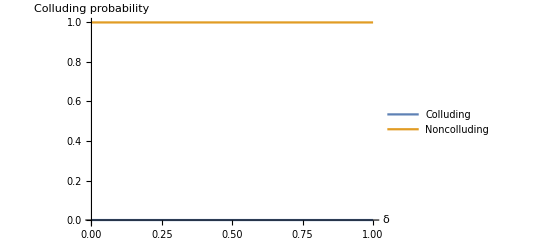

```mathematica
x = points[[All,1]][[1;;20]]
y1 = points[[All,2]][[1;;20]]
y2 = points[[All,2]][[21;;40]]
plot = ListPlot[{y1,y2},DataRange->{0,1}, Joined->True,PlotLegends->{"Colluding","Noncolluding"},PlotRange->{-0.01,1},AxesLabel->{"δ","Colluding probability"}]
(*Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/Collusion smalla Stag Hunt.png",plot]*)
```